```mathematica
ClearAll["`*"];
```

## General definitions

```mathematica
$Assumptions={q>0 , y>0,x>0,x1>0,x2>0,z>0,s>0,d>0,l>0,r>0,Subscript[u, 1]>0,Subscript[u, 2]>0,Subscript[u, 3]>0,Subscript[u, 4]>0,Subscript[u, 5]>0,a>0,Subscript[w, 1]>0,Subscript[w, 2]>0,Subscript[w, 3]>0,Subscript[x, 1]>0,Subscript[x, 2]>0,h>0,f>0,τ>0};
Nmax=1;
qSeries[expr_]:=Series[expr,{q,0,Nmax}];
qSeries[expr_,order_]:=Series[expr,{q,0,order}];
qExpand[expr_]:=Normal[qSeries[expr]];
qExpand[expr_,order_]:=Normal[qSeries[expr,order]];
Theta1[y_,q_]:=
qExpand[-ⅈ*q^(1/8)*y^(1/2)*(1-y^-1)*∏_(n=1)^(Nmax+5) (1-q^n)(1-y*q^n)(1-y^-1 q^n),Nmax+1];
Theta1Modular[u_,τ_]:=(-ⅈ*ⅇ^(2π*ⅈ*τ/8)*ⅇ^(2π*ⅈ*u*1/2)*(1-y^-1)*∏_(n=1)^(Nmax+5) (1-q^n)(1-y*q^n)(1-y^-1 q^n))/.{q->ⅇ^(2π*ⅈ*τ),y->ⅇ^(2π*ⅈ*u)};
Theta[x_,q_]:=∏_(n=0)^Nmax (1-x*q^n)*(1-x^-1 q^(n+1));
Eta[q_]:=qExpand[q^(1/24)*∏_(n=1)^(Nmax+2) (1-q^n),Nmax+1];
E4[q_]:=qExpand[1+240∑_(n=1)^(Nmax+2) (n^3 q^n)/(1-q^n),Nmax+1];
E6[q_]:=qExpand[1-504∑_(n=1)^(Nmax+2) (n^5 q^n)/(1-q^n),Nmax+1];
QPoch[q_]:=∏_(n=1)^Nmax (1-q^n);
qForm[expr_]:=expr/.Theta1[arg_]:>Theta1[arg,q]/.Eta->Eta[q];
ContourInt[expr_,z_]:=Module[{zeta},
SeriesCoefficient[(2π*ⅈ)*expr/.z->Exp[2π*ⅈ*zeta],{zeta,0,-1}]
];
ContourInt[expr_,x_,rest__]:=ContourInt[ContourInt[expr,x],rest];

letterDict=Association[Join[{v->y},Table[Subscript[u, i]->Subscript[w, i],{i,3}],{τ->q}]];
letterDictReverse=Association[Reverse/@Normal[letterDict]];

LinearCoeff[expr_]:=ReplaceAll[Coefficient[expr,τ,0],Thread[Keys[letterDict]->0]];
LinearLogCoeff[expr_]:=ReplaceAll[expr,Thread[Keys[letterDictReverse]->1]]

LetterExp[expr_,dict_]:=Product[dict[letter]^Coefficient[expr,letter],{letter,Keys[dict]}]*Exp[2*π*ⅈ*LinearCoeff[expr]];
LetterExp[expr_]:=LetterExp[expr,letterDict];

LetterLog[expr_,dict_]:=Sum[Exponent[expr,letter]*dict[letter],{letter,Keys[dict]}]+1/(2π*ⅈ)Log[LinearLogCoeff[expr]];
LetterLog[expr_]:=LetterLog[expr,letterDictReverse];

simplifyRule={Θ[0]:>0,
Θ'[0]:>2π*Eta^3,
Θ[c_?NumericQ*rest__]/;Negative[c]:>-Θ[-c*rest],
Θ'[c_?NumericQ*rest__]/;Negative[c]:>Θ'[-c*rest],
Θ''[c_?NumericQ*rest__]/;Negative[c]:>-Θ''[-c*rest],
Θ''[0]:>0};
ResidueFormula[order_]:=D[f[z]/h[z]^order,{z,order-1}]/. h'[z]->0/. Derivative[3][h][z]->0/. Derivative[5][h][z]->0;
replacementRule={Theta1[q*x_]:>-x^-1*(√q)^-1*Theta1[x],
Theta1[q^-1*x_]:>-x*(√q)^-1*Theta1[x]};
ThetaLinearize[func_]:=(func/.Theta1[expr_]:>Θ[LetterLog[expr]]);

Order2Residue[func_,coord_]:=Module[{f,ftag,h},
f=Coefficient[func,Θ[coord]^-2];
h=2π*Eta^3;
ftag=D[f,coord]/.coord->0;
ftag/h^2/.simplifyRule
];
Order2Residue[func_,coord_,rest__]:=Order2Residue[Order2Residue[func,coord],rest];
LinearizeWs[func_]:=Module[{},
func*Product[1/Subscript[w, i]^Exponent[func,Subscript[w, i]]*Exp[2*π*ⅈ*Subscript[u, i]*Exponent[func,Subscript[w, i]]],{i,{1,2}}]
]
Θ[u_,τ_]:=Theta1[ⅇ^(2π*ⅈ*u),q];
dΘ[u_,τ_]:=D[Theta1[ⅇ^(2π*ⅈ*arg),q],arg]/.arg->u;
d2Θ[u_,τ_]:=D[Theta1[ⅇ^(2π*ⅈ*arg),q],{arg,2}]/.arg->u;
ΘForm[func_]:=Evaluate[func/.{Θ[u_]:>Θ[u,τ],Θ'[u_]:>dΘ[u,τ],Θ''[u_]:>d2Θ[u,τ]}]/.{τ->1/(2π*ⅈ)Log[q],v->1/(2π*ⅈ)Log[y]};
SignSp[m_]:=Sign[m]/;m!=0;
SignSp[m_]:=1/;m==0;
```

```mathematica
DrawVectors::usage="Draw a list of vectors and eta";
DrawVectors[VectorList_,eta_]:=
Graphics[
{
(*Plot charge covectors*)
Table[Arrow[{{0,0},{VectorList[[j]][[1]],VectorList[[j]][[2]]}}]
,{j,1,Dimensions[VectorList][[1]]}],

(*Plot eta*)
Red,Dashed,Arrow[{{0,0},{eta[[1]],eta[[2]]}}],Text["η",{eta[[1]],eta[[2]]},{1,-1}]
}];

IsInCone::usage="Check if eta is in the cone ={vec1,vec2}";
IsInCone[cone_,eta_]:=Module[{proj},
proj =Inverse[Transpose[cone]].eta;
AllTrue[proj,Positive]
];

ColinearQ::usage="Check if two vectors are colinear";
ColinearQ[u_,v_]:=VectorAngle[u,v]==0||VectorAngle[u,v]==Pi;

SingularPoints::usage="Returns singular points and singular planes";
SingularPoints[Qcovectors_,SymCovectors_]:=Module[{ptsList,point},
ptsList={};
Do[
If[i<j,
If[!ColinearQ[Qcovectors[[i]],Qcovectors[[j]]],

point=LinearSolve[{Qcovectors[[i]],Qcovectors[[j]]},-{SymCovectors[[i]],SymCovectors[[j]]}];
AppendTo[ptsList,{point,{i,j}}]
]
]

,{i,1,Length[Qcovectors]}
,{j,1,Length[Qcovectors]}
];

KeyValueMap[{#1,Union@@#2}&,GroupBy[ptsList,First->Last]]

]

isIllegalCoordinate[x_]:=Module[{a,b},
a=Coefficient[Coefficient[Expand[x],τ,0], v, 0];(*coefficient of 1*)
b=Coefficient[Expand[x],τ,1];(*coefficient of τ*)

(*illegal if the 1-coefficient is a nonzero integer OR the τ-coefficient is a nonzero integer*)
(IntegerQ[a]&&a!=0)||(IntegerQ[b]&&b!=0)];

isLegalPoint[p_]:=Not[Or@@(isIllegalCoordinate/@p)];

SingularPointsGeneric::usage="Returns singular points and singular planes";
SingularPointsGeneric[Qcovectors_,SymCovectors_]:=Module[{ptsList,point},
ptsList={};
indices=Subsets[Range[1,Length[Qcovectors]],{Length[Qcovectors[[1]]]}];
Do[

If[Det[Qcovectors[[indices[[i]]]]]!=0,

point=LinearSolve[Qcovectors[[indices[[i]]]],-SymCovectors[[indices[[i]]]]];(*if point's coefficient of 1 or tau is integer, do not append*)

If[isLegalPoint[point],
AppendTo[ptsList,{point,indices[[i]]}];
]

]


,{i,1,Length[indices]}
];

KeyValueMap[{#1,Union@@#2}&,GroupBy[ptsList,First->Last]]

]

RelevantSingularPoints::usage="Returns relevant singular points and singular planes wrt eta";
RelevantSingularPoints[Qcovectors_,SymCovectors_,eta_]:=Module[{pointsList,singPts,isRelevant},
pointsList={};
singPts=SingularPoints[Qcovectors,SymCovectors];

Do[
(*Check if the point is relevant wrt eta*)
isRelevant=False;
Do[
If[j<k,
If[IsInCone[{Qcovectors[[j]],Qcovectors[[k]]},eta],
isRelevant=True]
]
,{j,singPts[[i]][[2]]},{k,singPts[[i]][[2]]}];

(*If relevant, add it to the list*)
If[isRelevant,
AppendTo[pointsList,singPts[[i]]]
];

,{i,1,Length[singPts]}];

pointsList
]

RelevantSingularPointsGeneric::usage="Returns relevant singular points and singular planes wrt eta";
RelevantSingularPointsGeneric[Qcovectors_,SymCovectors_,eta_]:=Module[{pointsList,singPts,isRelevant,indices},
pointsList={};
singPts=SingularPointsGeneric[Qcovectors,SymCovectors];

Do[
(*Check if the point is relevant wrt eta*)
isRelevant=False;
indices=Subsets[singPts[[i]][[2]],{Length[Qcovectors[[1]]]}];
Do[

If[IsInCone[Qcovectors[[indices[[j]]]],eta],
isRelevant=True];

,{j,Length[indices]}];

(*If relevant, add it to the list*)
If[isRelevant,
AppendTo[pointsList,singPts[[i]]]
];

,{i,1,Length[singPts]}];

pointsList
]

DrawLines::usage="A function that draw lines as a function of Qcovectors and symmetry charges";
DrawLines[Qcovectors_,SymCovectors_,{xMin_,xMax_},{yMin_,yMax_}]:=Module[{pts,lines},
lines=MapThread[Append,{Qcovectors,SymCovectors}];pts=Table[Module[{α=line[[1]],β=line[[2]],γ=line[[3]]},If[β!=0,(*Non-vertical:compute endpoints*)Line[{{xMin,-(α xMin+γ)/β},{xMax,-(α xMax+γ)/β}}],(*Vertical line:x=-γ/α*)Line[{{-γ/α,yMin},{-γ/α,yMax}}]]],{line,lines}];
Graphics[pts,Axes->True]]

PlotSingularPoints::usage="A function that draw lines and singular points as a function of Qcovectors and symmetry charges";
PlotSingularPoints[Qcovectors_,SymCovectors_]:=Module[{singPts},
singPts=SingularPoints[Qcovectors,SymCovectors];
Show[DrawLines[Qcovectors,SymCovectors,{-2,2},{-2,2}],ListPlot[First/@singPts]]
];

InSpanQ::usage="Check if a vector is in the span of vecs";
InSpanQ[v_,vecs_List]:=If[Length[v]==Length[vecs[[1]]],VectorQ[Quiet[LinearSolve[Transpose[vecs],v]]],False]

FlagList::usage="Create an array of flags and kappa. Returns {flags, kappa}";
FlagList[Qstar_]:=Module[{AccumulateList,permutations,flags,kappa},

permutations=Permutations[Range[Length[Qstar]],{Length[Qstar[[1]]]}];
AccumulateList[list_]:=Table[Take[list,i],{i,Length[list]}];

flags=Table[
AccumulateList[permutations[[i]]]
,{i,1,Length[permutations]}];

Do[
Do[
Do[
If[InSpanQ[Qstar[[k]],Qstar[[flags[[i]][[j]]]]],
flags[[i]][[j]]=Union[flags[[i]][[j]],{k}]
]
,{j,1,Length[flags[[i]]]}]
,{i,1,Length[flags]}]
,{k,1,Length[Qstar]}];
flags=DeleteDuplicates[flags];
kappa=Table[
Table[
Sum[Qstar[[k]],{k,flags[[i]][[j]]}]
,{j,1,Length[flags[[i]]]}]
,{i,1,Length[flags]}];

{flags,kappa}
];

PositiveFlags::usage="Output the positive flags";
PositiveFlags[Qstar_,eta_]:=Module[{flags,kappa,newflags,newkappa},
{flags,kappa}=FlagList[Qstar];
newflags={};
newkappa={};
Do[
If[IsInCone[kappa[[i]],eta],
newflags=Append[newflags,flags[[i]]];
newkappa=Append[newkappa,kappa[[i]]];
]
,{i,1,Length[flags]}];

{newflags,newkappa}
]

OrderedSet::usage="Given a flag F, returns an ordered set of covectors Q_i such that Q_i∈F_i";
OrderedSet[flag_]:=Module[{orderedList={}},
AppendTo[orderedList,flag[[1,1]]];
Do[
AppendTo[orderedList,Part[Complement[flag[[i]],flag[[i-1]]],1]];
,{i,2,Length[flag]}];
orderedList
]

CoordTransformation::usage="Shift and rotate the partition function before the residue operation (includes jacobian)";
CoordTransformation[func_,singpoint_,orderedFlags_,debugMode_:False]:=Module[{funcTransf,coordShift,covectorsInv,coordRotation},
(*Shift the coordinates so that the residue is centered at zero*)

coordShift=Table[Subscript[x, i]->Subscript[x, i]*LetterExp[singpoint[[i]]],{i,1,Length[singpoint]}];
funcTransf=func/.coordShift;

If[debugMode,Print[coordShift]];
If[debugMode,Print[funcTransf]];

(*Rotate the coordinates so that the residue is Subscript[Res, w2] Subscript[Res, w1]*)
covectorsInv=Inverse[orderedFlags];
coordRotation=Table[Subscript[x, k]->∏_(l=1)^Length[orderedFlags] Subscript[w, l]^covectorsInv[[k,l]],{k,Length[orderedFlags]}];
funcTransf=funcTransf/.coordRotation;

If[debugMode,Print[coordRotation]];
If[debugMode,Print[funcTransf]];

(*Multiply by the jacobian*)
funcTransf*Det[covectorsInv]

]
SimpleResidue::usage="Take the residue of the function for a function with simple pole of the form 1/Theta[coord]";
SimpleResidue[func_,coord_]:=Module[{Res},
Res=func*Theta1[coord]*(1/(2π*Eta^3));
Res /. coord -> 1
]
SimpleResidue[func_,coord_,rest__]:=SimpleResidue[SimpleResidue[func,coord],rest];

JKResidue::usage="Output a list of functions f[w_1,w_2]. The JK residue is res_w_2res_w_1f[w_1,w_2].";JKResidue[func_,Qcovectors_,Scovectors_,eta_,debugMode_:False]:=Module[{functionList={},relPoint,point,Qstar,flags,kappas,flag,kappa,basis,funcTransformed,orderedflags},
relPoint=RelevantSingularPointsGeneric[Qcovectors,Scovectors,eta];
(*Run over singular points*)
If[debugMode,Print["There are ",Length[relPoint]," point(s)"];];
Do[
point=relPoint[[idxPoint]][[1]];
Qstar=Qcovectors[[relPoint[[idxPoint]][[2]]]];
{flags,kappas}=PositiveFlags[Qstar,eta];
(*Run over flags*)
If[debugMode,Print["For the point ",point,", there are ",Length[flags]," flag(s)"];];
Do[
flag=flags[[idxFlag]];
kappa=kappas[[idxFlag]];
basis=OrderedSet[flag];
orderedflags=Qstar[[basis]];
funcTransformed=Sign[Det[kappa]]*CoordTransformation[func,point,orderedflags,debugMode];
AppendTo[functionList,funcTransformed];
If[debugMode,Print["Z_(1 - loop)= ",funcTransformed];];
,{idxFlag,1,Length[flags]}];

,{idxPoint,1,Length[relPoint]}];
functionList
]
```

## Tests

### GN model

```mathematica
ZGNmodel=(4 Eta^9 π^3 Theta1[1/(y Subscript[x, 1])]^4 Theta1[1/(y Subscript[x, 2])]^4 Theta1[Subscript[x, 1]/Subscript[x, 2]] Theta1[Subscript[x, 2]/Subscript[x, 1]] Theta1[Subscript[x, 1]/Subscript[x, 3]]^4 Theta1[Subscript[x, 2]/Subscript[x, 3]]^4 Theta1[Subscript[x, 3]/y]^8)/(Theta1[1/y]^3 Theta1[1/Subscript[x, 1]]^4 Theta1[1/Subscript[x, 2]]^4 Theta1[Subscript[x, 1]/(y Subscript[x, 2])] Theta1[Subscript[x, 2]/(y Subscript[x, 1])] Theta1[(y Subscript[x, 1])/Subscript[x, 3]]^4 Theta1[(y Subscript[x, 2])/Subscript[x, 3]]^4 Theta1[Subscript[x, 3]]^8)
```

(4 Eta^9 π^3 Theta1[1/(y x_1)]^4 Theta1[1/(y x_2)]^4 Theta1[x_1/x_2] Theta1[x_2/x_1] Theta1[x_1/x_3]^4 Theta1[x_2/x_3]^4 Theta1[x_3/y]^8)/(Theta1[1/y]^3 Theta1[1/x_1]^4 Theta1[1/x_2]^4 Theta1[x_1/(y x_2)] Theta1[x_2/(y x_1)] Theta1[(y x_1)/x_3]^4 Theta1[(y x_2)/x_3]^4 Theta1[x_3]^8)

```mathematica
Nmax=0
```

0

```mathematica
Z12=1/(2π*ⅈ)^3 ContourInt[ZGNmodel//qForm//qExpand,Subscript[x, 1],Subscript[x, 2],Subscript[x, 3]]
```

-(32 (1+y))/(√y)

```mathematica
Qcovectors={{1,-1,0},{-1,1,0},{0,0,1},{-1,0,0},{0,-1,0},{1,0,-1},{0,1,-1}};
Scovectors={-v,-v,0,0,0,v,v};
epsilon=0.1;
eta={-1,-1-epsilon,1-epsilon};
```

```mathematica
ZJK=JKResidue[ZGNmodel,Qcovectors,Scovectors,eta,False][[1]];
```

Inverse::sing: Matrix {{1,1,0},{-1,-1,0},{0,1,0}} is singular.

Inverse::sing: Matrix {{1,0,0},{-1,-1,0},{0,0,0}} is singular.

Inverse::sing: Matrix {{1,1,0},{-1,0,0},{0,-1,0}} is singular.

General::stop: Further output of Inverse::sing will be suppressed during this calculation.

```mathematica
result=1/(2π*ⅈ)^3 ContourInt[ZJK//qForm//qExpand,Subscript[w, 3],Subscript[w, 2],Subscript[w, 1]]
```

-(32 (1+y))/(√y)

### K3 example

```mathematica
Z1looptest=(4 Eta^6 π^2 Theta1[Subscript[x, 1]/y]^2 Theta1[Subscript[x, 2]/y]^3 Theta1[Subscript[xi, 1]^2/(Subscript[x, 1]^2 Subscript[x, 2]^3)])/(Theta1[1/y]^2 Theta1[Subscript[x, 1]]^2 Theta1[Subscript[x, 2]]^3 Theta1[(y Subscript[xi, 1]^2)/(Subscript[x, 1]^2 Subscript[x, 2]^3)])/.Subscript[xi, 1]->1
```

(4 Eta^6 π^2 Theta1[x_1/y]^2 Theta1[1/(x_1^2 x_2^3)] Theta1[x_2/y]^3)/(Theta1[1/y]^2 Theta1[x_1]^2 Theta1[y/(x_1^2 x_2^3)] Theta1[x_2]^3)

```mathematica
Qcovectors=Join[{{1,0}},{{0,1}},Table[{-2,-3},{i,4}]]
Scovectors=Join[{0},{0},Flatten[Table[v+a+b*τ,{a,{0,1}},{b,{0,1}}]]]
```

{{1,0},{0,1},{-2,-3},{-2,-3},{-2,-3},{-2,-3}}

{0,0,v,v+τ,1+v,1+v+τ}

```mathematica
K3residue=JKResidue[Z1looptest,Qcovectors,Scovectors,{-1,ϵ}]
```

{(2 Eta^6 π^2 Theta1[w_1/y]^3 Theta1[1/(√y w_1^(3/2) √w_2)]^2 Theta1[w_2/y])/(Theta1[1/y]^2 Theta1[w_1]^3 Theta1[(√y)/(w_1^(3/2) √w_2)]^2 Theta1[w_2]),(2 Eta^6 π^2 Theta1[w_1/y]^3 Theta1[(√q)/(√y w_1^(3/2) √w_2)]^2 Theta1[w_2/(q y)])/(Theta1[1/y]^2 Theta1[w_1]^3 Theta1[(√q √y)/(w_1^(3/2) √w_2)]^2 Theta1[w_2/q]),(2 Eta^6 π^2 Theta1[w_1/y]^3 Theta1[-1/(√y w_1^(3/2) √w_2)]^2 Theta1[w_2/y])/(Theta1[1/y]^2 Theta1[w_1]^3 Theta1[-(√y)/(w_1^(3/2) √w_2)]^2 Theta1[w_2]),(2 Eta^6 π^2 Theta1[w_1/y]^3 Theta1[-(√q)/(√y w_1^(3/2) √w_2)]^2 Theta1[w_2/(q y)])/(Theta1[1/y]^2 Theta1[w_1]^3 Theta1[-(√q √y)/(w_1^(3/2) √w_2)]^2 Theta1[w_2/q])}

```mathematica
Nmax=1;
K3residueqExpansion=Total[K3residue]//qForm//qExpand;
1/(2π*ⅈ)^2 ContourInt[K3residueqExpansion,Subscript[w, 1],Subscript[w, 2]]
```

```mathematica
(2 (1+10 y+y^2))/y+(q (21-128 y+216 y^2-129 y^3+20 y^4))/y^2
```

(2 (1+10 y+y^2))/y+(q (21-128 y+216 y^2-129 y^3+20 y^4))/y^2

### Resolved WP4 model

```mathematica
Nmax=0;
Z1loop=((2*π*Eta^3)/Theta1[y^-1])^2 Theta1[Subscript[x, 1]^-4]/Theta1[y*Subscript[x, 1]^-4](Theta1[y^-1*Subscript[x, 2]]/Theta1[Subscript[x, 2]])^2(Theta1[y^-1*Subscript[x, 1]]/Theta1[Subscript[x, 1]])^3 Theta1[y^-1*Subscript[x, 1]*Subscript[x, 2]^-2]/Theta1[Subscript[x, 1]*Subscript[x, 2]^-2];

Qvectors={{1,0},{0,1}};
Svectors={0,0};
Do[
AppendTo[Qvectors, {-4,0}];
AppendTo[Svectors, v+a+b*τ];
,{a,0,3},{b,0,3}];
Do[
AppendTo[Qvectors, {1,-2}];
AppendTo[Svectors, a+b*τ];
,{a,0,1},{b,0,1}];
```

#### Orbifold phase

```mathematica
eta={0.9,-0.1};
residues=JKResidue[Z1loop,Qvectors,Svectors,eta];
```

```mathematica
(1/(2π*ⅈ)^2 ContourInt[residues[[1]]//qForm//qExpand,Subscript[w, 1],Subscript[w, 2]]+1/(2π*ⅈ)^2 ContourInt[residues[[2]]//qForm//qExpand,Subscript[w, 1],Subscript[w, 2]])
```

-(81 (1+y))/(√y)

```mathematica
Nmax=0;
eta={1+0.1,-2+0.1};
residues=JKResidue[Z1loop,Qvectors,Svectors,eta];
```

```mathematica
1/(2*π*ⅈ)^2 ContourInt[residues[[1]]//qForm//qExpand,Subscript[w, 1],Subscript[w, 2]]
```

-(81 (1+y))/(√y)

## Understanding section 3.2.6

```mathematica
expr1=(x^6 (1-y/x^2)^2)/((1-x^2 y)^2)
```

(x^6 (1-y/x^2)^2)/((1-x^2 y)^2)

```mathematica
E1=((∑_(n=-∞)^(M-1) z^n/.z->(x^6 (1-y/x^2)^2)/((1-x^2 y)^2))*((1-x^2)^2)/x^3*y^(n/2)*((x*y^(1/2))/(1-x^2 y))^n*(y^(1/2)/(1-y))^n*((x^-1*y^(1/2))/(1-x^-2 y))^n//FullSimplify)
```

((-1+x^2) ((x^2-y) (-1+y))^-n (x y)^(2 n) (x^3-x y)^(2 M) (-1+x^2 y)^(2-2 M-n))/(x^3+x^5+x^7-x^5 y (2+y))

```mathematica
E1=((-1+x^2) ((x^2-y) (-1+y))^-n (x y)^(2 n) (x^3-x y)^(2 M) (1-x^2 y)^(2-2 M-n))/(x^3+x^5+x^7-x^5 y (2+y))
```

((-1+x^2) ((x^2-y) (-1+y))^-n (x y)^(2 n) (x^3-x y)^(2 M) (1-x^2 y)^(2-2 M-n))/(x^3+x^5+x^7-x^5 y (2+y))

```mathematica
E2=(x^(-3+6 M) (1-x^2) (1-y)^-n y^(2 n) (1-y/x^2)^(2 M-n) (1-x^2 y)^(2-2 M-n))/(1+x^4+x^2 (1-2 y-y^2))//FullSimplify
```

(x^(-3+6 M) (1-x^2) (1-y)^-n y^(2 n) (1-y/x^2)^(2 M-n) (1-x^2 y)^(2-2 M-n))/(1+x^2+x^4-x^2 y (2+y))

```mathematica
E1-E2//Simplify
```

((-1+x^2) ((x^2-y) (-1+y))^(-2 n) (x y)^(2 n) (-1+x^2 y)^(2-2 M-n) (x^(6 M) ((x^2-y) (-1+y))^n (-1+y/x^2)^(2 M)+((-1+y) (-x^2+y))^n (x^3-x y)^(2 M)))/(x^3 (1+x^4-x^2 (-1+2 y+y^2)))

```mathematica
Integrand=E1*(1+x^2(1-2y-y^2)+x^4)
```

((-1+x^2) ((x^2-y) (-1+y))^-n (x y)^(2 n) (x^3-x y)^(2 M) (1-x^2 y)^(2-2 M-n) (1+x^4+x^2 (1-2 y-y^2)))/(x^3+x^5+x^7-x^5 y (2+y))

```mathematica
f1[y_]:=((y+1)+√(y^2+2y-3))/2;
f2[y_]:=(-(y+1)+√(y^2+2y-3))/2;
f3[y_]:=((y+1)-√(y^2+2y-3))/2;
f4[y_]:=(-(y+1)-√(y^2+2y-3))/2;
```

```mathematica
result=ReplaceAll[Integrand*1/((x-f2[y])*(x-f3[y])*(x-f4[y])),x->f1[y]]+ReplaceAll[Integrand*1/((x-f1[y])*(x-f3[y])*(x-f4[y])),x->f2[y]]+ReplaceAll[Integrand*1/((x-f2[y])*(x-f1[y])*(x-f4[y])),x->f3[y]]+ReplaceAll[Integrand*1/((x-f2[y])*(x-f3[y])*(x-f1[y])),x->f4[y]]//Rationalize//FullSimplify
```

8^-n (-1+y^2)^(1-8 n) ((y (1+y+√((-1+y) (3+y))))^(2 n) ((-1+y^2)^6 (1+√((-1+y) (3+y))+y (-2-y+√((-1+y) (3+y)))))^n+(y (1+y-√((-1+y) (3+y))))^(2 n) (-(-1+y^2)^6 (-1+√((-1+y) (3+y))+y (2+y+√((-1+y) (3+y)))))^n)

```mathematica
$Assumptions={q>0 , y>0,x>0,x1>0,x2>0,z>0,s>0,m∈Integers,n∈Integers,M∈Integers,n>0};
```

```mathematica
Series[result,{y,0,3}]//Rationalize/.n->3//FullSimplify
```

y^(2 n) (-2 (-1)^n+(-1)^n (2-4 n) y^2+O[y]^4)

```mathematica
1/2 result/.y->0.6/.n->10
```

-0.176038+0. ⅈ

```mathematica
Z=y*((y/(1-y^2))^(2n-1))/.y->0.6/.n->10
```

0.176038

```mathematica
Series[Z,{y,0,2}]
```

y^(2 n) (1+(-1+2 n) y^2+O[y]^3)

## Seiberg duality example

### Gauge theory side

```mathematica
Fsqrt=((ⅈ*Eta[q])/Theta1[x*y^-2,q])*((ⅈ*Eta[q])/Theta1[x^-1*y^-2,q])^-1*((ⅈ*Eta[q])/Theta1[x*y,q])^2((ⅈ*Eta[q])/Theta1[x^-1*y,q])^-2//qExpand;
```

```mathematica
F=Fsqrt^2
```

((x-y)^4 (-1+x y^2)^2)/((-1+x y)^4 (x-y^2)^2)

```mathematica
IG=1/2 ⅈ*(Eta[q])^2(Theta1[x^2,q]*Theta1[x^-2,q])/(ⅈ*Eta[q])^2*((ⅈ*Eta[q])/Theta1[x*y^-2,q])^(-2(2n+M))*((ⅈ*Eta[q])/Theta1[x^-1*y^-2,q])^(2(M-2n))*((ⅈ*Eta[q])/Theta1[x*y,q])^(4(-M+n+1))*((ⅈ*Eta[q])/Theta1[x^-1*y,q])^(4(M+n+1))*1/(ⅈ*x)//qExpand
```

-1/(2 q^(5/12))x (-1+x^2)^2 (x-y)^(-4 (1+M+n)) y^(4-4 n) (-1+x y)^(-4+4 M-4 n) (x-y^2)^(2 M+4 n) (-1+x y^2)^(-2 M+4 n)

```mathematica
Integrand=IG/(1-F)//qExpand
```

((-1+x^2) (x-y)^(-4 (1+M+n)) y^(4-4 n) (-1+x y)^(4 M-4 n) (x-y^2)^(2+2 M+4 n) (-1+x y^2)^(-2 M+4 n))/(2 q^(5/12) (-1+y)^3 (1+y) (2 y^2+2 x^2 y^2-x (1+y (2+y (-2+y (2+y))))))

```mathematica
2 y^2+2 x^2 y^2-x (1+y (2+y (-2+y (2+y))))==2 y^2(1+x^2)-x(1+2y-2 y^2+2 y^3+y^4)//Simplify
```

True

```mathematica
(2 y^2+2 x^2 y^2-x (1+y (2+y (-2+y (2+y)))))==2 y^2(x-f1[y])(x-f2[y])//Simplify
```

True

```mathematica
Solve[2 y^2+2 x^2 y^2-x (1+y (2+y (-2+y (2+y))))==0,x]
```

{{x→(1+2 y-2 y^2+2 y^3+y^4)/(4 y^2)-(√(1+4 y-4 y^3-2 y^4-4 y^5+4 y^7+y^8))/(4 y^2)},{x→(1+2 y-2 y^2+2 y^3+y^4)/(4 y^2)+(√(1+4 y-4 y^3-2 y^4-4 y^5+4 y^7+y^8))/(4 y^2)}}

```mathematica
(x-f1[y])*(x-f2[y])*y^2*2//Expand
```

-x-2 x y+2 y^2+2 x y^2+2 x^2 y^2-2 x y^3-x y^4

```mathematica
(2 y^2+2 x^2 y^2-x (1+y (2+y (-2+y (2+y)))))//Expand
```

-x-2 x y+2 y^2+2 x y^2+2 x^2 y^2-2 x y^3-x y^4

```mathematica
f1[y_]:=(1+2 y-2 y^2+2 y^3+y^4)/(4 y^2)-(√(1+4 y-4 y^3-2 y^4-4 y^5+4 y^7+y^8))/(4 y^2);
f2[y_]:=(1+2 y-2 y^2+2 y^3+y^4)/(4 y^2)+(√(1+4 y-4 y^3-2 y^4-4 y^5+4 y^7+y^8))/(4 y^2);
```

```mathematica
Integrand2=Integrand*(2 y^2+2 x^2 y^2-x (1+y (2+y (-2+y (2+y)))))/(2 y^2)//Simplify;
```

```mathematica
result=ReplaceAll[Integrand2*1/(x-f2[y]),x->f1[y]]+ReplaceAll[Integrand2*1/(x-f1[y]),x->f2[y]]//Simplify
```

1/(q^(5/12) (-1+y^2)^5)2^(-1-18 M-16 n) (-1+y)^(-4 M) y^(4-4 n) (1+y^2)^(1-2 M) (1/y-2 y+y^3)^(-4 (M+2 n)) ((((-1+y)^2 (1+y) (1+y^2-√(1+4 y+2 y^2+4 y^3+y^4)))/y)^(4 n) (((-1+y^2) (-1+2 y+y^2-√(1+4 y+2 y^2+4 y^3+y^4)))/y)^(4 M) (((-1+y^2) (-1-2 y+y^2+√(1+4 y+2 y^2+4 y^3+y^4)))/y^2)^(4 (M+n)) (-3+2 y-2 y^2+2 y^3+y^4+(-1+y^2) √(1+4 y+2 y^2+4 y^3+y^4))^(2 M) (-2+1/y^2+2/y+2 y-3 y^2-((-1+y^2) √(1+4 y+2 y^2+4 y^3+y^4))/y^2)^(2 (M+2 n))+(((-1+y^2) (-1-2 y+y^2-√(1+4 y+2 y^2+4 y^3+y^4)))/y^2)^(4 (M+n)) (((-1+y)^2 (1+y) (1+y^2+√(1+4 y+2 y^2+4 y^3+y^4)))/y)^(4 n) (((-1+y^2) (-1+2 y+y^2+√(1+4 y+2 y^2+4 y^3+y^4)))/y)^(4 M) (-3+2 y-2 y^2+2 y^3+y^4-(-1+y^2) √(1+4 y+2 y^2+4 y^3+y^4))^(2 M) (-2+1/y^2+2/y+2 y-3 y^2+((-1+y^2) √(1+4 y+2 y^2+4 y^3+y^4))/y^2)^(2 (M+2 n)))

```mathematica
result//FullSimplify
```

1/(q^(5/12) (1+y)^5)2^(-1-18 M-16 n) (-1+y)^(-5-4 M) y^(4-4 n) (1+y^2)^(1-2 M) (1/y-2 y+y^3)^(-4 (M+2 n)) ((((-1+y)^2 (1+y) (1+y^2-√((1+y^2) (1+y (4+y)))))/y)^(4 n) (((-1+y^2) (-1+y (2+y)-√((1+y^2) (1+y (4+y)))))/y)^(4 M) (((-1+y^2) (-1+(-2+y) y+√((1+y^2) (1+y (4+y)))))/y^2)^(4 (M+n)) (-3+2 y-2 y^2+2 y^3+y^4+(-1+y^2) √((1+y^2) (1+y (4+y))))^(2 M) (-2+1/y^2+2/y+2 y-3 y^2-((-1+y^2) √((1+y^2) (1+y (4+y))))/y^2)^(2 (M+2 n))+(((-1+y^2) (-1+(-2+y) y-√((1+y^2) (1+y (4+y)))))/y^2)^(4 (M+n)) (((-1+y)^2 (1+y) (1+y^2+√((1+y^2) (1+y (4+y)))))/y)^(4 n) (((-1+y^2) (-1+y (2+y)+√((1+y^2) (1+y (4+y)))))/y)^(4 M) (-3+2 y-2 y^2+2 y^3+y^4-(-1+y^2) √((1+y^2) (1+y (4+y))))^(2 M) (-2+1/y^2+2/y+2 y-3 y^2+((-1+y^2) √((1+y^2) (1+y (4+y))))/y^2)^(2 (M+2 n)))

```mathematica
Z=-y^4(1+y)^(-8*n)(1-y^2)^-5(1+y^2)^(4n+1)
```

-(y^4 (1+y)^(-8 n) (1+y^2)^(1+4 n))/((1-y^2)^5)

```mathematica
res2=result*q^(5/12)/.M->0//Simplify
```

(-1+y)^(16 n) y^4 (1+y)^(8 n) (-1+y^2)^(-5-16 n) (1+y^2)^(1+4 n)

```mathematica
Simplify[res2,{n∈Integers,y>1}]
```

(-1+y)^(16 n) y^4 (1+y)^(8 n) (-1+y^2)^(-5-16 n) (1+y^2)^(1+4 n)

```mathematica
Z//Simplify
```

(y^4 (1+y)^(-8 n) (1+y^2)^(1+4 n))/((-1+y^2)^5)

```mathematica
(result*q^(5/12)/.M->0)==Z//Simplify
```

True

### Free field side of the duality

```mathematica
fchi[g_,a_,r_]:=((ⅈ*Eta[q])/Theta1[x^g*y^a,q])^(g*m+a*n-r+1)
```

```mathematica
Zdual=fchi[0,-4,2]*fchi[0,-1,1]^8*fchi[0,2,0]^6//qExpand
```

q^(-3/4+1/24 (-1-4 n)-n/3+1/24 (6+12 n)) (ⅇ^(12 ⅈ n π) q^(1/8) (1/(-1+y))^(-8 n) y^4 (-1+y^2)^(-6-12 n) (1/(-1+y^4))^(-1-4 n)+q^(9/8) (ⅇ^(12 ⅈ n π) (1/(-1+y))^(-8 n) (-1+y^2)^(-6-12 n) (1/(-1+y^4))^(-1-4 n) (-1-4 n-y^8-4 n y^8)+y^(-2-8 n) (1/(-1+y^4))^(-1-4 n) (-8 ⅇ^(12 ⅈ n π) (1/(-1+y))^(-8 n) y^(5+8 n) (-1+y^2)^(-6-12 n) (n+n y^2)+6 ⅇ^(12 ⅈ n π) (1/(-1+y))^(-8 n) y^(4+8 n) (-1+y^2)^(-6-12 n) (1+2 n+y^4+2 n y^4))))

### Comparing results

```mathematica
n=.
ZresultPaper=-q^(-5/12)y^4(1+y)^(-8n)(1-y^2)^-5(1+y^2)^(4n+1)
```

-(y^4 (1+y)^(-8 n) (1+y^2)^(1+4 n))/(q^(5/12) (1-y^2)^5)

```mathematica
Zdual==(result/.M->0)//FullSimplify
```

$Aborted

### Truncation

```mathematica
Nmax=0
```

0

```mathematica
n=.
```

```mathematica
Z1loop[m_]:=-1/2*(Eta[q])^2(Theta1[x^2,q]*Theta1[x^-2,q])/(ⅈ*Eta[q])^2*((ⅈ*Eta[q])/Theta1[x*y^-2,q])^(2(m-2n))*((ⅈ*Eta[q])/Theta1[x^-1*y^-2,q])^(2(-m-2n))*((ⅈ*Eta[q])/Theta1[x*y,q])^(4(m+n+1))*((ⅈ*Eta[q])/Theta1[x^-1*y,q])^(4(-m+n+1))/.x->x*y//qExpand
```

```mathematica
$Assumptions={m<=n,m>=-n}
```

{m≤n,m≥-n}

```mathematica
Z1loopm=Z1loop[m]
```

((1/(q^(1/12) (-1+x) √(1/x)))^(-4 m+4 n) (-(√(x/y) y)/(q^(1/12) (x-y)))^(2 (m-2 n)) √(x^2 y^2) ((√(x y^2))/(q^(1/12) (1-x y^2)))^(4 (m+n)) (-1+x^2 y^2)^2 (1/(q^(1/12) √(1/(x y^3)) (-1+x y^3)))^(-2 (m+2 n)))/(2 q^(5/12) (-1+x)^4 √(1/(x^2 y^2)) (-1+x y^2)^4)

```mathematica
f[x_]:=((1/(q^(1/12) √(1/x)))^(-4 m+4 n) (-(√(x/y) y)/(q^(1/12) (x-y)))^(2 (m-2 n)) √(x^2 y^2) ((√(x y^2))/(q^(1/12) (1-x y^2)))^(4 (m+n)) (-1+x^2 y^2)^2 (1/(q^(1/12) √(1/(x y^3)) (-1+x y^3)))^(-2 (m+2 n)))/(2 q^(5/12)√(1/(x^2 y^2)) (-1+x y^2)^4)//qExpand
```

```mathematica
f[x]
```

((1/(q^(1/12) √(1/x)))^(-4 m+4 n) (-(√(x/y) y)/(q^(1/12) (x-y)))^(2 (m-2 n)) √(x^2 y^2) ((√(x y^2))/(q^(1/12) (1-x y^2)))^(4 (m+n)) (-1+x^2 y^2)^2 (1/(q^(1/12) √(1/(x y^3)) (-1+x y^3)))^(-2 (m+2 n)))/(2 q^(5/12) √(1/(x^2 y^2)) (-1+x y^2)^4)

```mathematica
ContourInt[Z1loop[0],x]//Simplify
```

(y^4+y^6)/(q^(5/12) (-1+y^2)^5)

-(y^4 (1+y^2))/(q^(5/12) (1-y^2)^5)

```mathematica
Zresult==Zgauge//Simplify
```

-(y^4 (1+y^2)^5)/(q^(5/12) (1+y)^8 (1-y^2)^5)==(y^4 (1+y^2)^5)/(q^(5/12) (-1+y)^5 (1+y)^13)

```mathematica
n=.
ZresultPaper=-q^(-5/12)y^4(1+y)^(-8n)(1-y^2)^-5(1+y^2)^(4n+1)
```

-(y^4 (1+y)^(-8 n) (1+y^2)^(1+4 n))/(q^(5/12) (1-y^2)^5)

```mathematica
n=.
Z1loop[m_]:=1/(4*π)*(Eta)^2(Theta1[x^2]*Theta1[x^-2])/(ⅈ*Eta)^2*((ⅈ*Eta)/Theta1[x*y^-2])^(2(m-2n))*((ⅈ*Eta)/Theta1[x^-1*y^-2])^(2(-m-2n))*((ⅈ*Eta)/Theta1[x*y])^(4(m+n+1))*((ⅈ*Eta)/Theta1[x^-1*y])^(4(-m+n+1))
```

Choosing negative charge for m>0, giving naive poles at -2m-4n>0 -> m<-2n and -m+n+1>0 -> m<n+1.
Choosing positive charge for m<0, giving naive poles at m-2n>0 -> m>2n and m+n+1>0 -> m>-n-1.

For n>0, we have -n-1<m<n+1. For m=0 case, the m+n+1 or -m+n+1 contribute (same contribution).
For n<0, we have 2n<m<-2n. For m=0 case, the m-2n or -m-2n contribute (same contribution).

Check lowest order of q:

```mathematica
Nmax=0;
n=0;
Print["Paper result:"];
ZresultPaper
Print["Truncation result:"];
Z=2*π(∑_(m=-n)^0 ((ContourInt[(Z1loop[m]/.x->x*y^-1)//qForm//qExpand,x])+
ContourInt[(Z1loop[m]/.x->x*y^2)//qForm//qExpand,x])-∑_(m=1)^n ((ContourInt[(Z1loop[m]/.x->x*y^1)//qForm//qExpand,x])+(ContourInt[(Z1loop[m]/.x->x*y^-2)//qForm//qExpand,x])))//Simplify
Print["Equality: ", Z==ZresultPaper//Simplify]
```

Paper result:

-(y^4 (1+y^2))/(q^(5/12) (1-y^2)^5)

Truncation result:

(y^4+y^6)/(q^(5/12) (-1+y^2)^5)

Equality: True

```mathematica
n=.
fchi[g_,a_,r_]:=((ⅈ*Eta)/Theta1[x^g*y^a])^(g*m+a*n-r+1);
Zdual=fchi[0,-4,2]*fchi[0,-1,1]^8*fchi[0,2,0]^6;
```

More general approach, which allows higher orders of q:

```mathematica
Nmax=0;
n=1;
Print["Dual result:"];
ZdualResult=Zdual//qForm//Simplify//qExpand
Print["Truncation result:"];
Z=2*π(∑_(m=-n)^0 ((ContourInt[(Z1loop[m]/.x->x*y^-1)//qForm//qExpand,x])+
ContourInt[(Z1loop[m]/.x->x*y^2)//qForm//qExpand,x])-∑_(m=1)^n ((ContourInt[(Z1loop[m]/.x->x*y^1)//qForm//qExpand,x])+(ContourInt[(Z1loop[m]/.x->x*y^-2)//qForm//qExpand,x])))//Simplify//qExpand
Print["Equality: ", Z==ZdualResult//Simplify]
```

Dual result:

(y^4 (1+y^2)^5)/(q^(5/12) (-1+y)^5 (1+y)^13)

Truncation result:

(y^4 (1+y^2)^5)/(q^(5/12) (-1+y)^5 (1+y)^13)

Equality: True

Above we can see the equality with the dual case holds for different n values at Nmax=0. Can also show Nmax=1 for n=0 but higher cases gets stuck.
Now check what happens if we choose the “wrong” poles, which SHOULD eventually give 0 contribution.

```mathematica
n=1;
```

```mathematica
(* "Correct" poles *)
ContourInt[(Z1loop[-n-2]/.x->x*y^-1)//qForm//qExpand,x]//Simplify
ContourInt[(Z1loop[-n-2]/.x->x*y^2)//qForm//qExpand,x]//Simplify
```

0

0

```mathematica
(* "Incorrect" Pole *)
ContourInt[(Z1loop[-n-2]/.x->x*y^1)//qForm//qExpand,x]//Simplify
```

(y^4 (1+y+y^2+y^3)^11 (1-3 y-7 y^2+8 y^3-7 y^4-3 y^5+y^6))/(4 π q^(5/12) (-1+y)^5 (1+y+y^2)^21)

```mathematica
(* "Incorrect" Pole *)
ContourInt[(Z1loop[-n-2]/.x->x*y^-2)//qForm//qExpand,x]//Simplify
```

-(y^4 (1+y+y^2+y^3)^11 (1-3 y-7 y^2+8 y^3-7 y^4-3 y^5+y^6))/(4 π q^(5/12) (-1+y)^5 (1+y+y^2)^21)

```mathematica
(* "Correct" poles *)
ContourInt[(Z1loop[n+2]/.x->x*y^1)//qForm//qExpand,x]//Simplify
ContourInt[(Z1loop[n+2]/.x->x*y^-2)//qForm//qExpand,x]//Simplify
```

0

0

```mathematica
(* "Incorrect" Pole *)
ContourInt[(Z1loop[n+2]/.x->x*y^-1)//qForm//qExpand,x]//Simplify
```

-(y^4 (1+y+y^2+y^3)^11 (1-3 y-7 y^2+8 y^3-7 y^4-3 y^5+y^6))/(4 π q^(5/12) (-1+y)^5 (1+y+y^2)^21)

```mathematica
(* "Incorrect" Pole *)
ContourInt[(Z1loop[n+2]/.x->x*y^2)//qForm//qExpand,x]//Simplify
```

(y^4 (1+y+y^2+y^3)^11 (1-3 y-7 y^2+8 y^3-7 y^4-3 y^5+y^6))/(4 π q^(5/12) (-1+y)^5 (1+y+y^2)^21)

### Characters

```mathematica
Chi=∑_(i=1)^6 Subscript[a, i]
```

a_1+a_2+a_3+a_4+a_5+a_6

```mathematica
dict={Subscript[a, 1]->Subscript[b, 1]*a,Subscript[a, 2]->Subscript[b, 2]*a,Subscript[a, 3]->Subscript[b, 3]*a,Subscript[a, 4]->Subscript[b, 4]*a,Subscript[a, 5]->Subscript[c, 1]*a^-2,Subscript[a, 6]->Subscript[c, 2]*a^-2}
```

{a_1→a b_1,a_2→a b_2,a_3→a b_3,a_4→a b_4,a_5→c_1/a^2,a_6→c_2/a^2}

```mathematica
ReplaceAll[Chi,dict]
```

a b_1+a b_2+a b_3+a b_4+c_1/a^2+c_2/a^2

```mathematica
(ReplaceAll[Chi^2,dict]//Expand)/.Subscript[b, 4]->1/(Subscript[b, 1]*Subscript[b, 2]*Subscript[b, 3])/.Subscript[c, 2]->1/Subscript[c, 1]
```

2/a^4+a^2 b_1^2+(2 a^2)/(b_1 b_2)+2 a^2 b_1 b_2+a^2 b_2^2+a^2/(b_1^2 b_2^2 b_3^2)+(2 a^2)/(b_1 b_3)+(2 a^2)/(b_2 b_3)+2 a^2 b_1 b_3+2 a^2 b_2 b_3+a^2 b_3^2+1/(a^4 c_1^2)+(2 b_1)/(a c_1)+(2 b_2)/(a c_1)+2/(a b_1 b_2 b_3 c_1)+(2 b_3)/(a c_1)+(2 b_1 c_1)/a+(2 b_2 c_1)/a+(2 c_1)/(a b_1 b_2 b_3)+(2 b_3 c_1)/a+c_1^2/a^4

### Comparing the index with fugacities

For simplicity, we compute the index for the simple case of n=0 with truncation. Without turning on fugacities, we expect the following result:

```mathematica
Zdual/.n->0
```

(y^4 (1+y^2))/(q^(5/12) (-1+y^2)^5)

#### Free side of the duality

```mathematica
n=0;
fchi[g_,a_,r_,f_]:=((ⅈ*Eta[q])/Theta1[x^g*y^a*f,q])^(g*m+a*n-r+1)
```

```mathematica
Zdual=fchi[0,-4,2,1]*∏_(i=1)^4 (fchi[0,-1,1,Subscript[f, i]*c]*fchi[0,-1,1,Subscript[f, i]*c^-1])*∏_(j=1)^4 If[i<j,fchi[0,2,0,Subscript[f, i]*Subscript[f, j]],1]//qExpand
```

(y^4 (-1+y^4) (f_1 f_2 f_3 f_4)^(3/2))/(q^(5/12) (-1+y^2 f_1 f_2) (-1+y^2 f_1 f_3) (-1+y^2 f_2 f_3) (-1+y^2 f_1 f_4) (-1+y^2 f_2 f_4) (-1+y^2 f_3 f_4))

#### Gauge side of the duality

```mathematica
Z1loop[m_]:=-1/2*(Eta[q])^2*(Theta1[x^2,q]*Theta1[x^-2,q])/(ⅈ*Eta[q])^2*((ⅈ*Eta[q])/Theta1[x*y^-2*c,q])^(m-2n)*((ⅈ*Eta[q])/Theta1[x*y^-2*c^-1,q])^(m-2n)*((ⅈ*Eta[q])/Theta1[x^-1*y^-2*c,q])^(-m-2n)*((ⅈ*Eta[q])/Theta1[x^-1*y^-2*c^-1,q])^(-m-2n)*∏_(i=1)^4 ((ⅈ*Eta[q])/Theta1[x*y*Subscript[f, i],q])^(m+n+1)*((ⅈ*Eta[q])/Theta1[x^-1*y*Subscript[f, i],q])^(-m+n+1)//qExpand
```

```mathematica
Z1loopeval=Z1loop[0];
Zgauged=0;
Do[
Zgauged=Zgauged+ContourInt[Z1loopeval/.x->x*y*Subscript[f, i],x]
,{i,1,4}];
Zgauged=Zgauged//Simplify
```

(y^4 f_1 f_2 f_3 f_4 (-1+y^4 f_1 f_2 f_3 f_4))/(q^(5/12) (-1+y^2 f_1 f_2) (-1+y^2 f_1 f_3) (-1+y^2 f_2 f_3) (-1+y^2 f_1 f_4) (-1+y^2 f_2 f_4) (-1+y^2 f_3 f_4))

#### Comparison

```mathematica
Zgauged
```

(y^4 f_1 f_2 f_3 f_4 (-1+y^4 f_1 f_2 f_3 f_4))/(q^(5/12) (-1+y^2 f_1 f_2) (-1+y^2 f_1 f_3) (-1+y^2 f_2 f_3) (-1+y^2 f_1 f_4) (-1+y^2 f_2 f_4) (-1+y^2 f_3 f_4))

```mathematica
Zdual
```

(y^4 (-1+y^4) (f_1 f_2 f_3 f_4)^(3/2))/(q^(5/12) (-1+y^2 f_1 f_2) (-1+y^2 f_1 f_3) (-1+y^2 f_2 f_3) (-1+y^2 f_1 f_4) (-1+y^2 f_2 f_4) (-1+y^2 f_3 f_4))

```mathematica
Zdual==Zgauged//Simplify
```

(-1+y^4 f_1 f_2 f_3 f_4+√(f_1 f_2 f_3 f_4)-y^4 √(f_1 f_2 f_3 f_4))/((-1+y^2 f_1 f_2) (-1+y^2 f_1 f_3) (-1+y^2 f_2 f_3) (-1+y^2 f_1 f_4) (-1+y^2 f_2 f_4) (-1+y^2 f_3 f_4))==0

## A_1 compactification with flux n=1

Let’s define the partition function:

```mathematica
n=.;m=.;
fchi[g_,a_,r_]:=((ⅈ*Eta)/Theta1[x^g*y^a])^(g*m+a*n-r+1);
Z1loop=1/2*1/(2π*ⅈ)*ⅈ*(Eta)^2*(Theta1[x^2]*Theta1[x^-2])/(ⅈ*Eta)^2*fchi[0,-2,2]*Product[fchi[g,-1,1]*fchi[g,1,0],{g,{2,0,-2}}]
```

-1/(4 π)Theta1[1/x^2] Theta1[x^2] ((ⅈ Eta)/Theta1[1/y^2])^(-1-2 n) ((ⅈ Eta)/Theta1[1/y])^-n ((ⅈ Eta)/Theta1[1/(x^2 y)])^(-2 m-n) ((ⅈ Eta)/Theta1[x^2/y])^(2 m-n) ((ⅈ Eta)/Theta1[y])^(1+n) ((ⅈ Eta)/Theta1[y/x^2])^(1-2 m+n) ((ⅈ Eta)/Theta1[x^2 y])^(1+2 m+n)

### Find truncation:

```mathematica
FindTruncationRank1[n_,Mmax_]:=Module[{mList={},SignSp},
SignSp[m_]:=Sign[m]/;m!=0;
SignSp[m_]:=1/;m==0;
Do[
If[m>0,
If[(1-2 m+n>0)||(-2 m-n>0),
AppendTo[mList,m]
]
];
If[m<0,
If[(2 m-n>0)||(1+2 m+n>0),
AppendTo[mList,m]
]
];
If[m==0,
AppendTo[mList,m]
];
,{m,-Mmax,Mmax}];
mList
]
```

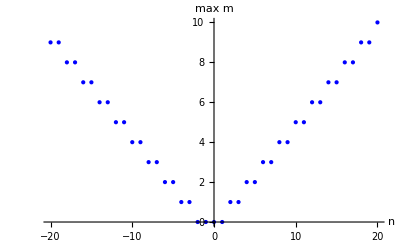

```mathematica
Mmax=50;ListPlot[Table[{n,Max[FindTruncationRank1[n,Mmax]]},{n,-20,20}],PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"n","max m"},PlotRange->All]
```

Computing the JK residue:

### n=0

#### n=0, m=0

```mathematica
n=0;m=0;
Z1loop
```

(Eta^2 Theta1[1/x^2] Theta1[x^2] Theta1[1/y^2])/(4 π Theta1[y] Theta1[y/x^2] Theta1[x^2 y])

```mathematica
(*positive poles*)
poles={(√y)^-1,√q(√y)^-1,-(√y)^-1,-√q(√y)^-1};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];

Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

```mathematica
Res
```

(Theta1[1/y^2] Theta1[1/y])/(4 Eta π^2 Theta1[y^2])

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

Theta1[y]/(4 Eta π^2)

#### n=1, m=1

```mathematica
n=0;m=1;
Z1loop
```

(Eta^2 Theta1[1/x^2] Theta1[x^2] Theta1[1/y^2] Theta1[1/(x^2 y)]^2 Theta1[y/x^2])/(4 π Theta1[x^2/y]^2 Theta1[y] Theta1[x^2 y]^3)

We don’t have negative poles, so the JK residue is zero. As a consistency check, we choose the positive poles:

```mathematica
(*positive poles*)
poles={√y,√q √y,-√y,-√q √y,(√y)^-1,√q(√y)^-1,-(√y)^-1,-√q(√y)^-1};
```

```mathematica
Nmax=1;
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;


Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
,{i,1,Length[poles]}]
Res//Simplify
```

0

#### n=1, m=0

```mathematica
n=1;m=.;
Z1loop
```

1/(4 Eta^2 π Theta1[y]^2)Theta1[1/x^2] Theta1[x^2] Theta1[1/y^2]^3 Theta1[1/y] ((ⅈ Eta)/Theta1[1/(x^2 y)])^(-1-2 m) ((ⅈ Eta)/Theta1[x^2/y])^(-1+2 m) ((ⅈ Eta)/Theta1[y/x^2])^(2-2 m) ((ⅈ Eta)/Theta1[x^2 y])^(2+2 m)

```mathematica
(*positive poles*)
poles={(√y)^-1,√q(√y)^-1,-(√y)^-1,-√q(√y)^-1};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];

Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

```mathematica
Res
```

(Theta1[1/y^2] Theta1[1/y])/(4 Eta π^2 Theta1[y^2])

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

Theta1[y]/(4 Eta π^2)

### n=-1

#### n=-1, m=0

```mathematica
n=-1;m=0;
Z1loop
```

-(Eta^4 Theta1[1/x^2] Theta1[x^2])/(4 π Theta1[1/y^2] Theta1[1/y] Theta1[1/(x^2 y)] Theta1[x^2/y])

```mathematica
(*positive poles*)
poles={√y,√q √y,-√y,-√q √y};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];


Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];

Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

```mathematica
Res
```

-(Eta Theta1[y])/(4 π^2 Theta1[1/y^2]^2)

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

-(Eta Theta1[y])/(4 π^2 Theta1[y^2]^2)

#### n=-1, m=1

```mathematica
n=-1;m=1;
Z1loop
```

-(Eta^4 Theta1[1/x^2] Theta1[x^2] Theta1[1/(x^2 y)] Theta1[y/x^2]^2)/(4 π Theta1[1/y^2] Theta1[1/y] Theta1[x^2/y]^3 Theta1[x^2 y]^2)

We see only positive poles. Taking only negative poles in the JK residue, we get 0 as expected.

### n=-2

#### n=-2, m=0

```mathematica
n=-2;m=0;
Z1loop
```

(Eta^6 Theta1[1/x^2] Theta1[x^2] Theta1[y] Theta1[y/x^2] Theta1[x^2 y])/(4 π Theta1[1/y^2]^3 Theta1[1/y]^2 Theta1[1/(x^2 y)]^2 Theta1[x^2/y]^2)

```mathematica
(*positive poles*)
poles={√y,√q √y,-√y,-√q √y};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];
Print[Ztemp];
Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

-(Eta^6 Theta1[1/(x y)] Theta1[y] Theta1[x y] Theta1[x y^2])/(8 π Theta1[x] Theta1[1/y^2]^3 Theta1[1/(x y^2)]^2 Theta1[1/y]^2)

-(Eta^6 Theta1[1/(x y)] Theta1[y] Theta1[x y] Theta1[x y^2])/(8 π Theta1[x] Theta1[1/y^2]^3 Theta1[1/(x y^2)]^2 Theta1[1/y]^2)

-(Eta^6 Theta1[1/(x y)] Theta1[y] Theta1[x y] Theta1[x y^2])/(8 π Theta1[x] Theta1[1/y^2]^3 Theta1[1/(x y^2)]^2 Theta1[1/y]^2)

«1 more identical outputs»

```mathematica
Res
```

-(Eta^3 Theta1[y]^2 Theta1[y^2])/(4 π^2 Theta1[1/y^2]^5 Theta1[1/y])

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

-(Eta^3 Theta1[y])/(4 π^2 Theta1[y^2]^4)

#### n=-1, m=1

```mathematica
n=-1;m=1;
Z1loop
```

-(Eta^4 Theta1[1/x^2] Theta1[x^2] Theta1[1/(x^2 y)] Theta1[y/x^2]^2)/(4 π Theta1[1/y^2] Theta1[1/y] Theta1[x^2/y]^3 Theta1[x^2 y]^2)

We see only positive poles. Taking only negative poles in the JK residue, we get 0 as expected.

### n=-3

#### n=-3, m=0

```mathematica
n=-3;m=0;
Z1loop
```

-(Eta^8 Theta1[1/x^2] Theta1[x^2] Theta1[y]^2 Theta1[y/x^2]^2 Theta1[x^2 y]^2)/(4 π Theta1[1/y^2]^5 Theta1[1/y]^3 Theta1[1/(x^2 y)]^3 Theta1[x^2/y]^3)

```mathematica
(*positive poles*)
poles={√y,√q √y,-√y,-√q √y};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];
Print[Ztemp];
Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y] Theta1[x y^2]^2)/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)]^3 Theta1[1/y]^3)

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y] Theta1[x y^2]^2)/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)]^3 Theta1[1/y]^3)

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y] Theta1[x y^2]^2)/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)]^3 Theta1[1/y]^3)

«1 more identical outputs»

```mathematica
Res
```

-(Eta^5 Theta1[y]^3 Theta1[y^2]^2)/(4 π^2 Theta1[1/y^2]^8 Theta1[1/y]^2)

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

-(Eta^5 Theta1[y])/(4 π^2 Theta1[y^2]^6)

#### n=-3, m=1

```mathematica
n=-3;m=1;
Z1loop
```

-(Eta^8 Theta1[1/x^2] Theta1[x^2] Theta1[y]^2 Theta1[y/x^2]^4)/(4 π Theta1[1/y^2]^5 Theta1[1/y]^3 Theta1[1/(x^2 y)] Theta1[x^2/y]^5)

```mathematica
(*positive poles*)
poles={√y,√q √y,-√y,-√q √y};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];
Print[Ztemp];
Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y])/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)] Theta1[1/y]^3)

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y])/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)] Theta1[1/y]^3)

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y])/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)] Theta1[1/y]^3)

«1 more identical outputs»

```mathematica
Res
```

-(Eta^5 Theta1[y]^3)/(4 π^2 Theta1[1/y^2]^6 Theta1[1/y]^2)

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

-(Eta^5 Theta1[y])/(4 π^2 Theta1[y^2]^6)

#### n=-3, m=-1

```mathematica
n=-3;m=-1;
Z1loop
```

-(Eta^8 Theta1[1/x^2] Theta1[x^2] Theta1[y]^2 Theta1[x^2 y]^4)/(4 π Theta1[1/y^2]^5 Theta1[1/y]^3 Theta1[1/(x^2 y)]^5 Theta1[x^2/y])

```mathematica
(*positive poles*)
poles={√y,√q √y,-√y,-√q √y};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];
Print[Ztemp];
Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y] Theta1[x y^2]^4)/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)]^5 Theta1[1/y]^3)

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y] Theta1[x y^2]^4)/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)]^5 Theta1[1/y]^3)

-(Eta^8 Theta1[1/(x y)] Theta1[y]^2 Theta1[x y] Theta1[x y^2]^4)/(8 π Theta1[x] Theta1[1/y^2]^5 Theta1[1/(x y^2)]^5 Theta1[1/y]^3)

«1 more identical outputs»

```mathematica
Res
```

-(Eta^5 Theta1[y]^3 Theta1[y^2]^4)/(4 π^2 Theta1[1/y^2]^10 Theta1[1/y]^2)

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

-(Eta^5 Theta1[y])/(4 π^2 Theta1[y^2]^6)

#### Final result:

```mathematica
-(Eta^5 Theta1[y])/(4 π^2 Theta1[y^2]^6)-(Eta^5 Theta1[y])/(4 π^2 Theta1[y^2]^6)-(Eta^5 Theta1[y])/(4 π^2 Theta1[y^2]^6)
```

-(3 Eta^5 Theta1[y])/(4 π^2 Theta1[y^2]^6)

### n<0

For the general case, n<0, the truncation is: |m|<1/2|n|

#### n=-3

```mathematica
n=.;m=.;
Z1loop
```

-1/(4 π)Theta1[1/x^2] Theta1[x^2] ((ⅈ Eta)/Theta1[1/y^2])^(-1-2 n) ((ⅈ Eta)/Theta1[1/y])^-n ((ⅈ Eta)/Theta1[1/(x^2 y)])^(-2 m-n) ((ⅈ Eta)/Theta1[x^2/y])^(2 m-n) ((ⅈ Eta)/Theta1[y])^(1+n) ((ⅈ Eta)/Theta1[y/x^2])^(1-2 m+n) ((ⅈ Eta)/Theta1[x^2 y])^(1+2 m+n)

```mathematica
(*positive poles*)
poles={√y,√q √y,-√y,-√q √y};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];
Ztemp=Simplify[Ztemp,Assumptions->m∈Integers&&n∈Integers];
Print[Ztemp];
Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

-(Eta^(2-2 n) Theta1[1/y^2]^(1+2 n) Theta1[1/(x y^2)]^(2 m+n) Theta1[1/y]^n Theta1[1/(x y)] Theta1[y]^(-1-n) Theta1[x y] Theta1[x y^2]^(-1-2 m-n))/(8 π Theta1[x])

-(Eta^(2-2 n) Theta1[1/y^2]^(1+2 n) Theta1[1/(x y^2)]^(2 m+n) Theta1[1/y]^n Theta1[1/(x y)] Theta1[y]^(-1-n) Theta1[x y] Theta1[x y^2]^(-1-2 m-n))/(8 π Theta1[x])

-(Eta^(2-2 n) Theta1[1/y^2]^(1+2 n) Theta1[1/(x y^2)]^(2 m+n) Theta1[1/y]^n Theta1[1/(x y)] Theta1[y]^(-1-n) Theta1[x y] Theta1[x y^2]^(-1-2 m-n))/(8 π Theta1[x])

«1 more identical outputs»

```mathematica
Res
```

-(Eta^(-1-2 n) Theta1[1/y^2]^(1+2 m+3 n) Theta1[1/y]^(1+n) Theta1[y]^-n Theta1[y^2]^(-1-2 m-n))/(4 π^2)

```mathematica
Res=Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

-(Eta^(-1-2 n) (-Theta1[y])^(1+n) Theta1[y]^-n (-Theta1[y^2])^(1+2 m+3 n) Theta1[y^2]^(-1-2 m-n))/(4 π^2)

```mathematica
Res=Simplify[Res,Assumptions->m∈Integers&&n∈Integers]
```

-(Eta^(-1-2 n) Theta1[y] Theta1[y^2]^(2 n))/(4 π^2)

The final result will be Res times the size of the set: {m∈Ζ:|m|<1/2|n|}

### n=1

#### n=1, m=0

```mathematica
n=1;m=0;
Z1loop
```

-(Theta1[1/x^2] Theta1[x^2] Theta1[1/y^2]^3 Theta1[1/y] Theta1[1/(x^2 y)] Theta1[x^2/y])/(4 π Theta1[y]^2 Theta1[y/x^2]^2 Theta1[x^2 y]^2)

```mathematica
(*positive poles*)
poles={(√y)^-1,√q(√y)^-1,-(√y)^-1,-√q(√y)^-1};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];
Print[Ztemp];

Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

(Theta1[1/y^2]^3 Theta1[x/y^2] Theta1[1/y] Theta1[x/y] Theta1[y/x])/(8 π Theta1[x] Theta1[y]^2 Theta1[y^2/x]^2)

(Theta1[1/y^2]^3 Theta1[x/y^2] Theta1[1/y] Theta1[x/y] Theta1[y/x])/(8 π Theta1[x] Theta1[y]^2 Theta1[y^2/x]^2)

(Theta1[1/y^2]^3 Theta1[x/y^2] Theta1[1/y] Theta1[x/y] Theta1[y/x])/(8 π Theta1[x] Theta1[y]^2 Theta1[y^2/x]^2)

«1 more identical outputs»

```mathematica
Res
```

(Theta1[1/y^2]^4 Theta1[1/y]^2)/(4 Eta^3 π^2 Theta1[y] Theta1[y^2]^2)

```mathematica
Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

(Theta1[y] Theta1[y^2]^2)/(4 Eta^3 π^2)

### n>0

For the general case, n<0, the truncation is: |m|<=1/2|n| (note the less or equal here)

#### n>0

```mathematica
n=.;m=.;
Z1loop
```

-1/(4 π)Theta1[1/x^2] Theta1[x^2] ((ⅈ Eta)/Theta1[1/y^2])^(-1-2 n) ((ⅈ Eta)/Theta1[1/y])^-n ((ⅈ Eta)/Theta1[1/(x^2 y)])^(-2 m-n) ((ⅈ Eta)/Theta1[x^2/y])^(2 m-n) ((ⅈ Eta)/Theta1[y])^(1+n) ((ⅈ Eta)/Theta1[y/x^2])^(1-2 m+n) ((ⅈ Eta)/Theta1[x^2 y])^(1+2 m+n)

```mathematica
(*positive poles*)
poles={(√y)^-1,√q(√y)^-1,-(√y)^-1,-√q(√y)^-1};
```

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((Z1loop/.{x->x*poles[[i]]})/.replacementRule)];

Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule/.Theta1[1/x]->-Theta1[x];
Ztemp=Simplify[Ztemp,Assumptions->m∈Integers&&n∈Integers];
Print[Ztemp];
Res= Res+SimpleResidue[Ztemp,x];
,{i,1,Length[poles]}]
```

1/(8 π Theta1[x])Eta^(2-2 n) Theta1[1/y^2]^(1+2 n) Theta1[x/y^2]^(-2 m+n) Theta1[1/y]^n Theta1[x/y] Theta1[y]^(-1-n) Theta1[y/x] Theta1[y^2/x]^(-1+2 m-n)

1/(8 π Theta1[x])Eta^(2-2 n) Theta1[1/y^2]^(1+2 n) Theta1[x/y^2]^(-2 m+n) Theta1[1/y]^n Theta1[x/y] Theta1[y]^(-1-n) Theta1[y/x] Theta1[y^2/x]^(-1+2 m-n)

1/(8 π Theta1[x])Eta^(2-2 n) Theta1[1/y^2]^(1+2 n) Theta1[x/y^2]^(-2 m+n) Theta1[1/y]^n Theta1[x/y] Theta1[y]^(-1-n) Theta1[y/x] Theta1[y^2/x]^(-1+2 m-n)

«1 more identical outputs»

```mathematica
Res
```

(Eta^(-1-2 n) Theta1[1/y^2]^(1-2 m+3 n) Theta1[1/y]^(1+n) Theta1[y]^-n Theta1[y^2]^(-1+2 m-n))/(4 π^2)

```mathematica
Res=Res/.{Theta1[1/y^2]->-Theta1[y^2],Theta1[1/y]->-Theta1[y]}
```

(Eta^(-1-2 n) (-Theta1[y])^(1+n) Theta1[y]^-n (-Theta1[y^2])^(1-2 m+3 n) Theta1[y^2]^(-1+2 m-n))/(4 π^2)

```mathematica
Res=Simplify[Res,Assumptions->m∈Integers&&n∈Integers]
```

(Eta^(-1-2 n) Theta1[y] Theta1[y^2]^(2 n))/(4 π^2)

The final result will be Res times the size of the set: {m∈Ζ:|m|<=1/2|n|}

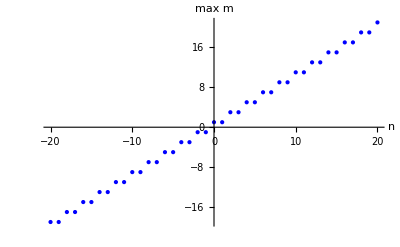

```mathematica
Mmax=50;ListPlot[Table[{n,2*Floor[n/2]+1},{n,-20,20}],PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"n","max m"},PlotRange->All]
```

```mathematica
1/4-1/12
```

1/6

## A_1 compactification with flux n=2 - qExpansion

### Dependence on m

```mathematica
gList=
```

{2,0,2}

```mathematica
Product[Product[gList[[i]]*gList[[j]],{i,gList}],{j,gList}]
```

16

```mathematica
f1[g_]:=(1/Theta1[Subscript[x, 1]^g*y^-1,q])^(g*Subscript[m, 1]-n);
f2[g_]:=(1/Theta1[Subscript[x, 2]^g*y^-1,q])^(g*Subscript[m, 2]-n);
f3[g1_,g2_]:=(1/Theta1[Subscript[x, 1]^g1*Subscript[x, 2]^g2*y^-1,q])^(2(g1*Subscript[m, 1]+g2*Subscript[m, 2]+n+1))
Z1loop=Product[f1[g]*f2[g],{g,{-2,0,2}}]*Product[f3[g1,g2],{g1,{-1,1}},{g2,{-1,1}}]//qExpand
```

q^(-4-3 n+1/2 (n-2 m_1)+1/2 (n+2 m_1)+1/2 (n-2 m_2)+1/2 (n+2 m_2)) (ⅈ/((1-1/q) (1-1/y) (1-1/(q y)) (1-q/y)))^(-2 n) y^(-n/4+1/8 (-n-2 m_1)+1/8 (-n+2 m_1)+1/8 (-n-2 m_2)+1/4 (1+n-m_1-m_2)+1/4 (1+n+m_1-m_2)+1/4 (1+n-m_1+m_2)+1/4 (1+n+m_1+m_2)+1/8 (-n+2 m_2)) (ⅈ/((1-1/q) (1-1/(y x_1^2)) (1-1/(q y x_1^2)) (1-q/(y x_1^2)) (1/x_1^2)^(1/8)))^(-n-2 m_1) (ⅈ/((1-1/q) (x_1^2)^(1/8) (1-x_1^2/y) (1-x_1^2/(q y)) (1-(q x_1^2)/y)))^(-n+2 m_1) (ⅈ/((1-1/q) (1-1/(y x_2^2)) (1-1/(q y x_2^2)) (1-q/(y x_2^2)) (1/x_2^2)^(1/8)))^(-n-2 m_2) (ⅈ/((1-1/q) (1-1/(y x_1 x_2)) (1-1/(q y x_1 x_2)) (1-q/(y x_1 x_2)) (1/(x_1 x_2))^(1/8)))^(2 (1+n-m_1-m_2)) (ⅈ/((1-1/q) (1-x_1/(y x_2)) (1-x_1/(q y x_2)) (1-(q x_1)/(y x_2)) (x_1/x_2)^(1/8)))^(2 (1+n+m_1-m_2)) (ⅈ/((1-1/q) (x_2/x_1)^(1/8) (1-x_2/(y x_1)) (1-x_2/(q y x_1)) (1-(q x_2)/(y x_1))))^(2 (1+n-m_1+m_2)) (ⅈ/((1-1/q) (x_1 x_2)^(1/8) (1-(x_1 x_2)/y) (1-(x_1 x_2)/(q y)) (1-(q x_1 x_2)/y)))^(2 (1+n+m_1+m_2)) (ⅈ/((1-1/q) (x_2^2)^(1/8) (1-x_2^2/y) (1-x_2^2/(q y)) (1-(q x_2^2)/y)))^(-n+2 m_2)

```mathematica
Ztest=ReplaceAll[Z1loop,
{Subscript[x, 1]->3,
Subscript[x, 2]->4,
y->1/2,
q->1/5}]//Simplify
```

2^(-5-(5 n)/4-34 m_2) 5^(8-n+4 m_1) 9^(6+9 n-13 m_1-2 m_2) 17^(-2-n-4 m_1-2 m_2) 43^(n+2 m_1) 49^(-3-2 n) 89^(n-2 m_1) 169^(-1-2 m_1+2 m_2) 841^(-1-n+m_1+m_2) 1369^(-1-n+m_1-m_2) 1643^(n-2 m_2) 190969^(-1-n-m_1-m_2) ⅇ^(-2 ⅈ π (n-m_1-2 m_2))

```mathematica
N[Ztest]//Simplify
```

5.13488×10^-12 ⅇ^((-43.3771+6.28319 ⅈ) m_1-(50.8238-12.5664 ⅈ) m_2)

Conclusion : there is a dependence on m

### Understanding the truncation for the case n = 2

```mathematica
Subscript[m, 1]=200;
Subscript[m, 2]=100;
mLength = √(Subscript[m, 1]^2+Subscript[m, 2]^2);
VectorList={{2,0},{0,2},{-2,0},{0,-2},{-1,1},{1,-1},{1,1},{-1,-1}};
eta={-Subscript[m, 1]/mLength,-Subscript[m, 2]/mLength};
```

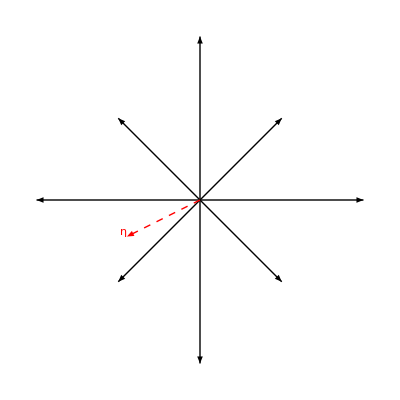

```mathematica
DrawVectors[{{2,0},{0,2},{-2,0},{0,-2},{-1,1},{1,-1},{1,1},{-1,-1}},eta]
```

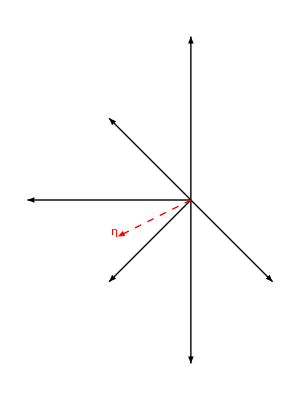

```mathematica
DrawVectors[{{0,2},{-2,0},{0,-2},{-1,1},{1,-1},{-1,-1}},eta]
```

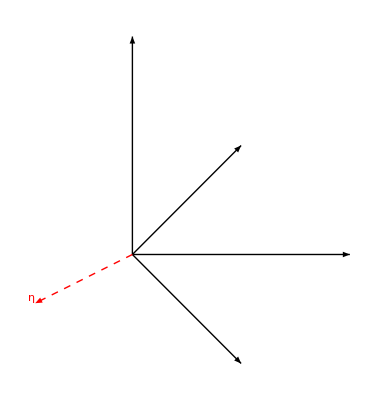

```mathematica
DrawVectors[{{0,2},{2,0},{1,1},{1,-1}},eta]
```

### Plot the region of (m_1,m_2) for which the residue contributes

```mathematica
n=0;
range=10;
regionCond2[{m1_,m2_}]:=(2m1-n>0&&2m2-n>0&&m1<=m2&&m2<0);  
regionCondSing2[{m1_,m2_}]:=m1>1/2 n&&m1<0&&m2==0;
regionCond4[{m1_,m2_}]:=(m1-m2+n+1>0)&&(m1+m2+n+1>0)&&m1<=m2&&m2<0;
regionCondSing4[{m1_,m2_}]:=(m1>-n-1&&m1<0&&m2==0);
regionCond5[{m1_,m2_}]:=(m1-m2+n+1>0)&&(2m2-n>0)&&m1<=m2&&m2<0;

integerPoints2=Select[Flatten[Table[{m1,m2},{m1,-range,0},{m2,-range,0}],1],regionCond2]
integerPointsSing2=Select[Flatten[Table[{m1,m2},{m1,-range,0},{m2,-range,0}],1],regionCondSing2]
integerPoints4=Select[Flatten[Table[{m1,m2},{m1,-range,0},{m2,-range,0}],1],regionCond4]
integerPointsSing4=Select[Flatten[Table[{m1,m2},{m1,-range,0},{m2,-range,0}],1],regionCondSing4]
integerPoints5=Select[Flatten[Table[{m1,m2},{m1,-range,0},{m2,-range,0}],1],regionCond5]

data1=integerPoints2;
data2=integerPoints4;
data3=integerPointsSing2;
data4=integerPointsSing4;
data5=integerPoints5;

datasets={};
If[data1=!={},AppendTo[datasets,data1]];
If[data2=!={},AppendTo[datasets,data2]];
If[data3=!={},AppendTo[datasets,data3]];
If[data4=!={},AppendTo[datasets,data4]];
If[data5=!={},AppendTo[datasets,data5]];

ListPlot[datasets,PlotStyle->{Red,Blue,Green,Yellow,Purple},PlotMarkers->{Style["●",20],Style["■",20],Style["■",20],Style["■",20],Style["■",20]}]
```

{}

{}

{}

«2 more identical outputs»

-Graphics-

### Finding the residue for n = 1 with expansion in q

#### Finding the residue for n = 1, (m_1,m_2)=(-1,0):

For this case, the JK residue is at a single point (u_1,u_2)=(-v,0)

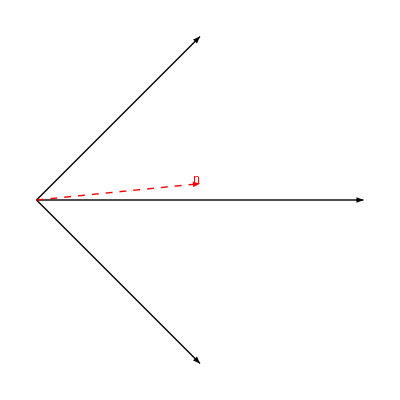

```mathematica
ϵ=0.1;
DrawVectors[{{1,-1},{1,1},{1,-1}+{1,1}},{1,ϵ}]
```

The flags are:
F_1=[Q_(1,-1),R^2], κ^F_1={Q_(1,-1), Q_(1,-1)+Q_(1,1)}
F_2=[Q_(1,1),R^2], κ^F_2={Q_(1,1), Q_(1,-1)+Q_(1,1)}
The relevant flag is F_2. The sign determinant is: ν(F_2)=-1. The residue is:
res_F_2 ω=Res_(u1,-1=0)Res_(u11=0)ω

We want to make a variable change in Z1loop :

```mathematica
Inverse[({{1, 1}, {1, -1}})]//MatrixForm
```

(1/2 | 1/2
1/2 | -1/2)

```mathematica
variableChange={Subscript[x, 1]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(1/2),Subscript[x, 2]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(-1/2)};
Z1looptilde=-1/2 ReplaceAll[Z1loop/.Subscript[x, 1]->Subscript[x, 1]*y^-1,variableChange]//Simplify
```

-(((-1+y)^8 (1+y)^6 (w_1-w_2)^2 (y w_1-w_2) (-w_1+y w_2) (y^2-w_1 w_2)^2 (y^3-w_1 w_2)^3)/(8 y^10 (y^2-w_1)^2 (-1+w_1)^6 (y^2-w_2)^2 (-1+w_2)^6 (y-w_1 w_2)))

```mathematica
Zresult=ContourInt[Z1looptilde,Subscript[w, 1],Subscript[w, 2]]
```

```mathematica
Zresult=Zresult // Simplify
```

1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14)

#### Finding the residue for n = 1, (m_1,m_2)=(0,-1):

For this case, the JK residue is at a single point (u_1,u_2)=(0,-v)

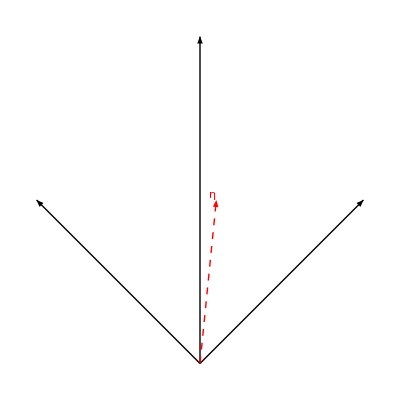

```mathematica
ϵ=0.1;
DrawVectors[{{1,1},{-1,1},{1,1}+{-1,1}},{ϵ,1}]
```

The flags are:
F_1=[Q_(1,1),R^2], κ^F_1={Q_(1,1), Q_(1,1)+Q_(-1,1)}
F_2=[Q_(-1,1),R^2], κ^F_2={Q_(-1,1), Q_(1,1)+Q_(-1,1)}
The relevant flag is F_1. The sign determinant is: ν(F_2)=+1. The residue is:
res_F_2 ω=Res_(u-1,1=0)Res_(u1+u2=0)ω

We want to make a variable change in Z1loop :

```mathematica
Inverse[({{1, 1}, {-1, 1}})]//MatrixForm
```

(1/2 | -1/2
1/2 | 1/2)

```mathematica
variableChange={Subscript[x, 1]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(-1/2),Subscript[x, 2]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(1/2)};
Z1looptilde=-1/2 ReplaceAll[Z1loop/.Subscript[x, 2]->Subscript[x, 2]*y^-1,variableChange]//Simplify
```

-(((-1+y)^8 (1+y)^6 (w_1-w_2)^2 (y w_1-w_2) (-w_1+y w_2) (y^2-w_1 w_2)^2 (y^3-w_1 w_2)^3)/(8 y^10 (y^2-w_1)^2 (-1+w_1)^6 (y^2-w_2)^2 (-1+w_2)^6 (y-w_1 w_2)))

```mathematica
Zresult=ContourInt[Z1looptilde,Subscript[w, 1],Subscript[w, 2]]
```

```mathematica
Zresult=Zresult//Simplify
```

1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14)

#### Finding the residue for n = 1, (m_1,m_2)=(0,0):

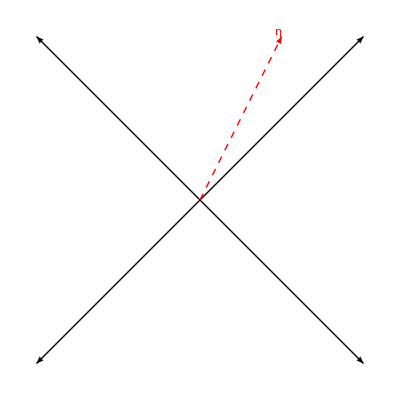

```mathematica
DrawVectors[{{-1,1},{1,-1},{1,1},{-1,-1}},{1/2,1}]
```

```mathematica
variableChange={Subscript[x, 1]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(-1/2),Subscript[x, 2]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(1/2)};
Z1looptilde=-1/2 ReplaceAll[Z1loop/.Subscript[x, 2]->Subscript[x, 2]*y^-1,variableChange]//Simplify
```

-(((-1+y)^8 (1+y)^6 (w_1-w_2)^2 (y w_1-w_2) (-w_1+y w_2) (y-w_1 w_2) (y^2-w_1 w_2)^2 (y^3-w_1 w_2))/(8 y^4 (y^2-w_1)^4 (-1+w_1)^4 (y^2-w_2)^4 (-1+w_2)^4))

```mathematica
Zresult=ContourInt[Z1looptilde,Subscript[w, 1],Subscript[w, 2]]
```

-1/(4 y^3 (1+y)^4)(-1+y)^2 (1+4 y+14 y^2+32 y^3+38 y^4+32 y^5+14 y^6+4 y^7+y^8)

#### Final result for the case n = 1

```mathematica
Zm11=1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14);
Zm00=-1/(4 y^3 (1+y)^4)(-1+y)^2 (1+4 y+14 y^2+32 y^3+38 y^4+32 y^5+14 y^6+4 y^7+y^8);
Zfinal=4*Zm11+Zm00//Simplify
```

1/(4 y^6)(-1+y)^2 (4+44 y+288 y^2+803 y^3+1512 y^4+1804 y^5+1512 y^6+803 y^7+288 y^8+44 y^9+4 y^10)

### Attempt to make the algorithm more generic

#### Helper Functions

We want to compute the residue for the generic case (m1, m2).
(1) Input: 
	- hyperplanes (R,Q,K)
	- η
(2) Find the relevant singular points.
(3) For each point,  find the relevant flags.
(4) Compute the residue for the corresponding flag with correct sign.
(5) Sum the residues.

```mathematica
(*Draw a list of vectors and eta*)
DrawVectors[VectorList_,eta_]:=
Graphics[
{
(*Plot charge covectors*)
Table[Arrow[{{0,0},{VectorList[[j]][[1]],VectorList[[j]][[2]]}}]
,{j,1,Dimensions[VectorList][[1]]}],

(*Plot eta*)
Red,Dashed,Arrow[{{0,0},{eta[[1]],eta[[2]]}}],Text["η",{eta[[1]],eta[[2]]},{1,-1}]
}];

(*Check if eta is in the cone ={vec1,vec2}*)
IsInCone[cone_,eta_]:=Module[{proj},
proj =Inverse[Transpose[cone]].eta;
AllTrue[proj,Positive]
];

(*Check if two vectors are colinear*)
ColinearQ[u_,v_]:=VectorAngle[u,v]==0||VectorAngle[u,v]==Pi;

(*Returns singular points and singular planes*)
SingularPoints[Qcovectors_,SymCovectors_]:=Module[{ptsList},
ptsList={};
Do[
If[i<j,
If[!ColinearQ[Qcovectors[[i]],Qcovectors[[j]]],

point=LinearSolve[{Qcovectors[[i]],Qcovectors[[j]]},-{SymCovectors[[i]],SymCovectors[[j]]}];
AppendTo[ptsList,{point,{i,j}}]
]
]

,{i,1,Length[Qcovectors]}
,{j,1,Length[Qcovectors]}
];

KeyValueMap[{#1,Union@@#2}&,GroupBy[ptsList,First->Last]]

]

(*Returns relevant singular points and singular planes wrt eta*)
RelevantSingularPoints[Qcovectors_,SymCovectors_,eta_]:=Module[{pointsList,singPts,isRelevant},
pointsList={};
singPts=SingularPoints[Qcovectors,SymCovectors];

Do[
(*Check if the point is relevant wrt eta*)
isRelevant=False;
Do[
If[j<k,
If[IsInCone[{Qcovectors[[j]],Qcovectors[[k]]},eta],
isRelevant=True]
]
,{j,singPts[[i]][[2]]},{k,singPts[[i]][[2]]}];

(*If relevant, add it to the list*)
If[isRelevant,
AppendTo[pointsList,singPts[[i]]]
];

,{i,1,Length[singPts]}];

pointsList
]

(*A function that draw lines as a function of Qcovectors and symmetry charges*)
DrawLines[Qcovectors_,SymCovectors_,{xMin_,xMax_},{yMin_,yMax_}]:=Module[{pts,lines},
lines=MapThread[Append,{Qcovectors,SymCovectors}];pts=Table[Module[{α=line[[1]],β=line[[2]],γ=line[[3]]},If[β!=0,(*Non-vertical:compute endpoints*)Line[{{xMin,-(α xMin+γ)/β},{xMax,-(α xMax+γ)/β}}],(*Vertical line:x=-γ/α*)Line[{{-γ/α,yMin},{-γ/α,yMax}}]]],{line,lines}];
Graphics[pts,Axes->True]]

(*A function that draw lines and singular points as a function of Qcovectors and symmetry charges*)
PlotSingularPoints[Qcovectors_,SymCovectors_]:=Module[{singPts},
singPts=SingularPoints[Qcovectors,SymCovectors];
Show[DrawLines[Qcovectors,SymCovectors,{-2,2},{-2,2}],ListPlot[First/@singPts]]
];

(*Check if a vector is in the span of vecs*)
InSpanQ[v_,vecs_List]:=If[Length[v]==Length[vecs[[1]]],VectorQ[Quiet[LinearSolve[Transpose[vecs],v]]],False]

(*Create an array of flags and kappa. Returns {flags, kappa}*)
FlagList[Qstar_]:=Module[{AccumulateList},

permutations=Permutations[Range[Length[Qstar]],{Length[Qstar[[1]]]}];
AccumulateList[list_]:=Table[Take[list,i],{i,Length[list]}];

flags=Table[
AccumulateList[permutations[[i]]]
,{i,1,Length[permutations]}];

Do[
Do[
Do[
If[InSpanQ[Qstar[[k]],Qstar[[flags[[i]][[j]]]]],
flags[[i]][[j]]=Union[flags[[i]][[j]],{k}]
]
,{j,1,Length[flags[[i]]]}]
,{i,1,Length[flags]}]
,{k,1,Length[Qstar]}];
flags=DeleteDuplicates[flags];
kappa=Table[
Table[
Sum[Qstar[[k]],{k,flags[[i]][[j]]}]
,{j,1,Length[flags[[i]]]}]
,{i,1,Length[flags]}];

{flags,kappa}
];

(*Output the positive flags*)
PositiveFlags[Qstar_,eta_]:=Module[{},
{flags,kappa}=FlagList[Qstar];
newflags={};
newkappa={};
Do[
If[IsInCone[kappa[[i]],eta],
newflags=Append[newflags,flags[[i]]];
newkappa=Append[newkappa,kappa[[i]]];
]
,{i,1,Length[flags]}];

{newflags,newkappa}
]

(*Given a flag F, returns an ordered set of covectors Subscript[Q, i] such that Subscript[Q, i]∈Subscript[F, i]*)
OrderedSet[flag_]:=Module[{orderedList={}},
AppendTo[orderedList,flag[[1,1]]];
Do[
AppendTo[orderedList,Part[Complement[flag[[i]],flag[[i-1]]],1]];
,{i,2,Length[flag]}];
orderedList
]
```

#### Testing arena

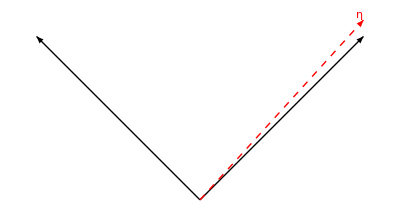

True

```mathematica
ϵ=0.1;
cone={{1,1},{-1,1}};
eta={1,1+ϵ};
DrawVectors[cone,eta]
IsInCone[cone,eta]
```

```mathematica
Qcovectors={{2,0},{-2,0},{0,2},{0,-2},{1,1},{1,-1},{-1,1},{-1,-1}};
SymCovectors={-1,-1,-1,-1,1,1,1,1};
```

```mathematica
RelevantChargesRank2[m1_,m2_,n_]:=Module[{chargeList},
chargeList={};
Do[
If[g*m1-n>0,
AppendTo[chargeList,{{g,0},-1}]];
If[g*m2-n>0,
AppendTo[chargeList,{{0,g},-1}]];
,{g,{-2,2}}];

Do[
If[g1*m1+g2*m2+n+1>0,
AppendTo[chargeList,{{g1,g2},1}]]
,{g1,{-1,1}},{g2,{-1,1}}];

chargeList
]
```

Testing the case (m1,m2)=(-1,0)

```mathematica
eta={1,ϵ}
```

{1,0.1}

```mathematica
hyperplanes=RelevantChargesRank2[-1,0,1]
```

{{{-2,0},-1},{{-1,-1},1},{{-1,1},1},{{1,-1},1},{{1,1},1}}

```mathematica
Qlist=First/@hyperplanes
Slist=Last/@hyperplanes;
singPts=RelevantSingularPoints[Qlist,Slist,eta]
```

{{-2,0},{-1,-1},{-1,1},{1,-1},{1,1}}

{{{-1,0},{4,5}}}

```mathematica
(* Run over singular points*)
i=1;
point=singPts[[i,1]];
Qstar=Qlist[[singPts[[i,2]]]];
Sstar=Slist[[singPts[[i,2]]]];
{flags,kappas}=PositiveFlags[Qstar,eta];
flags
kappas
```

{{{2},{1,2}}}

{{{1,1},{2,0}}}

```mathematica
(* Run over positive flags*)
j=1;
flag=flags[[j]]
kappa=kappas[[j]]
```

{{2},{1,2}}

{{1,1},{2,0}}

```mathematica
Blist=OrderedSet[flag]
```

{2,1}

```mathematica
covectors=Qstar[[Blist]]
```

{{1,1},{1,-1}}

```mathematica
(*Shift Z1loop to the origin of the singular point*)
coordShift=Table[Subscript[x, coordidx]->Subscript[x, coordidx]*y^point[[coordidx]],{coordidx,Length[point]}];
Z1loop=Z1loop/.coordShift//Simplify;
```

```mathematica
(*Rotate coordinates of Z1loop for the residue operation*)
covectorsInv=Inverse[covectors];
coordRotation=Table[Subscript[x, k]->∏_(l=1)^Length[covectors] Subscript[w, l]^covectorsInv[[k,l]],{k,Length[covectors]}];
Z1loop=Z1loop/.coordRotation//Simplify
```

((-1+y)^8 (1+y)^6 (w_1-w_2)^2 (y w_1-w_2) (-w_1+y w_2) (y^2-w_1 w_2)^2 (y^3-w_1 w_2)^3)/(4 y^10 (y^2-w_1)^2 (-1+w_1)^6 (y^2-w_2)^2 (-1+w_2)^6 (y-w_1 w_2))

```mathematica
Z1loop=Z1loop*Det[covectorsInv]
```

-(((-1+y)^8 (1+y)^6 (w_1-w_2)^2 (y w_1-w_2) (-w_1+y w_2) (y^2-w_1 w_2)^2 (y^3-w_1 w_2)^3)/(8 y^10 (y^2-w_1)^2 (-1+w_1)^6 (y^2-w_2)^2 (-1+w_2)^6 (y-w_1 w_2)))

```mathematica
Zresult=ContourInt[Z1loop,Subscript[w, 1],Subscript[w, 2]]//Simplify
```

1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14)

```mathematica
Zresult==1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14)//Simplify
```

True

```mathematica
(*Hurray !*)
```

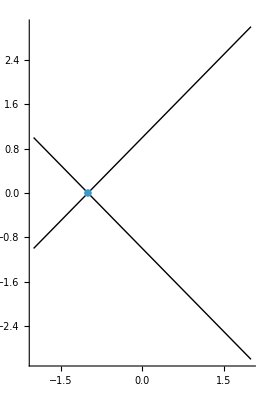

{{{1/2,1/2},{1,3,7}},{{1/2,-1/2},{1,4,8}},{{1/2,-3/2},{1,5}},{{1/2,3/2},{1,6}},{{-1/2,1/2},{2,3,6}},{{-1/2,-1/2},{2,4,5}},{{-1/2,3/2},{2,7}},{{-1/2,-3/2},{2,8}},{{-3/2,1/2},{3,5}},{{3/2,1/2},{3,8}},{{-3/2,-1/2},{4,6}},{{3/2,-1/2},{4,7}},{{-1,0},{5,6}},{{0,-1},{5,8}},{{0,1},{6,7}},{{1,0},{7,8}}}

```mathematica
PlotSingularPoints[QlistRelevant,SlistRelevant]
```

```mathematica
Qstar
```

{{1,0},{0,1},{1,-2}}

```mathematica
{f,k}=FlagList[Qstar];
f
k
```

{{{1},{1,2,3}},{{2},{1,2,3}},{{3},{1,2,3}}}

{{{1,0},{2,-1}},{{0,1},{2,-1}},{{1,-2},{2,-1}}}

```mathematica
{f,k}=PositiveFlags[Qstar,{1,-ϵ}];
f
k
```

{{{1},{1,2,3}},{{2},{1,2,3}}}

{{{1,0},{2,-1}},{{0,1},{2,-1}}}

```mathematica
?JacobiTheta
```

Missing[UnknownSymbol,JacobiTheta]

```mathematica
JacobiTheta
```

JacobiTheta

```mathematica
EllipticTheta[1,u,q] + EllipticTheta[1,-u,q] // Simplify
```

EllipticTheta[1,-u,q]+EllipticTheta[1,u,q]

```mathematica
D[EllipticTheta[1, z, Exp[I Pi τ]], z] /. z -> 0
```

EllipticThetaPrime[1,0,ⅇ^(ⅈ π τ)]

```mathematica
FullSimplify[D[EllipticTheta[1, z, Exp[I Pi τ]], z] /. z -> 0, 
 Assumptions -> Im[τ] > 0]
```

EllipticThetaPrime[1,0,ⅇ^(ⅈ π τ)]

```mathematica
FullSimplify[EllipticThetaPrime[1,0,Exp[I Pi τ]]/(2*π*DedekindEta[ τ]^3),Assumptions->Im[τ>0]]
```

EllipticThetaPrime[1,0,ⅇ^(ⅈ π τ)]/(2 π DedekindEta[τ]^3)

### Finding the residue for n = 1 analytically

#### Writting Z1loop

```mathematica
Nmax=0;
Z1loop=Z1loopExpression[0,0,1]
```

-((Theta1[1/y^2]^6 Theta1[1/y]^2 Theta1[1/x_1^2] Theta1[1/(y x_1^2)] Theta1[x_1^2] Theta1[x_1^2/y] Theta1[1/x_2^2] Theta1[1/(y x_2^2)] Theta1[x_2^2] Theta1[x_2^2/y])/(4 Theta1[1/(y x_1 x_2)]^4 Theta1[x_1/(y x_2)]^4 Theta1[x_2/(y x_1)]^4 Theta1[(x_1 x_2)/y]^4))

```mathematica
Z1loop=Z1loop//Simplify//qExpand
```

((-1+y)^8 (1+y)^6 x_1 (-1+x_1^2)^2 (-y x_1+x_1^3)^3 x_2^4 (y-x_2^2) (-1+x_2^2)^2 (-1+y x_2^2))/(4 y (-1+y x_1^2) (-y x_1+x_2)^6 (x_1-y x_2)^2 (y-x_1 x_2)^2 (-1+y x_1 x_2)^6)

```mathematica
Z1loopTranspose=Z1loop/.Subscript[x, 1]->Subscript[temp, 1]/.Subscript[x, 2]->Subscript[temp, 2];
Z1loopTranspose=Z1loopTranspose/.Subscript[temp, 1]->Subscript[x, 2]/.Subscript[temp, 2]->Subscript[x, 1];
```

```mathematica
Z1loopTranspose==Z1loop//Simplify
```

True

#### Finding the residue for n = 1, (m_1,m_2)=(-1,0):

For this case, the JK residue is at a single point (u_1,u_2)=(-v,0)

```mathematica
ϵ=0.1;
DrawVectors[{{1,-1},{1,1},{1,-1}+{1,1}},{1,ϵ}]
```

-Graphics-

The flags are:
F_1=[Q_(1,-1),R^2], κ^F_1={Q_(1,-1), Q_(1,-1)+Q_(1,1)}
F_2=[Q_(1,1),R^2], κ^F_2={Q_(1,1), Q_(1,-1)+Q_(1,1)}
The relevant flag is F_2. The sign determinant is: ν(F_2)=-1. The residue is:
res_F_2 ω=Res_(u1,-1=0)Res_(u11=0)ω

We want to make a variable change in Z1loop :

```mathematica
Inverse[({{1, 1}, {1, -1}})]//MatrixForm
```

(1/2 | 1/2
1/2 | -1/2)

```mathematica
Theta
```

```mathematica
variableChange={Subscript[x, 1]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(1/2),Subscript[x, 2]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(-1/2)};
Z1looptilde=-1/2 ReplaceAll[Z1loop/.Subscript[x, 1]->Subscript[x, 1]*y^-1,variableChange]
```

(Theta1[1/y^2]^6 Theta1[1/y]^2 Theta1[y^2/(w_1 w_2)] Theta1[w_1/w_2] Theta1[w_1/(y w_2)]^3 Theta1[w_2/w_1] Theta1[(w_1 w_2)/y^3]^3 Theta1[(w_1 w_2)/y^2])/(8 Theta1[1/w_1]^6 Theta1[w_1/y^2]^2 Theta1[1/w_2]^6 Theta1[y/(w_1 w_2)] Theta1[w_2/y^2]^2 Theta1[w_2/(y w_1)])

```mathematica
Zresult=ContourInt[Z1looptilde,Subscript[w, 1],Subscript[w, 2]]
```

```mathematica
Zresult=Zresult // Simplify
```

1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14)

#### Finding the residue for n = 1, (m_1,m_2)=(0,-1):

For this case, the JK residue is at a single point (u_1,u_2)=(0,-v)

```mathematica
ϵ=0.1;
DrawVectors[{{1,1},{-1,1},{1,1}+{-1,1}},{ϵ,1}]
```

-Graphics-

The flags are:
F_1=[Q_(1,1),R^2], κ^F_1={Q_(1,1), Q_(1,1)+Q_(-1,1)}
F_2=[Q_(-1,1),R^2], κ^F_2={Q_(-1,1), Q_(1,1)+Q_(-1,1)}
The relevant flag is F_1. The sign determinant is: ν(F_2)=+1. The residue is:
res_F_2 ω=Res_(u-1,1=0)Res_(u1+u2=0)ω

We want to make a variable change in Z1loop :

```mathematica
Inverse[({{1, 1}, {-1, 1}})]//MatrixForm
```

(1/2 | -1/2
1/2 | 1/2)

```mathematica
variableChange={Subscript[x, 1]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(-1/2),Subscript[x, 2]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(1/2)};
Z1looptilde=-1/2 ReplaceAll[Z1loop/.Subscript[x, 2]->Subscript[x, 2]*y^-1,variableChange]//Simplify
```

-(((-1+y)^8 (1+y)^6 (w_1-w_2)^2 (y w_1-w_2) (-w_1+y w_2) (y^2-w_1 w_2)^2 (y^3-w_1 w_2)^3)/(8 y^10 (y^2-w_1)^2 (-1+w_1)^6 (y^2-w_2)^2 (-1+w_2)^6 (y-w_1 w_2)))

```mathematica
Zresult=ContourInt[Z1looptilde,Subscript[w, 1],Subscript[w, 2]]
```

```mathematica
Zresult=Zresult//Simplify
```

1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14)

#### Finding the residue for n = 1, (m_1,m_2)=(0,0):

```mathematica
DrawVectors[{{-1,1},{1,-1},{1,1},{-1,-1}},{1/2,1}]
```

DrawVectors[{{-1,1},{1,-1},{1,1},{-1,-1}},{1/2,1}]

```mathematica
thetaSimplify=Theta1[x_^exponent_]:>-Theta1[x^(-exponent)]/;exponent<0
```

Theta1[x_^exponent_]:>-Theta1[x^-exponent]/;exponent<0

```mathematica
variableChange={Subscript[x, 1]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(-1/2),Subscript[x, 2]->Subscript[w, 1]^(1/2)*Subscript[w, 2]^(1/2)};
Z1looptilde=-1/2 ReplaceAll[Z1loop/.Subscript[x, 2]->Subscript[x, 2]*y^-1,variableChange]//.thetaSimplify
```

(Theta1[y]^2 Theta1[y^2]^6 Theta1[y/(w_1 w_2)] Theta1[y^2/(w_1 w_2)] Theta1[w_1/w_2] Theta1[w_1/(y w_2)] Theta1[w_2/w_1] Theta1[w_2/(y w_1)] Theta1[(w_1 w_2)/y^3] Theta1[(w_1 w_2)/y^2])/(8 Theta1[w_1]^4 Theta1[w_1/y^2]^4 Theta1[w_2]^4 Theta1[w_2/y^2]^4)

```mathematica
Zresult=ContourInt[Z1looptilde,Subscript[w, 1],Subscript[w, 2]]
```

-1/(4 y^3 (1+y)^4)(-1+y)^2 (1+4 y+14 y^2+32 y^3+38 y^4+32 y^5+14 y^6+4 y^7+y^8)

#### Final result for the case n = 1

```mathematica
Zm11=1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14);
Zm00=-1/(4 y^3 (1+y)^4)(-1+y)^2 (1+4 y+14 y^2+32 y^3+38 y^4+32 y^5+14 y^6+4 y^7+y^8);
Zfinal=4*Zm11+Zm00//Simplify
```

1/(4 y^6)(-1+y)^2 (4+44 y+288 y^2+803 y^3+1512 y^4+1804 y^5+1512 y^6+803 y^7+288 y^8+44 y^9+4 y^10)

#### Result for the case n = 0

Comparing the result with the analytic computation:

```mathematica
Nmax=2
```

2

```mathematica
Zexpand=Z1loop//qForm//qExpand
```

((-1+y^2)^2 (w_1-w_2)^2 (y^2-w_1 w_2)^2)/(4 q^(1/4) (y^2-w_1)^2 (-1+w_1)^2 (y^2-w_2)^2 (-1+w_2)^2)+(q^(3/4) (1-1/y^2)^2 y^6 (1-y^2/(w_1 w_2)) (1-w_1/w_2) (1-w_2/w_1) (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2+(2 y^2)/w_2-(2 y^2)/(w_1 w_2)-(2 w_1)/w_2+2 w_2+(2 w_2)/y^2-(2 w_2)/w_1-(2 w_1 w_2)/y^2) (1-(w_1 w_2)/y^2))/(4 (1-1/w_1)^2 (1-y^2/w_1)^2 w_1^2 (1-1/w_2)^2 (1-y^2/w_2)^2 w_2^2)+(q^(7/4) (1-1/y^2)^2 y^6 (1-y^2/(w_1 w_2)) (1-w_1/w_2) (1-w_2/w_1) (1-(w_1 w_2)/y^2) (5+1/y^4-6/y^2-2 y^2-2 (2-2/y^2) y^2+y^4+3/w_1^2+(3 y^4)/w_1^2+2/w_1+(2 y^2)/w_1+(2 (2-2/y^2-2 y^2))/w_1+(2 y^2 (2-2/y^2-2 y^2+2/w_1))/w_1+2 w_1+(2 w_1)/y^2+2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1) w_1+3 w_1^2+(3 w_1^2)/y^4+(2 w_1 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1))/y^2+3/w_2^2+(3 y^4)/w_2^2+y^4/(w_1^2 w_2^2)+w_1^2/w_2^2+2/w_2+(2 y^2)/w_2-(2 y^2)/(w_1 w_2)-(2 w_1)/w_2+(2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2))/w_2+(2 y^2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2))/w_2-(2 y^2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2+(2 y^2)/w_2))/(w_1 w_2)-(2 w_1 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2+(2 y^2)/w_2-(2 y^2)/(w_1 w_2)))/w_2+2 w_2+(2 w_2)/y^2-(2 w_2)/w_1-(2 w_1 w_2)/y^2+2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2+(2 y^2)/w_2-(2 y^2)/(w_1 w_2)-(2 w_1)/w_2) w_2+3 w_2^2+(3 w_2^2)/y^4+w_2^2/w_1^2+(w_1^2 w_2^2)/y^4+1/y^2 2 w_2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2+(2 y^2)/w_2-(2 y^2)/(w_1 w_2)-(2 w_1)/w_2+2 w_2)-1/w_1 2 w_2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2+(2 y^2)/w_2-(2 y^2)/(w_1 w_2)-(2 w_1)/w_2+2 w_2+(2 w_2)/y^2)-1/y^2 2 w_1 w_2 (2-2/y^2-2 y^2+2/w_1+(2 y^2)/w_1+2 w_1+(2 w_1)/y^2+2/w_2+(2 y^2)/w_2-(2 y^2)/(w_1 w_2)-(2 w_1)/w_2+2 w_2+(2 w_2)/y^2-(2 w_2)/w_1)))/(4 (1-1/w_1)^2 (1-y^2/w_1)^2 w_1^2 (1-1/w_2)^2 (1-y^2/w_2)^2 w_2^2)

```mathematica
ResultQexpand=ContourInt[Zexpand,Subscript[w, 1],Subscript[w, 2]]
```

-(1+6 q+27 q^2)/(2 q^(1/4))

```mathematica
ResultAnalytic=-1/(2(2π*Eta[q]^3)^2)//qExpand
```

-1/(8 π^2 q^(1/4))-(3 q^(3/4))/(4 π^2)-(27 q^(7/4))/(8 π^2)

```mathematica
ResultAnalytic/ResultQexpand//Simplify
```

1/(4 π^2)

```mathematica
D[f[z]/h[z]^4,{z,3}]/. h'[z]->0/. Derivative[3][h][z]->0
```

-(12 f'[z] h''[z])/h[z]^5+(f^(3)[z])/h[z]^4

```mathematica
D[f[-z],z]
```

-f'[-z]

```mathematica
Z
```

```mathematica
myFunc=Z1loop
```

-((Theta1[y^2]^2 Theta1[y^2/(w_1 w_2)] Theta1[w_1/w_2] Theta1[w_2/w_1] Theta1[(w_1 w_2)/y^2])/(4 Theta1[w_1]^2 Theta1[w_1/y^2]^2 Theta1[w_2]^2 Theta1[w_2/y^2]^2))

```mathematica
myFuncorder2=Coefficient[myFunc,Θ[Subscript[u, 1]],-2]
myFuncDer=D[myFuncorder2,Subscript[u, 1]]/.Subscript[u, 1]->0/.simplifyRule
```

-((Θ[2 v]^2 Θ[2 v-u_1-u_2] Θ[u_1-u_2] Θ[-u_1+u_2] Θ[-2 v+u_1+u_2])/(4 Θ[-2 v+u_1]^2 Θ[u_2]^2 Θ[-2 v+u_2]^2))

(Θ[2 v-u_2] Θ'[2 v])/(2 Θ[2 v] Θ[-2 v+u_2])-Θ'[2 v-u_2]/(4 Θ[-2 v+u_2])-(Θ[2 v-u_2] Θ'[u_2])/(2 Θ[u_2] Θ[-2 v+u_2])+(Θ[2 v-u_2] Θ'[-2 v+u_2])/(4 Θ[-2 v+u_2]^2)

```mathematica
FisrtResidue=1/(Derivative[1][Θ][0])^2*myFuncDer
```

((Θ[2 v-u_2] Θ'[2 v])/(2 Θ[2 v] Θ[-2 v+u_2])-Θ'[2 v-u_2]/(4 Θ[-2 v+u_2])-(Θ[2 v-u_2] Θ'[u_2])/(2 Θ[u_2] Θ[-2 v+u_2])+(Θ[2 v-u_2] Θ'[-2 v+u_2])/(4 Θ[-2 v+u_2]^2))/Θ'[0]^2

```mathematica
ResidueFormula[2]
```

f'[z]/h[z]^2

```mathematica
Coefficient[FisrtResidue,Θ[Subscript[u, 2]],-1]/(Derivative[1][Θ][0])/.Subscript[u, 2]->0/.simplifyRule
```

1/(2 Θ'[0]^2)

```mathematica
ResidueFormula[1]
```

f[z]/h[z]

```mathematica
D[order2,Subscript[u, 2]]/.Subscript[u, 2]->0/.simplifyRule
```

-2 Θ[v]^3 Θ[3 v] Θ'[v]^2+(4 Θ[v]^4 Θ[3 v] Θ'[v] Θ'[2 v])/Θ[2 v]-(2 Θ[v]^5 Θ[3 v] Θ'[2 v]^2)/Θ[2 v]^2-2 Θ[v]^4 Θ'[v] Θ'[3 v]+(4 Θ[v]^5 Θ'[2 v] Θ'[3 v])/Θ[2 v]+Θ[v]^4 Θ[3 v] Θ''[v]-(2 Θ[v]^5 Θ[3 v] Θ''[2 v])/Θ[2 v]-Θ[v]^5 Θ''[3 v]

```mathematica
order3=Coefficient[myFuncDer,Θ[Subscript[u, 2]],-3]
```

1/Θ[-2 v+u_2]^3 Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[v-u_2] Θ[2 v-u_2] Θ[-3 v+u_2] Θ[-v+u_2] Θ'[-u_2]+1/Θ[-2 v+u_2]^3 Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[v-u_2] Θ[2 v-u_2] Θ[-3 v+u_2] Θ[-v+u_2] Θ'[u_2]

```mathematica
order=3;
D[f[z]/h[z]^order,{z,order-1}]/. h'[z]->0/. Derivative[3][h][z]->0/. Derivative[5][h][z]->0
```

f''[z]/h[z]^3-(3 f[z] h''[z])/h[z]^4

```mathematica
(order3/.Subscript[u, 2]->0/.simplifyRule)*(-3*Θ'''[0]/(Θ'[0])^4)
```

-(6 Θ[v]^5 Θ[3 v] Θ'''[0])/Θ'[0]^3

```mathematica
(D[order3,{Subscript[u, 2],2}]/.Subscript[u, 2]->0/.simplifyRule)*(1/(Θ'[0])^3)/.simplifyRule
```

ReplaceAll::reps: {simplifyRule} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(0/.simplifyRule)/Θ'[0]^3/.simplifyRule

## A_1 compactification with flux n=2

### Find Z1loop and hyperplanes

```mathematica
Z1loopExpression[m1_,m2_,n_]:=Module[{Z,f1,f2,f3},
f1[g_]:=(1/Theta1[Subscript[x, 1]^g*y^-1])^(g*m1-n);
f2[g_]:=(1/Theta1[Subscript[x, 2]^g*y^-1])^(g*m2-n);
f3[g1_,g2_]:=(1/Theta1[Subscript[x, 1]^g1*Subscript[x, 2]^g2*y])^(2(g1*m1+g2*m2+n+1));
Z=Product[f1[g]*f2[g],{g,{-2,0,2}}]*Product[f3[g1,g2],{g1,{-1,1}},{g2,{-1,1}}];
Z=Z*1/4*ⅈ^2*Eta^4*(1/Theta1[y^-2])^(2*(-2n-1))*∏_(i=1)^2 (Theta1[Subscript[x, i]^2]*Theta1[Subscript[x, i]^-2])/(ⅈ*Eta)^2;
Z
]
FindHyperplanes[m1_,m2_,n_]:=Module[{Qcovectors={},Scovectors={}},
Do[
If[g*m1-n>0,
Do[
AppendTo[Qcovectors,{g,0}];
AppendTo[Scovectors,-v-(a+b*τ)];
,{a,{0,1}},{b,{0,1}}]
];
If[g*m2-n>0,
Do[
AppendTo[Qcovectors,{0,g}];
AppendTo[Scovectors,-v-(a+b*τ)];
,{a,{0,1}},{b,{0,1}}]
];
,{g,{-2,2}}];

Do[
If[2(g1*m1+g2*m2+n+1)>0,
AppendTo[Qcovectors,{g1,g2}];
AppendTo[Scovectors,v];
];
,{g1,{-1,1}},{g2,{-1,1}}];

{Qcovectors,Scovectors}
]
```

### JK residue

#### Case n = 1

```mathematica
Z1loopExpression[0,0,1]
```

-((Theta1[1/y^2]^6 Theta1[1/y]^2 Theta1[1/x_1^2] Theta1[1/(y x_1^2)] Theta1[x_1^2] Theta1[x_1^2/y] Theta1[1/x_2^2] Theta1[1/(y x_2^2)] Theta1[x_2^2] Theta1[x_2^2/y])/(4 Theta1[y/(x_1 x_2)]^4 Theta1[(y x_1)/x_2]^4 Theta1[(y x_2)/x_1]^4 Theta1[y x_1 x_2]^4))

```mathematica
Listm={{0,0},{1,0},{-1,0},{0,1},{0,-1}};
n=1;

ListZ1loop={};
Do[

{m1,m2}=Listm[[i]];
Z1loop=Z1loopExpression[m1,m2,n];
{Qcovectors,Scovectors}=FindHyperplanes[m1,m2,n];
ϵ=0.1;
eta=-{m1,m2}+{ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}]
```

```mathematica
Z1loop=Flatten[ListZ1loop][[Range[2,5]]]//Total
```

-((Theta1[1/y^2]^6 Theta1[1/y]^2 Theta1[y^2/(w_1 w_2)] Theta1[w_1/w_2] Theta1[w_1/(y w_2)] Theta1[w_2/w_1] Theta1[w_2/(y w_1)] Theta1[(w_1 w_2)/y^3]^3 Theta1[(w_1 w_2)/y^2])/(2 Theta1[y^2/w_1]^6 Theta1[w_1]^2 Theta1[y^2/w_2]^6 Theta1[y/(w_1 w_2)] Theta1[w_2]^2))

```mathematica
Z1loopLinear=LinearizeWs[ThetaLinearize[Z1loop/.replacementRule]]/.simplifyRule
```

-((Θ[v]^2 Θ[2 v]^6 Θ[2 v-u_1-u_2] Θ[u_1-u_2] Θ[-v+u_1-u_2] Θ[-u_1+u_2] Θ[-v-u_1+u_2] Θ[-3 v+u_1+u_2]^3 Θ[-2 v+u_1+u_2])/(2 Θ[2 v-u_1]^6 Θ[u_1]^2 Θ[2 v-u_2]^6 Θ[v-u_1-u_2] Θ[u_2]^2))

```mathematica
Z1loopLinearU1=Order2Residue[Z1loopLinear,Subscript[u, 1]]//Thread
```

1/(4 Eta^6 π^2)((3 Θ[v]^2 Θ[-v-u_2] Θ[-3 v+u_2]^3 Θ[-2 v+u_2] Θ[-v+u_2] Θ'[2 v])/(Θ[2 v] Θ[v-u_2] Θ[2 v-u_2]^5)+(Θ[v]^2 Θ[-3 v+u_2]^3 Θ[-2 v+u_2] Θ[-v+u_2] Θ'[-v-u_2])/(2 Θ[v-u_2] Θ[2 v-u_2]^5)+(Θ[v]^2 Θ[-v-u_2] Θ[-3 v+u_2]^3 Θ[-2 v+u_2] Θ[-v+u_2] Θ'[v-u_2])/(2 Θ[v-u_2]^2 Θ[2 v-u_2]^5)-(Θ[v]^2 Θ[-v-u_2] Θ[-3 v+u_2]^3 Θ[-2 v+u_2] Θ[-v+u_2] Θ'[2 v-u_2])/(2 Θ[v-u_2] Θ[2 v-u_2]^6)-(Θ[v]^2 Θ[-v-u_2] Θ[-3 v+u_2]^3 Θ[-2 v+u_2] Θ[-v+u_2] Θ'[u_2])/(Θ[v-u_2] Θ[2 v-u_2]^5 Θ[u_2])+(3 Θ[v]^2 Θ[-v-u_2] Θ[-3 v+u_2]^2 Θ[-2 v+u_2] Θ[-v+u_2] Θ'[-3 v+u_2])/(2 Θ[v-u_2] Θ[2 v-u_2]^5)+(Θ[v]^2 Θ[-v-u_2] Θ[-3 v+u_2]^3 Θ[-v+u_2] Θ'[-2 v+u_2])/(2 Θ[v-u_2] Θ[2 v-u_2]^5)-(Θ[v]^2 Θ[-v-u_2] Θ[-3 v+u_2]^3 Θ[-2 v+u_2] Θ'[-v+u_2])/(2 Θ[v-u_2] Θ[2 v-u_2]^5))

```mathematica
((Coefficient[Z1loopLinearU1,Θ[Subscript[u, 2]],-1]*1/(2π*Eta^3))/.Subscript[u, 2]->0)/.simplifyRule
```

-(Θ[v]^3 Θ[3 v]^3)/(4 Eta^6 π^2 Θ[2 v]^4)

```mathematica
ResidueFormula[4]
```

-(12 f'[z] h''[z])/h[z]^5+(f^(3)[z])/h[z]^4

```mathematica
Z1loopLinear=LinearizeWs[ThetaLinearize[Flatten[ListZ1loop][[1]]/.replacementRule]]
```

-((Θ[-2 v]^6 Θ[-v]^2 Θ[v-u_1-u_2] Θ[2 v-u_1-u_2] Θ[u_1-u_2] Θ[-v+u_1-u_2] Θ[-u_1+u_2] Θ[-v-u_1+u_2] Θ[-3 v+u_1+u_2] Θ[-2 v+u_1+u_2])/(8 Θ[2 v-u_1]^4 Θ[u_1]^4 Θ[2 v-u_2]^4 Θ[u_2]^4))

```mathematica
f=Coefficient[Z1loopLinear,Θ[Subscript[u, 1]],-4]
h=2π*Eta^3
```

-((Θ[-2 v]^6 Θ[-v]^2 Θ[v-u_1-u_2] Θ[2 v-u_1-u_2] Θ[u_1-u_2] Θ[-v+u_1-u_2] Θ[-u_1+u_2] Θ[-v-u_1+u_2] Θ[-3 v+u_1+u_2] Θ[-2 v+u_1+u_2])/(8 Θ[2 v-u_1]^4 Θ[2 v-u_2]^4 Θ[u_2]^4))

2 Eta^3 π

```mathematica
(*First derivative term*)
df=D[f,{Subscript[u, 1],1}]/.Subscript[u, 1]->0//.simplifyRule
```

(Θ[v]^2 Θ[2 v] Θ[-v-u_2] Θ[v-u_2] Θ[-3 v+u_2] Θ[-2 v+u_2] Θ[-v+u_2] Θ'[2 v])/(2 Θ[2 v-u_2]^3 Θ[u_2]^2)+(Θ[v]^2 Θ[2 v]^2 Θ[v-u_2] Θ[-3 v+u_2] Θ[-2 v+u_2] Θ[-v+u_2] Θ'[-v-u_2])/(8 Θ[2 v-u_2]^3 Θ[u_2]^2)-(Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[-3 v+u_2] Θ[-2 v+u_2] Θ[-v+u_2] Θ'[v-u_2])/(8 Θ[2 v-u_2]^3 Θ[u_2]^2)-(Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[v-u_2] Θ[-3 v+u_2] Θ[-2 v+u_2] Θ[-v+u_2] Θ'[2 v-u_2])/(8 Θ[2 v-u_2]^4 Θ[u_2]^2)-(Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[v-u_2] Θ[-3 v+u_2] Θ[-2 v+u_2] Θ[-v+u_2] Θ'[u_2])/(4 Θ[2 v-u_2]^3 Θ[u_2]^3)+(Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[v-u_2] Θ[-2 v+u_2] Θ[-v+u_2] Θ'[-3 v+u_2])/(8 Θ[2 v-u_2]^3 Θ[u_2]^2)+(Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[v-u_2] Θ[-3 v+u_2] Θ[-v+u_2] Θ'[-2 v+u_2])/(8 Θ[2 v-u_2]^3 Θ[u_2]^2)-(Θ[v]^2 Θ[2 v]^2 Θ[-v-u_2] Θ[v-u_2] Θ[-3 v+u_2] Θ[-2 v+u_2] Θ'[-v+u_2])/(8 Θ[2 v-u_2]^3 Θ[u_2]^2)

```mathematica
(*First derivative term - Pole of order 2*)
Order2Residue[df,Subscript[u, 2]]*1/h^5*E2*h
```

1/(64 Eta^18 π^6)E2 (1/4 Θ[v]^3 Θ[3 v] Θ'[v]^2-(Θ[v]^4 Θ[3 v] Θ'[v] Θ'[2 v])/(2 Θ[2 v])+(Θ[v]^5 Θ[3 v] Θ'[2 v]^2)/(4 Θ[2 v]^2)+1/4 Θ[v]^4 Θ'[v] Θ'[3 v]-(Θ[v]^5 Θ'[2 v] Θ'[3 v])/(2 Θ[2 v])-1/8 Θ[v]^4 Θ[3 v] Θ''[v]+(Θ[v]^5 Θ[3 v] Θ''[2 v])/(4 Θ[2 v])+1/8 Θ[v]^5 Θ''[3 v])

```mathematica
(*Third derivative term*)
df3=D[f,{Subscript[u, 1],3}]/.Subscript[u, 1]->0//.simplifyRule;
```

```mathematica
(*Third derivative term - Pole of order 2*)
Coefficient[df3,Θ[Subscript[u, 2]],-2];
```

```mathematica
Order2Residue[df3,Subscript[u, 2]]*1/h^4
```

1/(64 Eta^18 π^6)((3 Θ[v]^3 Θ[3 v] Θ'[v]^2 Θ'[2 v]^2)/Θ[2 v]^2-(3 Θ[v]^4 Θ[3 v] Θ'[v] Θ'[2 v]^3)/Θ[2 v]^3-(3 Θ[v]^5 Θ[3 v] Θ'[2 v]^4)/Θ[2 v]^4+(6 Θ[v]^4 Θ'[v] Θ'[2 v]^2 Θ'[3 v])/Θ[2 v]^2-(3 Θ[v]^5 Θ'[2 v]^3 Θ'[3 v])/Θ[2 v]^3-(3 Θ[v]^4 Θ'[2 v] Θ'[3 v] Θ''[v])/Θ[2 v]-3/4 Θ[v]^3 Θ[3 v] Θ''[v]^2-(3 Θ[v]^3 Θ[3 v] Θ'[v]^2 Θ''[2 v])/Θ[2 v]-(3 Θ[v]^4 Θ[3 v] Θ'[v] Θ'[2 v] Θ''[2 v])/(2 Θ[2 v]^2)+(9 Θ[v]^5 Θ[3 v] Θ'[2 v]^2 Θ''[2 v])/Θ[2 v]^3-(3 Θ[v]^5 Θ'[2 v] Θ'[3 v] Θ''[2 v])/(2 Θ[2 v]^2)+(3 Θ[v]^4 Θ[3 v] Θ''[v] Θ''[2 v])/Θ[2 v]-(9 Θ[v]^5 Θ[3 v] Θ''[2 v]^2)/(4 Θ[2 v]^2)-(3 Θ[v]^4 Θ'[v] Θ'[2 v] Θ''[3 v])/Θ[2 v]+(3 Θ[v]^5 Θ'[2 v]^2 Θ''[3 v])/Θ[2 v]^2+3/4 Θ[v]^4 Θ''[v] Θ''[3 v]+1/2 Θ[v]^4 Θ'[v] Θ^(3)[-3 v]-(Θ[v]^5 Θ'[2 v] Θ^(3)[-3 v])/Θ[2 v]+(Θ[v]^4 Θ[3 v] Θ'[v] Θ^(3)[-2 v])/(2 Θ[2 v])-(3 Θ[v]^5 Θ[3 v] Θ'[2 v] Θ^(3)[-2 v])/(2 Θ[2 v]^2)+(Θ[v]^5 Θ'[3 v] Θ^(3)[-2 v])/(2 Θ[2 v])+Θ[v]^3 Θ[3 v] Θ'[v] Θ^(3)[-v]-(Θ[v]^4 Θ[3 v] Θ'[2 v] Θ^(3)[v])/Θ[2 v]+1/2 Θ[v]^4 Θ'[3 v] Θ^(3)[v]-(Θ[v]^5 Θ[3 v] Θ'[2 v] Θ^(3)[2 v])/(2 Θ[2 v]^2)-1/8 Θ[v]^5 Θ^(4)[-3 v]-(Θ[v]^5 Θ[3 v] Θ^(4)[-2 v])/(8 Θ[2 v])+1/4 Θ[v]^4 Θ[3 v] Θ^(4)[-v]+1/8 Θ[v]^4 Θ[3 v] Θ^(4)[v]+(Θ[v]^5 Θ[3 v] Θ^(4)[2 v])/(8 Θ[2 v]))

```mathematica
(*Third derivative term - Pole of order 3*)
```

```mathematica
Formula1=-(Θ[v]^3 Θ[3 v]^3)/(4 Eta^6 π^2 Θ[2 v]^4)
```

-(Θ[v]^3 Θ[3 v]^3)/(4 Eta^6 π^2 Θ[2 v]^4)

```mathematica
Nmax=0
```

0

```mathematica
Formula3=1/(4 y^6 (1+y)^4)(-1+y)^2 (1+15 y+122 y^2+559 y^3+1659 y^4+3470 y^5+5333 y^6+6141 y^7+5333 y^8+3470 y^9+1659 y^10+559 y^11+122 y^12+15 y^13+y^14);
```

```mathematica
4*Formula3//Series[#,{y,0,5}]&
```

1/y^6+9/y^5+51/y^4+68/y^3+48/y^2-102/y-151-99 y+46 y^2+61 y^3+79 y^4-56 y^5+O[y]^6

```mathematica
(2π)^2*Formula1//ΘForm//qForm//Series[#,{y,0,5}]&
```

1/y^2-3/y+7-16 y+31 y^2-55 y^3+92 y^4-145 y^5+O[y]^6

```mathematica
Nmax=2;
Formula2=1/Eta[q]^6*((Theta1[y^2,q]^2)/Theta1[y,q])^2;
Nmax=0;
Formula2//qExpand//Simplify
```

-((-1+y)^2 (1+y)^4)/y^3

```mathematica
(1+y)^4
```

```mathematica
Nmax=0;
ZqExpanded=qExpand[ListZ1loop//Flatten//Total//qForm];
ZqExpandedRes=ContourInt[ZqExpanded,Subscript[w, 1],Subscript[w, 2]];
```

```mathematica
ZqExpandedRes//qExpand//Simplify
```

((-1+y)^2 (1-2 y+5 y^2+5 y^4-2 y^5+y^6))/(4 y^3 (1+y)^2)

#### Case n = -1

```mathematica
Listm={{0,0}};
n=-1;

ListZ1loop={};
Do[

{m1,m2}=Listm[[i]];
Z1loop=Z1loopExpression[m1,m2,n];
{Qcovectors,Scovectors}=FindHyperplanes[m1,m2,n];
ϵ=0.1;
eta=-{m1,m2}+{ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}]
```

```mathematica
replacementRule={Theta1[q*x_]:>-x^-1*(√q)^-1*Theta1[x],
Theta1[q^-1*x_]:>-x*(√q)^-1*Theta1[x]};
```

```mathematica
Nmax=5;
RHS=Theta1[q^-1*x]/.replacementRule//qForm//qExpand;
LHS=Theta1[q^-1*x]//qForm//qExpand;
Nmax=4;
RHS==LHS//qExpand//Simplify
```

True

```mathematica
ListZ=ListZ1loop[[1]]/.replacementRule;
```

```mathematica
Union[ListZ]
```

{-((Theta1[1/(y w_1)] Theta1[y w_1] Theta1[1/(y w_2)] Theta1[y w_2])/(16 Theta1[1/y^2]^2 Theta1[1/y]^2 Theta1[1/(y^2 w_1)] Theta1[w_1] Theta1[1/(y^2 w_2)] Theta1[w_2]))}

Final result :

```mathematica
(2π*ⅈ)^2*16*SimpleResidue[ListZ[[1]],Subscript[w, 1],Subscript[w, 2]]
```

Theta1[y]^2/(Eta^6 Theta1[1/y^2]^4)

#### Case n = -2

```mathematica
Listm={{0,0}};
n=-2;

ListZ1loop={};
Do[

{m1,m2}=Listm[[i]];
Z1loop=Z1loopExpression[m1,m2,n];
{Qcovectors,Scovectors}=FindHyperplanes[m1,m2,n];
ϵ=0.1;
eta=-{m1,m2}+{ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}]
```

```mathematica
ListZ=LinearizeWs[ThetaLinearize[(ListZ1loop[[1]]/.replacementRule)]]/.simplifyRule;
```

```mathematica
ListZ1loop[[1]]//Length
```

16

```mathematica
Nmax=0;
```

```mathematica
TestQexp=((ListZ1loop[[1]]/.replacementRule))//Total;
TestAnalytic=LinearizeWs[ThetaLinearize[(TestQexp/.replacementRule)]]/.simplifyRule;
TestAnalytic=TestAnalytic/.{Subscript[w, 1]->ⅇ^(2π*ⅈ*Subscript[u, 1]),Subscript[w, 2]->ⅇ^(2π*ⅈ*Subscript[u, 2])};
```

```mathematica
TestQexp=Theta1[-1/(√q √Subscript[w, 1] √Subscript[w, 2])]^2 Theta1[-(√q y √Subscript[w, 1])/(√Subscript[w, 2])]^2 Theta1[-(y √Subscript[w, 2])/(√q √Subscript[w, 1])]^2 Theta1[-√q y^2 √Subscript[w, 1] √Subscript[w, 2]]^2 
TestAnalytic=Θ[1/2-τ/2-Subscript[u, 1]/2-Subscript[u, 2]/2]^2 Θ[1/2+v+τ/2+Subscript[u, 1]/2-Subscript[u, 2]/2]^2 Θ[1/2+v-τ/2-Subscript[u, 1]/2+Subscript[u, 2]/2]^2 Θ[1/2+2 v+τ/2+Subscript[u, 1]/2+Subscript[u, 2]/2]^2
```

Theta1[-1/(√q √w_1 √w_2)]^2 Theta1[-(√q y √w_1)/(√w_2)]^2 Theta1[-(y √w_2)/(√q √w_1)]^2 Theta1[-√q y^2 √w_1 √w_2]^2

Θ[1/2-τ/2-u_1/2-u_2/2]^2 Θ[1/2+v+τ/2+u_1/2-u_2/2]^2 Θ[1/2+v-τ/2-u_1/2+u_2/2]^2 Θ[1/2+2 v+τ/2+u_1/2+u_2/2]^2

```mathematica
TestQexp=Theta1[-1/(√q √Subscript[w, 1] √Subscript[w, 2])]^2 Theta1[-(√q y √Subscript[w, 1])/(√Subscript[w, 2])]^2 
TestAnalytic=Θ[1/2-τ/2-Subscript[u, 1]/2-Subscript[u, 2]/2]^2 Θ[1/2+v+τ/2+Subscript[u, 1]/2-Subscript[u, 2]/2]^2
```

Theta1[-1/(√q √w_1 √w_2)]^2 Theta1[-(√q y √w_1)/(√w_2)]^2

Θ[1/2-τ/2-u_1/2-u_2/2]^2 Θ[1/2+v+τ/2+u_1/2-u_2/2]^2

Check the two are equal:

```mathematica
?Theta1
```

```mathematica
Nmax=3;
RHS=TestQexp//qForm//Simplify//qExpand//Simplify//qExpand;
LHS=(((TestAnalytic//ΘForm//qForm)//qExpand)/.{Subscript[u, 1]->1/(2π*ⅈ)Log[Subscript[w, 1]],Subscript[u, 2]->1/(2π*ⅈ)Log[Subscript[w, 2]]})//Simplify//qExpand//Simplify//qExpand;
Nmax=2;
RHS=RHS//qExpand
LHS=LHS//qExpand
RHS==LHS//Simplify
Nmax=0;
```

1/(√q y w_1)+(q^(3/2) (y^4 w_1^2+4 y^2 w_1 w_2+4 y^4 w_1^3 w_2+w_2^2+4 y^2 w_1^2 w_2^2+y^4 w_1^4 w_2^2+4 w_1 w_2^3+4 y^2 w_1^3 w_2^3+w_1^2 w_2^4))/(y^3 w_1^3 w_2^2)+(2 (y √(w_1 w_2)+y^2 w_1 √(w_1 w_2)+w_2 √(w_1 w_2)+y w_1 w_2 √(w_1 w_2)))/(y^2 w_1^2 w_2)+1/(y^4 w_1^4 w_2^3)q^2 ((y^2 w_1+w_2) (2 y^4 w_1^(7/2) w_2^(3/2)+2 w_1^(3/2) w_2^(7/2)+2 y^2 w_1 w_2 √(w_1 w_2)+2 y^2 (w_1 w_2)^(7/2))+y √(w_1 w_2) (2 y^2 w_1^4 w_2^2 (2 y^2+y w_2+w_2^2)+2 w_1 w_2 (y^2+y w_2+2 w_2^2)+2 y w_1^3 w_2 (2 y^3+y w_2^2+w_2^3)+w_1^2 w_2 (2 y^3+2 y^2 w_2+4 w_2^3)))+1/(y^4 w_1^4 w_2^3)√q ((y^2 w_1+w_2) (w_1^2 w_2 (2 y^2 w_2+y w_2^2)+y w_1^3 w_2 (y^2 w_2+2 y w_2^2))+y √(w_1 w_2) (2 y w_1^(3/2) w_2^(5/2)+2 y^3 w_1^(7/2) w_2^(5/2)+2 y w_1^(5/2) w_2^(7/2)+y^2 w_1 w_2 √(w_1 w_2)+y^2 (w_1 w_2)^(7/2)+2 y^2 w_1^2 w_2 (√w_1 w_2^(3/2)+y √(w_1 w_2))))+1/(y^4 w_1^4 w_2^3)q (y √(w_1 w_2) (y w_1 w_2^2+y^3 w_1^4 w_2^3+w_1^2 w_2 (y^3+2 y w_2^2)+y w_1^3 w_2 (2 y^2 w_2+w_2^3))+(y^2 w_1+w_2) (2 y w_1^(3/2) w_2^(5/2)+2 y^3 w_1^(7/2) w_2^(5/2)+2 y w_1^(5/2) w_2^(7/2)+y^2 w_1 w_2 √(w_1 w_2)+y^2 (w_1 w_2)^(7/2)+2 y^2 w_1^2 w_2 (√w_1 w_2^(3/2)+y √(w_1 w_2))))

1/(√q y w_1)+(2 (y+y^2 w_1+w_2+y w_1 w_2))/(y^2 w_1^(3/2) √w_2)+1/(y^3 w_1^(5/2) w_2^(3/2))2 q (y^3 w_1+y^4 w_1^2+y w_2+2 y^2 w_1 w_2+2 y^3 w_1^2 w_2+y^4 w_1^3 w_2+w_2^2+2 y w_1 w_2^2+2 y^2 w_1^2 w_2^2+y^3 w_1^3 w_2^2+w_1 w_2^3+y w_1^2 w_2^3)+(q^(3/2) (y^4 w_1^2+4 y^2 w_1 w_2+4 y^4 w_1^3 w_2+w_2^2+4 y^2 w_1^2 w_2^2+y^4 w_1^4 w_2^2+4 w_1 w_2^3+4 y^2 w_1^3 w_2^3+w_1^2 w_2^4))/(y^3 w_1^3 w_2^2)+1/(y^4 w_1^(7/2) w_2^(5/2))√q (y^3 w_1 w_2 √(w_1 w_2)+4 y^3 (w_1 w_2)^(5/2)+y^3 (w_1 w_2)^(7/2)+w_1^(3/2) w_2^(5/2) (4 y^2+y w_2)+y^2 w_1^(7/2) w_2^(3/2) (y^3+4 y^2 w_2)+4 y w_1^(5/2) w_2^(3/2) (y^3+y w_2^2))+1/(y^4 w_1^(7/2) w_2^(5/2))q^2 (2 y^3 w_1^4 w_2 (y+w_2) (y^2+y w_2+w_2^2)+2 w_1 w_2 (y^3+2 y^2 w_2+2 y w_2^2+w_2^3)+w_1^2 (4 y^4 w_2+2 y^3 w_2^2+2 y^2 w_2^3+4 y w_2^4)+y w_1^3 (4 y^4 w_2+2 y^3 w_2^2+2 y^2 w_2^3+4 y w_2^4))

True

```mathematica
Nmax=-2;
RHS//qExpand
LHS//qExpand//qExpand
Nmax=0;
```

(y^8 (-1+y w_1)^2 w_2 (-1+y w_2)^2)/(16 q^(11/4) (-1+y)^10 (1+y)^6 (-1+w_1)^2 w_1 (-1+y^2 w_1)^2 (-1+w_2)^2 (-1+y^2 w_2)^2)+(y^6 (1+y^2) (-1+y w_1)^2 (1+y w_1) √(w_1 w_2) (-1+y w_2)^2 (1+y w_2))/(8 q^(9/4) (-1+y)^10 (1+y)^6 (-1+w_1)^2 w_1^2 (-1+y^2 w_1)^2 (-1+w_2)^2 (-1+y^2 w_2)^2)

(y^8 (-1+y w_1)^2 w_2 (-1+y w_2)^2)/(16 q^(11/4) (-1+y)^10 (1+y)^6 (-1+w_1)^2 w_1 (-1+y^2 w_1)^2 (-1+w_2)^2 (-1+y^2 w_2)^2)+(y^7 (1+y^2) (-1+y w_1)^2 √(w_2/w_1) (-1+y w_2)^2 (1+y w_2))/(8 q^(9/4) (-1+y)^10 (1+y)^6 (-1+w_1)^2 (-1+y^2 w_1)^2 (-1+w_2)^2 (-1+y^2 w_2)^2)

```mathematica
Nmax=1;
(*q expansion*)
resQexp=1/(2π*ⅈ)^2 ContourInt[TestQexp//qForm,Subscript[w, 1],Subscript[w, 2]]//qExpand//Simplify//qExpand
(*analytic*)

resAnalyticQexp=Order2Residue[TestAnalytic,Subscript[u, 1],Subscript[u, 2]]//ΘForm//qForm//qExpand//Simplify//qExpand
(*comparison*)
resQexp==resAnalyticQexp//Simplify
```

-y^12/(2 π^2 q^(7/4) (-1+y^2)^12)-(y^6 (1+4 y+22 y^2+52 y^3+67 y^4+72 y^5+128 y^6+72 y^7+67 y^8+52 y^9+22 y^10+4 y^11+y^12))/(4 π^2 q^(3/4) (-1+y^2)^12)+1/(2 π^2 (-1+y^2)^12)q^(1/4) y^4 (-9-50 y-201 y^2-426 y^3-693 y^4-1110 y^5-1519 y^6-1614 y^7-1941 y^8-1614 y^9-1519 y^10-1110 y^11-693 y^12-426 y^13-201 y^14-50 y^15-9 y^16)

-y^12/(2 π^2 q^(7/4) (-1+y^2)^12)-(y^6 (1+4 y+22 y^2+52 y^3+67 y^4+72 y^5+128 y^6+72 y^7+67 y^8+52 y^9+22 y^10+4 y^11+y^12))/(4 π^2 q^(3/4) (-1+y^2)^12)+1/(4 π^2 (-1+y^2)^12)q^(1/4) y^4 (-18-100 y-401 y^2-848 y^3-1385 y^4-2224 y^5-3030 y^6-3224 y^7-3858 y^8-3232 y^9-3031 y^10-2220 y^11-1387 y^12-852 y^13-402 y^14-100 y^15-18 y^16)

(1+4 y+y^2-4 y^3+8 y^4+4 y^5+24 y^6-4 y^7+7 y^8-y^10)/(1-y^2)==0

```mathematica
TestAnalytic
```

-((Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[-u_1/2-u_2/2]^2 Θ[v+u_1/2-u_2/2]^2 Θ[v-u_1/2+u_2/2]^2 Θ[2 v+u_1/2+u_2/2]^2 Θ[v+u_2])/(4 Θ[v]^4 Θ[2 v]^6 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2))-(Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[1/2-u_1/2-u_2/2]^2 Θ[1/2+v+u_1/2-u_2/2]^2 Θ[1/2+v-u_1/2+u_2/2]^2 Θ[1/2+2 v+u_1/2+u_2/2]^2 Θ[v+u_2])/(4 Θ[v]^4 Θ[2 v]^6 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2)-(ⅇ^(4 ⅈ π u_1) q y^2 Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[-τ/2-u_1/2-u_2/2]^2 Θ[v+τ/2+u_1/2-u_2/2]^2 Θ[v-τ/2-u_1/2+u_2/2]^2 Θ[2 v+τ/2+u_1/2+u_2/2]^2 Θ[v+u_2])/(8 Θ[v]^4 Θ[2 v]^6 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2)-(ⅇ^(4 ⅈ π u_2) q y^2 Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[-τ/2-u_1/2-u_2/2]^2 Θ[v-τ/2+u_1/2-u_2/2]^2 Θ[v+τ/2-u_1/2+u_2/2]^2 Θ[2 v+τ/2+u_1/2+u_2/2]^2 Θ[v+u_2])/(8 Θ[v]^4 Θ[2 v]^6 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2)-(ⅇ^(4 ⅈ π u_1) q y^2 Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[1/2-τ/2-u_1/2-u_2/2]^2 Θ[1/2+v+τ/2+u_1/2-u_2/2]^2 Θ[1/2+v-τ/2-u_1/2+u_2/2]^2 Θ[1/2+2 v+τ/2+u_1/2+u_2/2]^2 Θ[v+u_2])/(8 Θ[v]^4 Θ[2 v]^6 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2)-(ⅇ^(4 ⅈ π u_2) q y^2 Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[1/2-τ/2-u_1/2-u_2/2]^2 Θ[1/2+v-τ/2+u_1/2-u_2/2]^2 Θ[1/2+v+τ/2-u_1/2+u_2/2]^2 Θ[1/2+2 v+τ/2+u_1/2+u_2/2]^2 Θ[v+u_2])/(8 Θ[v]^4 Θ[2 v]^6 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2)

```mathematica
result=Order2Residue[TestAnalytic,Subscript[u, 1],Subscript[u, 2]]
```

1/(16 Eta^12 π^4)(-(Eta^6 π^2 Θ[v]^4)/(2 Θ[2 v]^8)-(Θ[1/2+v]^4 Θ[1/2+2 v]^2 Θ'[1/2]^2)/(8 Θ[2 v]^10)-(2 ⅈ π q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[v])/(Θ[v] Θ[2 v]^10)-(2 ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v])/(Θ[v] Θ[2 v]^10)+(Θ[1/2] Θ[1/2+v]^4 Θ[1/2+2 v]^2 Θ'[1/2] Θ'[v])/(Θ[v] Θ[2 v]^10)-(Θ[1/2]^2 Θ[1/2+v]^4 Θ[1/2+2 v]^2 Θ'[v]^2)/(Θ[v]^2 Θ[2 v]^10)-(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[v]^2)/(Θ[v]^2 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v]^2)/(Θ[v]^2 Θ[2 v]^10)+(2 ⅈ π q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[2 v])/Θ[2 v]^11+(2 ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v])/Θ[2 v]^11-(Θ[1/2] Θ[1/2+v]^4 Θ[1/2+2 v]^2 Θ'[1/2] Θ'[2 v])/Θ[2 v]^11+(2 Θ[1/2]^2 Θ[1/2+v]^4 Θ[1/2+2 v]^2 Θ'[v] Θ'[2 v])/(Θ[v] Θ[2 v]^11)+(2 q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[v] Θ'[2 v])/(Θ[v] Θ[2 v]^11)+(2 q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v] Θ'[2 v])/(Θ[v] Θ[2 v]^11)-(Θ[1/2]^2 Θ[1/2+v]^4 Θ[1/2+2 v]^2 Θ'[2 v]^2)/Θ[2 v]^12-(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[2 v]^2)/Θ[2 v]^12-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v]^2)/Θ[2 v]^12-(Θ[1/2]^2 Θ[1/2+v]^2 Θ[1/2+2 v]^2 Θ'[1/2+v]^2)/(4 Θ[2 v]^10)+(Θ[1/2] Θ[1/2+v]^4 Θ[1/2+2 v] Θ'[1/2] Θ'[1/2+2 v])/(2 Θ[2 v]^10)-(Θ[1/2]^2 Θ[1/2+v]^4 Θ[1/2+2 v] Θ'[v] Θ'[1/2+2 v])/(Θ[v] Θ[2 v]^10)+(Θ[1/2]^2 Θ[1/2+v]^4 Θ[1/2+2 v] Θ'[2 v] Θ'[1/2+2 v])/Θ[2 v]^11-(Θ[1/2]^2 Θ[1/2+v]^4 Θ'[1/2+2 v]^2)/(8 Θ[2 v]^10)+(ⅈ π q y^2 Θ[1/2-τ/2] Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[1/2-τ/2])/Θ[2 v]^10+(q y^2 Θ[1/2-τ/2] Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[v] Θ'[1/2-τ/2])/(Θ[v] Θ[2 v]^10)-(q y^2 Θ[1/2-τ/2] Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[2 v] Θ'[1/2-τ/2])/Θ[2 v]^11-(q y^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[1/2-τ/2]^2)/(8 Θ[2 v]^10)-(ⅈ π q y^2 Θ[v-τ/2] Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2])/Θ[2 v]^10+(q y^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2]^2)/(8 Θ[2 v]^10)-(ⅈ π q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2] Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[1/2+v-τ/2])/Θ[2 v]^10+(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[1/2+v-τ/2]^2)/(8 Θ[2 v]^10)+(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v+τ/2])/Θ[2 v]^10-(q y^2 Θ[v-τ/2] Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2] Θ'[v+τ/2])/(2 Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v+τ/2]^2)/(8 Θ[2 v]^10)+(ⅈ π q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2] Θ[1/2+2 v+τ/2]^2 Θ'[1/2+v+τ/2])/Θ[2 v]^10-(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2] Θ[1/2+v+τ/2] Θ[1/2+2 v+τ/2]^2 Θ'[1/2+v-τ/2] Θ'[1/2+v+τ/2])/(2 Θ[2 v]^10)+(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ'[1/2+v+τ/2]^2)/(8 Θ[2 v]^10)-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[2 v+τ/2])/Θ[2 v]^10-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[v] Θ'[2 v+τ/2])/(Θ[v] Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[2 v] Θ'[2 v+τ/2])/Θ[2 v]^11-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v+τ/2]^2)/(8 Θ[2 v]^10)-(ⅈ π q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2] Θ'[1/2+2 v+τ/2])/Θ[2 v]^10-(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2] Θ'[v] Θ'[1/2+2 v+τ/2])/(Θ[v] Θ[2 v]^10)+(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2] Θ'[2 v] Θ'[1/2+2 v+τ/2])/Θ[2 v]^11+(q y^2 Θ[1/2-τ/2] Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2] Θ'[1/2-τ/2] Θ'[1/2+2 v+τ/2])/(2 Θ[2 v]^10)-(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ'[1/2+2 v+τ/2]^2)/(8 Θ[2 v]^10)-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[τ/2])/Θ[2 v]^10-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[v] Θ'[τ/2])/(Θ[v] Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[2 v] Θ'[τ/2])/Θ[2 v]^11-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2] Θ'[2 v+τ/2] Θ'[τ/2])/(2 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ'[τ/2]^2)/(8 Θ[2 v]^10)-(Θ[1/2] Θ[1/2+v]^4 Θ[1/2+2 v]^2 Θ''[1/2])/(8 Θ[2 v]^10)+(Θ[1/2]^2 Θ[1/2+v]^3 Θ[1/2+2 v]^2 Θ''[1/2+v])/(4 Θ[2 v]^10)-(Θ[1/2]^2 Θ[1/2+v]^4 Θ[1/2+2 v] Θ''[1/2+2 v])/(8 Θ[2 v]^10)-(q y^2 Θ[1/2-τ/2] Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ''[1/2-τ/2])/(8 Θ[2 v]^10)+(q y^2 Θ[v-τ/2] Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ''[v-τ/2])/(8 Θ[2 v]^10)+(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2] Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2]^2 Θ''[1/2+v-τ/2])/(8 Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ''[v+τ/2])/(8 Θ[2 v]^10)+(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2] Θ[1/2+2 v+τ/2]^2 Θ''[1/2+v+τ/2])/(8 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ''[2 v+τ/2])/(8 Θ[2 v]^10)-(q y^2 Θ[1/2-τ/2]^2 Θ[1/2+v-τ/2]^2 Θ[1/2+v+τ/2]^2 Θ[1/2+2 v+τ/2] Θ''[1/2+2 v+τ/2])/(8 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ''[τ/2])/(8 Θ[2 v]^10))

```mathematica
Nmax=0
resQexp==resAnalyticQexp//qExpand
```

0

True

```mathematica
ResidueFormula[2]
```

f'[z]/h[z]^2

Result:

```mathematica
Result=Order2Residue[ListZ,Subscript[u, 1],Subscript[u, 2]]//Thread//Total;
```

```mathematica
Order2Residue[ListZ[[1]],Subscript[u, 1],Subscript[u, 2]]
```

-Θ[v]^4/(128 Eta^6 π^2 Θ[2 v]^8)

Checking the second element:

```mathematica
Z1loop=ListZ1loop[[1,2]];
Z1loop=Z1loop/.replacementRule;
Z1loopLinear=Z1loop//ThetaLinearize//LinearizeWs
```

-((ⅇ^(4 ⅈ π u_2) q y^2 Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[-τ/2-u_1/2-u_2/2]^2 Θ[v-τ/2+u_1/2-u_2/2]^2 Θ[v+τ/2-u_1/2+u_2/2]^2 Θ[2 v+τ/2+u_1/2+u_2/2]^2 Θ[v+u_2])/(16 Θ[-2 v]^6 Θ[-v]^4 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2))

```mathematica
Order2Residue[Z1loopLinear,Subscript[u, 1],Subscript[u, 2]]
```

1/(16 Eta^12 π^4)(-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v])/(2 Θ[v] Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v]^2)/(4 Θ[v]^2 Θ[2 v]^10)+(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v])/(2 Θ[2 v]^11)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v] Θ'[2 v])/(2 Θ[v] Θ[2 v]^11)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v]^2)/(4 Θ[2 v]^12)-(ⅈ π q y^2 Θ[v-τ/2] Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2])/(4 Θ[2 v]^10)+(q y^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2]^2)/(32 Θ[2 v]^10)+(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v+τ/2])/(4 Θ[2 v]^10)-(q y^2 Θ[v-τ/2] Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2] Θ'[v+τ/2])/(8 Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v+τ/2]^2)/(32 Θ[2 v]^10)-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[2 v+τ/2])/(4 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[v] Θ'[2 v+τ/2])/(4 Θ[v] Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[2 v] Θ'[2 v+τ/2])/(4 Θ[2 v]^11)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v+τ/2]^2)/(32 Θ[2 v]^10)-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[τ/2])/(4 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[v] Θ'[τ/2])/(4 Θ[v] Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[2 v] Θ'[τ/2])/(4 Θ[2 v]^11)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2] Θ'[2 v+τ/2] Θ'[τ/2])/(8 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ'[τ/2]^2)/(32 Θ[2 v]^10)+(q y^2 Θ[v-τ/2] Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ''[v-τ/2])/(32 Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ''[v+τ/2])/(32 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ''[2 v+τ/2])/(32 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ''[τ/2])/(32 Θ[2 v]^10))

```mathematica
(Theta1[y]^2/(Eta^6 Theta1[1/y^2]^4)//ThetaLinearize)/.simplifyRule
```

Θ[v]^2/(Eta^6 Θ[2 v]^4)

q-expansion of the “ugly” expression:

```mathematica
UglyExpression=Result+Θ[v]^4/(16 Eta^6 π^2 Θ[2 v]^8)
```

1/(2 Eta^12 π^4)(-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v])/(2 Θ[v] Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v]^2)/(4 Θ[v]^2 Θ[2 v]^10)+(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v])/(2 Θ[2 v]^11)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v] Θ'[2 v])/(2 Θ[v] Θ[2 v]^11)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v]^2)/(4 Θ[2 v]^12)-(ⅈ π q y^2 Θ[v-τ/2] Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2])/(4 Θ[2 v]^10)+(q y^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2]^2)/(32 Θ[2 v]^10)+(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v+τ/2])/(4 Θ[2 v]^10)-(q y^2 Θ[v-τ/2] Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v-τ/2] Θ'[v+τ/2])/(8 Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ'[v+τ/2]^2)/(32 Θ[2 v]^10)-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[2 v+τ/2])/(4 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[v] Θ'[2 v+τ/2])/(4 Θ[v] Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ'[2 v] Θ'[2 v+τ/2])/(4 Θ[2 v]^11)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[τ/2]^2 Θ'[2 v+τ/2]^2)/(32 Θ[2 v]^10)-(ⅈ π q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[τ/2])/(4 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[v] Θ'[τ/2])/(4 Θ[v] Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ'[2 v] Θ'[τ/2])/(4 Θ[2 v]^11)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2] Θ'[2 v+τ/2] Θ'[τ/2])/(8 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ'[τ/2]^2)/(32 Θ[2 v]^10)+(q y^2 Θ[v-τ/2] Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ''[v-τ/2])/(32 Θ[2 v]^10)+(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ''[v+τ/2])/(32 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2] Θ[τ/2]^2 Θ''[2 v+τ/2])/(32 Θ[2 v]^10)-(q y^2 Θ[v-τ/2]^2 Θ[v+τ/2]^2 Θ[2 v+τ/2]^2 Θ[τ/2] Θ''[τ/2])/(32 Θ[2 v]^10))

```mathematica
resultExpand=ΘForm[Result]//qForm//qExpand//Simplify
```

(y^3 (-8 y^9+√q y^5 (1+y)^6 (1+y^2)+q^(3/2) y^2 (1+y)^3 (6+40 y+66 y^2+101 y^3+168 y^4+174 y^5+170 y^6+173 y^7+102 y^8+66 y^9+40 y^10+6 y^11)-q y^3 (3+4 y+42 y^2+116 y^3+141 y^4+136 y^5+348 y^6+136 y^7+141 y^8+116 y^9+42 y^10+4 y^11+3 y^12)+q^(5/2) (1+y)^3 (98+454 y+749 y^2+1500 y^3+2458 y^4+3070 y^5+4099 y^6+4516 y^7+4300 y^8+4330 y^9+3145 y^10+2510 y^11+1600 y^12+770 y^13+463 y^14+98 y^15)-2 q^2 y (22+82 y+407 y^2+858 y^3+1290 y^4+2190 y^5+3149 y^6+3094 y^7+4124 y^8+3126 y^9+3201 y^10+2238 y^11+1322 y^12+874 y^13+411 y^14+82 y^15+22 y^16)))/(16 π^2 q^(7/4) (-1+y^2)^12)

```mathematica
resultExpand//qExpand
```

-y^12/(2 π^2 q^(7/4) (-1+y^2)^12)+(y^8 (1+y^2))/(16 π^2 q^(5/4) (-1+y)^12 (1+y)^6)+(y^5 (1+y)^3 (6+40 y+66 y^2+101 y^3+168 y^4+174 y^5+170 y^6+173 y^7+102 y^8+66 y^9+40 y^10+6 y^11))/(16 π^2 q^(1/4) (-1+y^2)^12)-(y^6 (3+4 y+42 y^2+116 y^3+141 y^4+136 y^5+348 y^6+136 y^7+141 y^8+116 y^9+42 y^10+4 y^11+3 y^12))/(16 π^2 q^(3/4) (-1+y^2)^12)+1/(16 π^2 (-1+y^2)^12)q^(3/4) y^3 (1+y)^3 (98+454 y+749 y^2+1500 y^3+2458 y^4+3070 y^5+4099 y^6+4516 y^7+4300 y^8+4330 y^9+3145 y^10+2510 y^11+1600 y^12+770 y^13+463 y^14+98 y^15)-1/(8 π^2 (-1+y^2)^12)q^(1/4) y^4 (22+82 y+407 y^2+858 y^3+1290 y^4+2190 y^5+3149 y^6+3094 y^7+4124 y^8+3126 y^9+3201 y^10+2238 y^11+1322 y^12+874 y^13+411 y^14+82 y^15+22 y^16)

```mathematica
1/Eta^6*((Theta1[y^2]^4)/Theta1[y]^2)^-2//qForm//qExpand
```

y^6/(q^(3/4) (-1+y)^4 (1+y)^8)+(2 q^(1/4) y^4 (4-2 y+5 y^2-2 y^3+4 y^4))/((-1+y)^4 (1+y)^8)

```mathematica
Series[1/Eta^6*((Theta1[y^2]^4)/Theta1[y]^2)^-2//qForm//qExpand,y->0]
```

8 q^(1/4) y^4+O[y]^5

```mathematica
Series[resultExpand,y->0]
```

(49 q^(3/4) y^3)/(8 π^2)+O[y]^4

```mathematica
test=UglyExpression;
```

```mathematica
test2=test/.;
```

```mathematica
test3=test2//qForm//qExpand//Simplify
```

1/(16 π^2 q^(7/4) (-1+y^2)^12)y^3 (-8 y^9+√q y^5 (1+y)^6 (1+y^2)+q^(3/2) y^2 (1+y)^3 (6+40 y+66 y^2+101 y^3+168 y^4+174 y^5+170 y^6+173 y^7+102 y^8+66 y^9+40 y^10+6 y^11)-2 q y^3 (1+4 y+20 y^2+52 y^3+79 y^4+72 y^5+160 y^6+72 y^7+79 y^8+52 y^9+20 y^10+4 y^11+y^12)+q^(5/2) (1+y)^3 (98+454 y+749 y^2+1500 y^3+2458 y^4+3070 y^5+4099 y^6+4516 y^7+4300 y^8+4330 y^9+3145 y^10+2510 y^11+1600 y^12+770 y^13+463 y^14+98 y^15)-4 q^2 y (9+50 y+193 y^2+418 y^3+680 y^4+1074 y^5+1561 y^6+1570 y^7+2044 y^8+1586 y^9+1587 y^10+1098 y^11+696 y^12+426 y^13+195 y^14+50 y^15+9 y^16))

```mathematica
test3//qForm//qExpand
```

-y^12/(2 π^2 q^(7/4) (-1+y)^12 (1+y)^12)+(y^8 (1+y^2))/(16 π^2 q^(5/4) (-1+y)^12 (1+y)^6)+(y^4 (12 y^4 (1+y)^6 (1+y^2)+y (1+y)^3 (6+40 y+66 y^2+89 y^3+132 y^4+126 y^5+122 y^6+137 y^7+90 y^8+66 y^9+40 y^10+6 y^11)))/(16 π^2 q^(1/4) (-1+y)^12 (1+y)^12)+(q^(3/4) y^4 (78 y^4 (1+y)^6 (1+y^2)+12 y (1+y)^3 (6+40 y+66 y^2+89 y^3+132 y^4+126 y^5+122 y^6+137 y^7+90 y^8+66 y^9+40 y^10+6 y^11)))/(16 π^2 (-1+y)^12 (1+y)^12)+(y^4 (-96 y^8-2 y^2 (1+4 y+20 y^2+52 y^3+79 y^4+72 y^5+112 y^6+72 y^7+79 y^8+52 y^9+20 y^10+4 y^11+y^12)))/(16 π^2 q^(3/4) (-1+y)^12 (1+y)^12)+1/(16 π^2 (-1+y)^12 (1+y)^12)q^(5/4) y^4 (-2912 y^8-156 y^2 (1+4 y+20 y^2+52 y^3+79 y^4+72 y^5+112 y^6+72 y^7+79 y^8+52 y^9+20 y^10+4 y^11+y^12)-48 (9+50 y+187 y^2+394 y^3+560 y^4+762 y^5+1087 y^6+1138 y^7+1216 y^8+1154 y^9+1113 y^10+786 y^11+576 y^12+402 y^13+189 y^14+50 y^15+9 y^16))+1/(16 π^2 (-1+y)^12 (1+y)^12)q^(1/4) y^4 (-624 y^8-24 y^2 (1+4 y+20 y^2+52 y^3+79 y^4+72 y^5+112 y^6+72 y^7+79 y^8+52 y^9+20 y^10+4 y^11+y^12)-4 (9+50 y+187 y^2+394 y^3+560 y^4+762 y^5+1087 y^6+1138 y^7+1216 y^8+1154 y^9+1113 y^10+786 y^11+576 y^12+402 y^13+189 y^14+50 y^15+9 y^16))

```mathematica
Θ[v]^4/(16 Eta^6 π^2 Θ[2 v]^8)/.{Θ[u_]:>Θ[u,τ],Θ'[u_]:>dΘ[u,τ],Θ''[u_]:>d2Θ[u,τ]}/.{τ->1/(2π*ⅈ)Log[q],v->1/(2π*ⅈ)Log[y]}//qForm//qExpand//Simplify
```

(y^6+2 q y^4 (4-2 y+5 y^2-2 y^3+4 y^4))/(16 π^2 q^(3/4) (-1+y)^4 (1+y)^8)

```mathematica
Nmax=1
```

1

```mathematica
expr=ⅇ^(2 ⅈ π (-(ⅈ Log[q])/(4 π)-(ⅈ Log[y])/(2 π))+2 ⅈ π ((ⅈ Log[q])/(4 π)-(ⅈ Log[y])/(2 π))+2 ⅈ π (-(ⅈ Log[q])/(4 π)-(ⅈ Log[y])/π))
```

ⅇ^(2 ⅈ π (-(ⅈ Log[q])/(4 π)-(ⅈ Log[y])/(2 π))+2 ⅈ π ((ⅈ Log[q])/(4 π)-(ⅈ Log[y])/(2 π))+2 ⅈ π (-(ⅈ Log[q])/(4 π)-(ⅈ Log[y])/π))

```mathematica
Nmax=0
```

0

```mathematica
test2//qExpand
```

(π^2 y^10)/(32 q^(5/4) (-1+y^2)^10)-(π^2 y^8 (1+6 y+2 y^2+2 y^3+y^4))/(16 q^(3/4) (-1+y^2)^10)+(π^2 y^6 (1+24 y+48 y^2+56 y^3+52 y^4+40 y^5+24 y^6+8 y^7+y^8))/(32 q^(1/4) (-1+y^2)^10)

```mathematica
letterDict
```

<|v→y,u_1→w_1,u_2→w_2,τ→q|>

```mathematica
(UglyExpression/.{Θ:>(x|->Theta1[LetterExp[x],q])})//qExpand//Simplify
```

1/(32 Eta^12 π^2 q^(9/4) (-1+y)^12 y^2 (1+y)^12)(2 ⅇ^(2 ⅈ π (2 v-τ)) q^(5/2) y^8 (-1+y^2)^2 (-2 y^3+√q (1+4 y+4 y^2+8 y^3+7 y^4+4 y^5))+3 ⅇ^(ⅈ π (2 v-τ)) q^(3/2) y^6 (-1+y^2)^2 (-y^5+2 √q y^3 (1+y+2 y^2+3 y^3+y^4)-q y (1+4 y+18 y^2+20 y^3+28 y^4+28 y^5+30 y^6+12 y^7+y^8)+2 q^(3/2) (1+12 y+20 y^2+45 y^3+72 y^4+79 y^5+73 y^6+70 y^7+60 y^8+24 y^9+3 y^10))-4 ⅇ^(8 ⅈ π v) q (y+y^3)^2 (y^6-2 √q y^4 (1+y)^2 (1+y^2)+q y^2 (1+8 y+20 y^2+24 y^3+36 y^4+24 y^5+20 y^6+8 y^7+y^8)-2 q^(3/2) y (2+14 y+32 y^2+57 y^3+81 y^4+87 y^5+81 y^6+58 y^7+32 y^8+14 y^9+2 y^10)+q^2 (12+72 y+180 y^2+364 y^3+624 y^4+740 y^5+829 y^6+748 y^7+632 y^8+372 y^9+184 y^10+72 y^11+12 y^12))+8 ⅇ^(6 ⅈ π v) q y^3 (1+y)^2 (1+y^2) (y^6-2 √q y^4 (1+y)^2 (1+y^2)+q y^2 (1+8 y+22 y^2+22 y^3+36 y^4+22 y^5+22 y^6+8 y^7+y^8)-2 q^(3/2) y (2+16 y+34 y^2+57 y^3+79 y^4+83 y^5+79 y^6+58 y^7+34 y^8+16 y^9+2 y^10)+q^2 (14+86 y+210 y^2+366 y^3+620 y^4+700 y^5+821 y^6+708 y^7+628 y^8+374 y^9+214 y^10+86 y^11+14 y^12))-8 ⅇ^(2 ⅈ π v) q (-1+y) y^5 (1+y)^3 (y^6-2 √q y^4 (1+y)^2 (1+y^2)+q y^2 (1+8 y+24 y^2+22 y^3+32 y^4+22 y^5+24 y^6+8 y^7+y^8)-2 q^(3/2) y (2+18 y+38 y^2+57 y^3+75 y^4+79 y^5+75 y^6+58 y^7+38 y^8+18 y^9+2 y^10)+q^2 (16+102 y+256 y^2+378 y^3+586 y^4+672 y^5+793 y^6+680 y^7+594 y^8+386 y^9+260 y^10+102 y^11+16 y^12))-4 ⅇ^(ⅈ π (8 v+τ)) √q y (-1+y^4) (y^7-4 √q y^5 (1+y+y^2+y^3)+q y^3 (3+16 y+30 y^2+32 y^3+32 y^4+16 y^5+14 y^6-y^8)+2 q^(3/2) y^2 (-6-34 y-56 y^2-86 y^3-93 y^4-83 y^5-61 y^6-28 y^7-16 y^8+2 y^9+2 y^10)+q^2 y (42+192 y+390 y^2+632 y^3+822 y^4+856 y^5+793 y^6+560 y^7+374 y^8+128 y^9+50 y^10-16 y^11-14 y^12)+2 q^(5/2) (-54-248 y-529 y^2-997 y^3-1385 y^4-1696 y^5-1762 y^6-1584 y^7-1242 y^8-786 y^9-429 y^10-109 y^11-21 y^12+30 y^13+18 y^14))+4 ⅇ^(ⅈ π (6 v+τ)) √q (-1+y) y^2 (1+y)^3 (y^7-4 √q y^5 (1+y+y^2+y^3)+q y^3 (3+16 y+32 y^2+30 y^3+32 y^4+14 y^5+16 y^6-y^8)+2 q^(3/2) y^2 (-6-38 y-56 y^2-86 y^3-89 y^4-79 y^5-61 y^6-28 y^7-20 y^8+2 y^9+2 y^10)+q^2 y (48+218 y+424 y^2+626 y^3+782 y^4+804 y^5+793 y^6+540 y^7+390 y^8+130 y^9+84 y^10-14 y^11-16 y^12)+2 q^(5/2) (-66-316 y-577 y^2-1021 y^3-1335 y^4-1628 y^5-1678 y^6-1524 y^7-1234 y^8-786 y^9-471 y^10-141 y^11-69 y^12+30 y^13+22 y^14))-5 ⅇ^(ⅈ π τ) √q y^5 (-1+y^2)^2 (-y^7+2 √q y^5 (1+y)^2 (1+y^2)-q y^3 (1+8 y+24 y^2+24 y^3+28 y^4+24 y^5+24 y^6+8 y^7+y^8)+2 q^(3/2) y^2 (2+18 y+40 y^2+57 y^3+73 y^4+78 y^5+73 y^6+58 y^7+40 y^8+18 y^9+2 y^10)-q^2 y (16+104 y+268 y^2+396 y^3+552 y^4+668 y^5+773 y^6+676 y^7+560 y^8+404 y^9+272 y^10+104 y^11+16 y^12)+2 q^(5/2) (22+148 y+355 y^2+598 y^3+889 y^4+1181 y^5+1412 y^6+1484 y^7+1428 y^8+1208 y^9+913 y^10+622 y^11+363 y^12+149 y^13+22 y^14))-2 ⅇ^(2 ⅈ π (4 v+τ)) (-1+y^2)^2 (y^8-2 √q y^6 (3+2 y+2 y^2+2 y^3)+2 q y^4 (3+12 y+20 y^2+20 y^3+14 y^4+8 y^5+8 y^6)-2 q^(3/2) y^3 (12+60 y+82 y^2+107 y^3+105 y^4+95 y^5+57 y^6+32 y^7+22 y^8)+q^2 y^2 (96+360 y+644 y^2+884 y^3+964 y^4+996 y^5+909 y^6+648 y^7+376 y^8+176 y^9+116 y^10)-2 q^(5/2) y (132+540 y+952 y^2+1450 y^3+1814 y^4+2147 y^5+2042 y^6+1824 y^7+1430 y^8+956 y^9+512 y^10+232 y^11+130 y^12+y^13)+q^3 (696+2616 y+5216 y^2+8312 y^3+11208 y^4+14188 y^5+15709 y^6+15520 y^7+13465 y^8+10852 y^9+8041 y^10+4864 y^11+2520 y^12+1048 y^13+568 y^14+8 y^15))+2 ⅇ^(4 ⅈ π v) q y^4 (1+y) (y^6 (-5-3 y-11 y^2+3 y^3)-2 √q y^4 (1+y)^2 (-5-3 y-16 y^2-11 y^4+3 y^5)+q y^2 (-5-43 y-151 y^2-273 y^3-440 y^4-416 y^5-464 y^6-264 y^7-201 y^8-31 y^9+13 y^10+3 y^11)+2 q^(3/2) y (10+92 y+260 y^2+573 y^3+911 y^4+1152 y^5+1290 y^6+1183 y^7+939 y^8+602 y^9+290 y^10+84 y^11-20 y^12-6 y^13)+q^2 (-76-516 y-1676 y^2-3644 y^3-6332 y^4-8852 y^5-11421 y^6-11691 y^7-11515 y^8-9149 y^9-6816 y^10-3592 y^11-1808 y^12-480 y^13+76 y^14+36 y^15))-ⅇ^(ⅈ π (2 v+τ)) √q (-1+y) y^4 (1+y)^2 ((-9+y) y^7+2 √q y^5 (9+22 y+11 y^2+11 y^3+12 y^4-y^5)+q y^3 (-9-91 y-218 y^2-174 y^3-216 y^4-176 y^5-174 y^6-58 y^7-21 y^8+y^9)+2 q^(3/2) y^2 (23+185 y+404 y^2+425 y^3+548 y^4+642 y^5+577 y^6+402 y^7+254 y^8+184 y^9+25 y^10+3 y^11)-q^2 y (174+1182 y+2502 y^2+3206 y^3+4490 y^4+5434 y^5+6001 y^6+5063 y^7+4298 y^8+2954 y^9+1994 y^10+858 y^11+302 y^12+14 y^13)+2 q^(5/2) (263+1599 y+3514 y^2+4889 y^3+7277 y^4+9883 y^5+11553 y^6+11268 y^7+10604 y^8+9538 y^9+7015 y^10+4556 y^11+2542 y^12+1470 y^13+338 y^14+43 y^15))-2 ⅇ^(2 ⅈ π τ) y^4 (-1+y^2)^2 (y^8-2 √q y^6 (1+y+y^2)^2+q y^4 (1+8 y+28 y^2+32 y^3+32 y^4+32 y^5+28 y^6+8 y^7+y^8)-2 q^(3/2) y^3 (2+19 y+48 y^2+77 y^3+89 y^4+101 y^5+89 y^6+78 y^7+48 y^8+19 y^9+2 y^10)+q^2 y^2 (16+112 y+336 y^2+524 y^3+696 y^4+888 y^5+993 y^6+896 y^7+708 y^8+532 y^9+340 y^10+112 y^11+16 y^12)-2 q^(5/2) y (22+164 y+451 y^2+797 y^3+1149 y^4+1573 y^5+1852 y^6+2022 y^7+1876 y^8+1604 y^9+1181 y^10+825 y^11+459 y^12+165 y^13+22 y^14)+q^3 (116+784 y+2328 y^2+4164 y^3+6452 y^4+9392 y^5+12237 y^6+14008 y^7+14444 y^8+14172 y^9+12565 y^10+9740 y^11+6761 y^12+4356 y^13+2404 y^14+792 y^15+116 y^16))+2 ⅇ^(2 ⅈ π (2 v+τ)) √q y^2 (-1+y^2)^2 (2 y^6 (1-2 y+y^3-y^4)+√q y^4 (-2+5 y^2+4 y^3+4 y^4+8 y^5+3 y^6+4 y^7+2 y^8)-2 q y^3 (-2-7 y+22 y^2+5 y^3+4 y^4+17 y^5+35 y^6+20 y^7+2 y^8+15 y^9+3 y^10)+q^(3/2) y^2 (-19+4 y+67 y^2+60 y^3+79 y^4+176 y^5+204 y^6+240 y^7+209 y^8+184 y^9+97 y^10+64 y^11+27 y^12)-2 q^2 y (-17-19 y+142 y^2+76 y^3+122 y^4+243 y^5+525 y^6+461 y^7+405 y^8+504 y^9+479 y^10+313 y^11+122 y^12+122 y^13+32 y^14)+q^(5/2) (-97+64 y+481 y^2+520 y^3+820 y^4+1768 y^5+2641 y^6+3296 y^7+3610 y^8+4136 y^9+3798 y^10+3512 y^11+2694 y^12+1856 y^13+971 y^14+496 y^15+181 y^16))+ⅇ^(ⅈ π (4 v+τ)) √q y^3 (-1+y^2) (y^7 (-9+y^2)+4 √q y^5 (1+y)^2 (7-5 y+9 y^2-5 y^3+2 y^4)-q y^3 (19+112 y+237 y^2+208 y^3+196 y^4+112 y^5+156 y^6+48 y^7+7 y^8+32 y^9+9 y^10)+2 q^(3/2) y^2 (38+254 y+422 y^2+512 y^3+597 y^4+541 y^5+456 y^6+325 y^7+267 y^8+126 y^9+42 y^10+74 y^11+18 y^12)-q^2 y (296+1472 y+2924 y^2+3912 y^3+4804 y^4+5120 y^5+5661 y^6+4472 y^7+3443 y^8+2384 y^9+1952 y^10+1024 y^11+440 y^12+432 y^13+136 y^14)+2 q^(5/2) (402+2080 y+4003 y^2+6049 y^3+8238 y^4+10085 y^5+11069 y^6+10610 y^7+9848 y^8+7824 y^9+5799 y^10+4197 y^11+2946 y^12+1661 y^13+745 y^14+614 y^15+182 y^16)))

```mathematica
((q y^2 Θ[v-τ/2]^2 Θ[v+τ/2] Θ[2 v+τ/2]^2 Θ[τ/2]^2 Θ''[v+τ/2])/(32 Θ[2 v]^10)/.{Θ:>(x|->Theta1[LetterExp[x],q])})//qExpand//Simplify
```

1/(32 q^(9/4) (-1+y^2)^10)ⅇ^(ⅈ π (2 v+τ)) π^2 (-2 √q y^9+4 q y^7 (1+3 y+2 y^2+y^3+y^4)-2 q^(3/2) y^5 (1+12 y+30 y^2+28 y^3+28 y^4+20 y^5+18 y^6+4 y^7+y^8)+4 q^2 y^4 (3+24 y+60 y^2+69 y^3+73 y^4+79 y^5+72 y^6+46 y^7+20 y^8+12 y^9+y^10)-2 q^(5/2) y^3 (22+164 y+378 y^2+512 y^3+642 y^4+732 y^5+773 y^6+620 y^7+470 y^8+280 y^9+162 y^10+44 y^11+10 y^12)+4 q^3 y^2 (35+222 y+548 y^2+797 y^3+1066 y^4+1377 y^5+1594 y^6+1494 y^7+1250 y^8+1028 y^9+723 y^10+411 y^11+165 y^12+75 y^13+9 y^14)+ⅇ^(ⅈ π (2 v+τ)) (3 y^8-2 √q y^6 (3+12 y+6 y^2+4 y^3+3 y^4)+q y^4 (3+48 y+108 y^2+112 y^3+108 y^4+80 y^5+60 y^6+16 y^7+3 y^8)-2 q^(3/2) y^3 (12+90 y+244 y^2+267 y^3+303 y^4+309 y^5+301 y^6+174 y^7+84 y^8+42 y^9+4 y^10)+q^2 y^2 (84+672 y+1488 y^2+2124 y^3+2648 y^4+3084 y^5+3127 y^6+2644 y^7+1976 y^8+1204 y^9+620 y^10+192 y^11+36 y^12)-2 q^(5/2) y (144+888 y+2275 y^2+3281 y^3+4533 y^4+5759 y^5+6844 y^6+6324 y^7+5488 y^8+4408 y^9+3219 y^10+1749 y^11+745 y^12+299 y^13+40 y^14)+q^3 (720+4752 y+11132 y^2+18408 y^3+26848 y^4+37092 y^5+45019 y^6+48616 y^7+47643 y^8+43044 y^9+35059 y^10+25696 y^11+16743 y^12+9048 y^13+3980 y^14+1216 y^15+224 y^16)))

```mathematica
(D[Theta1[x,q], {x,2}])/.x->1
```

ⅈ (1-q)^3 q^(1/8)

```mathematica
Θ''[v+τ/2]/.
```

(2 ⅈ (1-q) q^(17/8) (1-1/(√q y)))/(√q y)^(3/2)+(2 ⅈ (1-q) q^(9/8) (1-(√q)/y))/(√q y)^(3/2)+(ⅈ (1-q) q^(9/8) (1-1/(√q y)) (1-(√q)/y))/(√(√q y))-(2 ⅈ (1-q) q^(9/8) (1-q^(3/2) y))/(√q y)^(7/2)+(ⅈ (1-q) q^(9/8) (1-1/(√q y)) (1-q^(3/2) y))/(√q y)^(5/2)+(ⅈ (1-q) q^(1/8) (1-(√q)/y) (1-q^(3/2) y))/(√q y)^(5/2)+(ⅈ (1-q) q^(1/8) (1-1/(√q y)) (1-(√q)/y) (1-q^(3/2) y))/(4 (√q y)^(3/2))

```mathematica
Nmax=1
```

1

```mathematica
D[Theta1[x,q], {x,2}]==Derivative[2,0][Theta1][x,q]//qExpand//Simplify
```

True

```mathematica
//qExpand
```

q^(9/8) (-(2 ⅈ)/x^(7/2)+(ⅈ (-1+x))/x^(7/2)+(ⅈ (-1-1/x-x))/x^(5/2)+(2 ⅈ)/x^(3/2)+(ⅈ (1-1/x) (-1-1/x-x))/(4 x^(3/2))+(ⅈ (-1+x))/x^(3/2))+(ⅈ q^(1/8) (3+x))/(4 x^(5/2))

```mathematica
LetterExp[v+τ/2]
```

√q y

```mathematica
ArcTan'[2x]
```

1/(1+4 x^2)

```mathematica
2(D[ArcTan[x], x])/.x->2x
```

2/(1+4 x^2)

```mathematica
Theta1d2[x_,q]:=D[Theta1[x,q],{x,2}]
```

```mathematica
Theta1d2[√q y,q]
```

D::ivar: √q y is not a valid variable.

∂_{√q y,2} (-ⅈ (1-q) q^(1/8) (1-1/(√q y)) (1-(√q)/y) √(√q y) (1-q^(3/2) y))

```mathematica
Nmax=1
```

1

```mathematica
(x|->D[Theta1[x,q],x])[y]
```

ⅈ (1-q) q^(9/8) (1-1/y) (1-q/y) √y-(ⅈ (1-q) q^(9/8) (1-1/y) (1-q y))/y^(3/2)-(ⅈ (1-q) q^(1/8) (1-q/y) (1-q y))/y^(3/2)-(ⅈ (1-q) q^(1/8) (1-1/y) (1-q/y) (1-q y))/(2 √y)

```mathematica
D[Θ,x]
```

0

```mathematica
?Theta1
```

#### Pattern matching

Matching the “pseudo” results for n = 1 and n = -1

```mathematica
Z1=(Θ[v]^3 Θ[3 v]^3)/Θ[2 v]^4
```

(Θ[v]^3 Θ[3 v]^3)/Θ[2 v]^4

```mathematica
Z1received=(Theta1[y]^3*Theta1[y^3]^3)/(Theta1[y^2]^4)
```

(Theta1[y]^3 Theta1[y^3]^3)/(Theta1[y^2]^4)

```mathematica
Z1wanted=((Theta1[y^2]^4)/Theta1[y]^2)
```

(Theta1[y^2]^4)/Theta1[y]^2

```mathematica
Nmax=5
```

5

```mathematica
Z1receivedExp=Z1received//qForm//qExpand;
```

```mathematica
Z1wantedExp=Z1wanted//qForm//qExpand;
```

```mathematica
Nmax=1
```

1

```mathematica
Z1receivedExp//qExpand
```

-(q^(1/4) (-1+y)^2 (1+y+y^2)^3)/(y^2 (1+y)^4)

```mathematica
Z1wantedExp//qExpand
```

-(q^(1/4) (-1+y)^2 (1+y)^4)/y^3

pattern matching for n=-2

```mathematica
Listm={{0,0}};
n=-2;

ListZ1loop={};
Do[

{m1,m2}=Listm[[i]];
Z1loop=Z1loopExpression[m1,m2,n];
{Qcovectors,Scovectors}=FindHyperplanes[m1,m2,n];
ϵ=0.1;
eta=-{m1,m2}+{ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}]
```

```mathematica
ListZ1loop
```

```mathematica
(Theta1[1/(y Subscript[w, 1])] Theta1[y Subscript[w, 1]] Theta1[1/(y Subscript[w, 2])] Theta1[-1/(√Subscript[w, 1] √Subscript[w, 2])]^2 Theta1[-(y √Subscript[w, 1])/(√Subscript[w, 2])]^2 Theta1[-(y √Subscript[w, 2])/(√Subscript[w, 1])]^2 Theta1[-y^2 √Subscript[w, 1] √Subscript[w, 2]]^2 Theta1[y Subscript[w, 2]])/(8 Theta1[1/y^2]^6 Theta1[1/y]^4 Theta1[1/(y^2 Subscript[w, 1])]^2 Theta1[Subscript[w, 1]]^2 Theta1[1/(y^2 Subscript[w, 2])]^2 Theta1[Subscript[w, 2]]^2)//qForm
```

Power::infy: Infinite expression 1/0^6 encountered.

Power::infy: Infinite expression 1/0^4 encountered.

Power::infy: Infinite expression 1/0^2 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity ComplexInfinity ComplexInfinity ComplexInfinity ComplexInfinity ComplexInfinity encountered.

Indeterminate

```mathematica
Listm={{0,0}};
n=1;
ListZ1loop={};
Do[

{m1,m2}=Listm[[i]];
Z1loop=Z1loopExpression[m1,m2,n];
{Qcovectors,Scovectors}=FindHyperplanes[m1,m2,n];
ϵ=0.1;
eta=-{m1,m2}+{ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}]
```

```mathematica
Nmax=1;
Z1loop=ListZ1loop//Flatten//Total//qForm;
```

```mathematica
Nmax=0;
Z1loop=Z1loop//qExpand;
```

```mathematica
Nmax=0;
ZqExpandedRes=ContourInt[Z1loop,Subscript[w, 1],Subscript[w, 2]];
```

```mathematica
Nmax=1;
Zpattern=1/Eta[q]^6*((Theta1[y^2,q]^2)/Theta1[y,q])^(2*n);
```

```mathematica
Nmax=0;
Zpattern=Zpattern//qExpand
```

-((-1+y)^2 (1+y)^4)/y^3

```mathematica
polyn2=(1+y)^8//Expand
```

1+8 y+28 y^2+56 y^3+70 y^4+56 y^5+28 y^6+8 y^7+y^8

```mathematica
polyn1=(1+4 y+14 y^2+32 y^3+38 y^4+32 y^5+14 y^6+4 y^7+y^8)
```

1+4 y+14 y^2+32 y^3+38 y^4+32 y^5+14 y^6+4 y^7+y^8

```mathematica
ZqExpandedRes=ZqExpandedRes//qExpand//Simplify//qExpand
```

((-1+y)^2 (1+4 y+14 y^2+32 y^3+38 y^4+32 y^5+14 y^6+4 y^7+y^8))/(4 y^3 (1+y)^4)

```mathematica
Zpattern/ZqExpandedRes//Simplify//Series[#,{y,0,5}]&
```

-4-16 y+8 y^2+96 y^3-112 y^4-640 y^5+O[y]^6

### Case n = 1

### Computing the residues

```mathematica
Z1loop=Total[ListZ1loop[[2]]]
```

-((Theta1[1/y^2]^6 Theta1[1/y]^2 Theta1[(ⅇ^(12 ⅈ π v) y^2)/(w_1 w_2)] Theta1[w_1/w_2] Theta1[w_1/(y w_2)] Theta1[w_2/w_1] Theta1[w_2/(y w_1)] Theta1[(ⅇ^(-12 ⅈ π v) w_1 w_2)/y^3]^3 Theta1[(ⅇ^(-12 ⅈ π v) w_1 w_2)/y^2])/(4 Theta1[(ⅇ^(6 ⅈ π v) y^2)/w_1]^6 Theta1[ⅇ^(-6 ⅈ π v) w_1]^2 Theta1[(ⅇ^(6 ⅈ π v) y^2)/w_2]^6 Theta1[(ⅇ^(12 ⅈ π v) y)/(w_1 w_2)] Theta1[ⅇ^(-6 ⅈ π v) w_2]^2))

### To sort

```mathematica
letterDict=Association[Join[{v->y},Table[Subscript[u, i]->Subscript[w, i],{i,2}],{τ->q}]];
```

## A_1 compactification with flux n=3

### Find Z1loop

```mathematica
Z1loopExpression3[m1_,m2_,m3_,n_]:=Module[{Z,f1,f2,f3,h1,h2,h3},
f1[g_]:=(1/Theta1[Subscript[x, 1]^g*y^-1])^(g*m1-n);
f2[g_]:=(1/Theta1[Subscript[x, 2]^g*y^-1])^(g*m2-n);
f3[g_]:=(1/Theta1[Subscript[x, 3]^g*y^-1])^(g*m3-n);
h1[g1_,g2_]:=(1/Theta1[Subscript[x, 1]^g1*Subscript[x, 2]^g2*y])^(g1*m1+g2*m2+n+1);
h2[g2_,g3_]:=(1/Theta1[Subscript[x, 2]^g2*Subscript[x, 3]^g3*y])^(g2*m2+g3*m3+n+1);
h3[g1_,g3_]:=(1/Theta1[Subscript[x, 1]^g1*Subscript[x, 3]^g3*y])^(g1*m1+g3*m3+n+1);
Z=Product[f1[g]*f2[g]*f3[g],{g,{-2,0,2}}]*Product[h1[g1,g2],{g1,{-1,1}},{g2,{-1,1}}]*Product[h2[g1,g2],{g1,{-1,1}},{g2,{-1,1}}]*Product[h3[g1,g2],{g1,{-1,1}},{g2,{-1,1}}];
Z=Z*1/8*ⅈ^3*Eta^6*(1/Theta1[y^-2])^(3*(-2n-1))*∏_(i=1)^3 (Theta1[Subscript[x, i]^2]*Theta1[Subscript[x, i]^-2])/(ⅈ*Eta)^2;
Z
]
FindHyperplanes3[m1_,m2_,m3_,n_]:=Module[{Qcovectors={},Scovectors={}},
Do[
If[g*m1-n>0,
Do[
AppendTo[Qcovectors,{g,0,0}];
AppendTo[Scovectors,-v-(a+b*τ)];
,{a,{0,1}},{b,{0,1}}]
];
If[g*m2-n>0,
Do[
AppendTo[Qcovectors,{0,g,0}];
AppendTo[Scovectors,-v-(a+b*τ)];
,{a,{0,1}},{b,{0,1}}]
];
If[g*m3-n>0,
Do[
AppendTo[Qcovectors,{0,0,g}];
AppendTo[Scovectors,-v-(a+b*τ)];
,{a,{0,1}},{b,{0,1}}]
];
,{g,{-2,2}}];


Do[
If[g1*m1+g2*m2+n+1>0,
AppendTo[Qcovectors,{g1,g2,0}];
AppendTo[Scovectors,v];
];
If[g1*m1+g2*m3+n+1>0,
AppendTo[Qcovectors,{g1,0,g2}];
AppendTo[Scovectors,v];
];
If[g1*m2+g2*m3+n+1>0,
AppendTo[Qcovectors,{0,g1,g2}];
AppendTo[Scovectors,v];
];
,{g1,{-1,1}},{g2,{-1,1}}];

{Qcovectors,Scovectors}
]
```

```mathematica
Z1loopExpression3[m1,m2,m3,n]
```

(ⅈ Theta1[1/y^2]^9 Theta1[1/y]^3 Theta1[1/x_1^2] Theta1[1/(y x_1^2)] Theta1[x_1^2] Theta1[x_1^2/y] Theta1[1/x_2^2] Theta1[1/(y x_2^2)] Theta1[x_2^2] Theta1[x_2^2/y] Theta1[1/x_3^2] (1/Theta1[1/(y x_3^2)])^(-1-2 m3) (1/Theta1[y/(x_1 x_3)])^(2-m3) (1/Theta1[(y x_1)/x_3])^(2-m3) (1/Theta1[y/(x_2 x_3)])^(2-m3) (1/Theta1[(y x_2)/x_3])^(2-m3) (1/Theta1[(y x_3)/x_1])^(2+m3) (1/Theta1[y x_1 x_3])^(2+m3) (1/Theta1[(y x_3)/x_2])^(2+m3) (1/Theta1[y x_2 x_3])^(2+m3) Theta1[x_3^2] (1/Theta1[x_3^2/y])^(-1+2 m3))/(8 Theta1[y/(x_1 x_2)]^2 Theta1[(y x_1)/x_2]^2 Theta1[(y x_2)/x_1]^2 Theta1[y x_1 x_2]^2)

### Case n = 0

```mathematica
n=0;
ϵ=0.1;
eta={1,1+ϵ,1-ϵ};
```

```mathematica
{Qcovectors,Scovectors}=FindHyperplanes3[0,0,0,n];
Z1loop=Z1loopExpression3[0,0,0,n];
```

```mathematica
Zlist=JKResidue[Z1loop,Qcovectors,Scovectors,{1,1+2ϵ,1-ϵ},False];
```

Inverse::sing: Matrix {{-1,0,0},{1,1,2},{0,1,2}} is singular.

Inverse::sing: Matrix {{-1,0,0},{0,1,2},{1,1,2}} is singular.

Inverse::sing: Matrix {{1,0,0},{1,1,2},{0,1,2}} is singular.

General::stop: Further output of Inverse::sing will be suppressed during this calculation.

```mathematica
Table[{Exponent[Zlist[[i]],Theta1[Subscript[w, 1]]],Exponent[Zlist[[i]],Theta1[Subscript[w, 2]]],Exponent[Zlist[[i]],Theta1[Subscript[w, 3]]]},{i,Length[Zlist]}]
```

{{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1},{-1,-1,-1}}

```mathematica
result=(2π*ⅈ)^3*((SimpleResidue[Zlist,Subscript[w, 1],Subscript[w, 2],Subscript[w, 3]]//Thread)/.Theta1[1]->0)//Total
```

(Theta1[1/y^2]^3 Theta1[1/y]^3)/(16 Eta^9 Theta1[y]^3 Theta1[y^2]^3)+(3 Theta1[1/y^3] Theta1[1/y^2]^3)/(16 Eta^9 Theta1[y^2]^3 Theta1[y^3])

```mathematica
(result//ThetaLinearize)/.simplifyRule
```

1/(4 Eta^9)

### Case n = -1

```mathematica
Mmax
```

2

```mathematica
Listm=Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}];
```

```mathematica
Flatten[Listm,2]
```

{{-2,-2,-2},{-2,-2,-1},{-2,-2,0},{-2,-2,1},{-2,-2,2},{-2,-1,-2},{-2,-1,-1},{-2,-1,0},{-2,-1,1},{-2,-1,2},{-2,0,-2},{-2,0,-1},{-2,0,0},{-2,0,1},{-2,0,2},{-2,1,-2},{-2,1,-1},{-2,1,0},{-2,1,1},{-2,1,2},{-2,2,-2},{-2,2,-1},{-2,2,0},{-2,2,1},{-2,2,2},{-1,-2,-2},{-1,-2,-1},{-1,-2,0},{-1,-2,1},{-1,-2,2},{-1,-1,-2},{-1,-1,-1},{-1,-1,0},{-1,-1,1},{-1,-1,2},{-1,0,-2},{-1,0,-1},{-1,0,0},{-1,0,1},{-1,0,2},{-1,1,-2},{-1,1,-1},{-1,1,0},{-1,1,1},{-1,1,2},{-1,2,-2},{-1,2,-1},{-1,2,0},{-1,2,1},{-1,2,2},{0,-2,-2},{0,-2,-1},{0,-2,0},{0,-2,1},{0,-2,2},{0,-1,-2},{0,-1,-1},{0,-1,0},{0,-1,1},{0,-1,2},{0,0,-2},{0,0,-1},{0,0,0},{0,0,1},{0,0,2},{0,1,-2},{0,1,-1},{0,1,0},{0,1,1},{0,1,2},{0,2,-2},{0,2,-1},{0,2,0},{0,2,1},{0,2,2},{1,-2,-2},{1,-2,-1},{1,-2,0},{1,-2,1},{1,-2,2},{1,-1,-2},{1,-1,-1},{1,-1,0},{1,-1,1},{1,-1,2},{1,0,-2},{1,0,-1},{1,0,0},{1,0,1},{1,0,2},{1,1,-2},{1,1,-1},{1,1,0},{1,1,1},{1,1,2},{1,2,-2},{1,2,-1},{1,2,0},{1,2,1},{1,2,2},{2,-2,-2},{2,-2,-1},{2,-2,0},{2,-2,1},{2,-2,2},{2,-1,-2},{2,-1,-1},{2,-1,0},{2,-1,1},{2,-1,2},{2,0,-2},{2,0,-1},{2,0,0},{2,0,1},{2,0,2},{2,1,-2},{2,1,-1},{2,1,0},{2,1,1},{2,1,2},{2,2,-2},{2,2,-1},{2,2,0},{2,2,1},{2,2,2}}

```mathematica
FindRelevantMs[n_]:=Module[{Listm,ListZ1loop={},m1,m2,m3},
Listm=Flatten[Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}],2];
Do[
{m1,m2,m3}=Listm[[i]];
Z1loop=Z1loopExpression3[m1,m2,m3,n];
{Qcovectors,Scovectors}=FindHyperplanes3[m1,m2,m3,n];
ϵ=0.1;
eta=-{m1,m2,m3}+{3ϵ,ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}];
ListZ1loop
]
```

```mathematica
mlist=FindRelevantMs[-1];
```

```mathematica
coords=Flatten[Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}],2];
values=Table[mlist[[i]]=={},{i,Length[mlist]}];
```

```mathematica
Pick[coords,values,False]
```

{{0,0,0}}

```mathematica
ListPointPlot3D[
Pick[coords,values,False],
PlotStyle->{Red,PointSize[Large]},
Axes->True,
Boxed->True,
AxesLabel->{"x","y","z"},
PlotRange->{{-2,2},{-2,2},{-2,2}}
]
```

-Graphics3D-

```mathematica
Z1loop=Z1loopExpression3[0,0,0,-1];
{Qcovectors,Scovectors}=FindHyperplanes3[0,0,0,-1];
Zlist=JKResidue[Z1loop,Qcovectors,Scovectors,eta];
```

```mathematica
Z=Zlist/.replacementRule//Total
```

(ⅈ Theta1[1/(y w_1)] Theta1[y w_1] Theta1[1/(y w_2)] Theta1[y w_2] Theta1[1/(y w_3)] Theta1[y w_3])/(Theta1[1/y^2]^3 Theta1[1/y]^3 Theta1[1/(y^2 w_1)] Theta1[w_1] Theta1[1/(y^2 w_2)] Theta1[w_2] Theta1[1/(y^2 w_3)] Theta1[w_3])

```mathematica
(2π*ⅈ)^3*SimpleResidue[Z,Subscript[w, 1],Subscript[w, 2],Subscript[w, 3]]
```

Theta1[y]^3/(Eta^9 Theta1[1/y^2]^6)

### Case n = -2

```mathematica
Mmax=2;
ϵ=0.1;
eta={1,1+ϵ,1-ϵ};
```

```mathematica
Listm=Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}];
```

```mathematica
FindRelevantMs[n_]:=Module[{Listm,ListZ1loop={},m1,m2,m3},
Listm=Flatten[Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}],2];
Do[
{m1,m2,m3}=Listm[[i]];
Z1loop=Z1loopExpression3[m1,m2,m3,n];
{Qcovectors,Scovectors}=FindHyperplanes3[m1,m2,m3,n];
ϵ=0.1;
eta=-{m1,m2,m3}+{3ϵ,ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}];
ListZ1loop
]
```

```mathematica
mlist=FindRelevantMs[-2];
```

```mathematica
coords=Flatten[Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}],2];
values=Table[mlist[[i]]=={},{i,Length[mlist]}];
```

```mathematica
Pick[coords,values,False]
```

{{0,0,0}}

```mathematica
ListPointPlot3D[
Pick[coords,values,False],
PlotStyle->{Red,PointSize[Large]},
Axes->True,
Boxed->True,
AxesLabel->{"x","y","z"},
PlotRange->{{-2,2},{-2,2},{-2,2}}
]
```

-Graphics3D-

```mathematica
Z1loop=Z1loopExpression3[0,0,0,-2];
{Qcovectors,Scovectors}=FindHyperplanes3[0,0,0,-2];
Zlist=JKResidue[Z1loop,Qcovectors,Scovectors,eta];
```

```mathematica
Zlist//Length
```

64

```mathematica
Zlist=Zlist/.replacementRule;
```

```mathematica
Table[{Exponent[Zlist[[i]],Theta1[Subscript[w, 1]]],Exponent[Zlist[[i]],Theta1[Subscript[w, 2]]],Exponent[Zlist[[i]],Theta1[Subscript[w, 3]]]},{i,Length[Zlist]}]
```

{{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2}}

#### i = 1:

```mathematica
Zlinear=Zlist[[1]]//ThetaLinearize
```

(ⅈ Θ[-v-u_1] Θ[v+u_1] Θ[-v-u_2] Θ[-u_1/2-u_2/2] Θ[v+u_1/2-u_2/2] Θ[v-u_1/2+u_2/2] Θ[2 v+u_1/2+u_2/2] Θ[v+u_2] Θ[-v-u_3] Θ[-u_1/2-u_3/2] Θ[v+u_1/2-u_3/2] Θ[-u_2/2-u_3/2] Θ[v+u_2/2-u_3/2] Θ[v-u_1/2+u_3/2] Θ[2 v+u_1/2+u_3/2] Θ[v-u_2/2+u_3/2] Θ[2 v+u_2/2+u_3/2] Θ[v+u_3])/(64 Θ[-2 v]^9 Θ[-v]^6 Θ[-2 v-u_1]^2 Θ[u_1]^2 Θ[-2 v-u_2]^2 Θ[u_2]^2 Θ[-2 v-u_3]^2 Θ[u_3]^2)

```mathematica
Zlinear1=Order2Residue[Zlinear,Subscript[u, 1]];
```

```mathematica
Zlinear2=Order2Residue[Zlinear1,Subscript[u, 2]]
```

1/(16 Eta^12 π^4)((ⅈ Eta^3 π Θ[-v-u_3] Θ[v-u_3/2]^2 Θ[v+u_3/2]^2 Θ[2 v+u_3/2]^2 Θ[u_3/2]^2 Θ[v+u_3] Θ'[v])/(16 Θ[v] Θ[2 v]^12 Θ[-2 v-u_3]^2 Θ[u_3]^2)-(3 ⅈ Eta^3 π Θ[-v-u_3] Θ[v-u_3/2]^2 Θ[v+u_3/2]^2 Θ[2 v+u_3/2]^2 Θ[u_3/2]^2 Θ[v+u_3] Θ'[2 v])/(64 Θ[2 v]^13 Θ[-2 v-u_3]^2 Θ[u_3]^2)+(ⅈ Eta^3 π Θ[-v-u_3] Θ[v-u_3/2] Θ[v+u_3/2]^2 Θ[2 v+u_3/2]^2 Θ[u_3/2]^2 Θ[v+u_3] Θ'[v-u_3/2])/(64 Θ[2 v]^12 Θ[-2 v-u_3]^2 Θ[u_3]^2)-(ⅈ Eta^3 π Θ[-v-u_3] Θ[v-u_3/2]^2 Θ[v+u_3/2] Θ[2 v+u_3/2]^2 Θ[u_3/2]^2 Θ[v+u_3] Θ'[v+u_3/2])/(64 Θ[2 v]^12 Θ[-2 v-u_3]^2 Θ[u_3]^2)+(ⅈ Eta^3 π Θ[-v-u_3] Θ[v-u_3/2]^2 Θ[v+u_3/2]^2 Θ[2 v+u_3/2] Θ[u_3/2]^2 Θ[v+u_3] Θ'[2 v+u_3/2])/(64 Θ[2 v]^12 Θ[-2 v-u_3]^2 Θ[u_3]^2)+(ⅈ Eta^3 π Θ[-v-u_3] Θ[v-u_3/2]^2 Θ[v+u_3/2]^2 Θ[2 v+u_3/2]^2 Θ[u_3/2] Θ[v+u_3] Θ'[u_3/2])/(64 Θ[2 v]^12 Θ[-2 v-u_3]^2 Θ[u_3]^2))

```mathematica
Zlinear3=Order2Residue[Zlinear2,Subscript[u, 3]]
```

-(ⅈ Θ[v]^6)/(2048 Eta^9 π^3 Θ[2 v]^12)

```mathematica
Nmax=1;
ZqExp=Zlist[[1]]//qForm;
Nmax=0;
ZqExp//qExpand;
```

```mathematica
ZqExpResidue=ContourInt[ZqExp,Subscript[w, 1],Subscript[w, 2],Subscript[w, 3]];
```

-(y^27 (q-y+q y+q y^2)^6)/(256 q^(9/8) (-1+3 q)^3 (-1+y)^6 (1+y)^12 (q-y^2+q y^2+q y^4)^12)

```mathematica
(*q-expansion*)
ZqExpResidue//qExpand//Simplify//qExpand
```

y^9/(256 q^(9/8) (-1+y)^6 (1+y)^12)+(3 y^7 (4-2 y+5 y^2-2 y^3+4 y^4))/(256 q^(1/8) (-1+y)^6 (1+y)^12)

```mathematica
(*analytic*)
Nmax=1;
(2π*ⅈ)^3*Zlinear3//ΘForm//qForm//qExpand//Simplify//qExpand
```

y^9/(256 q^(9/8) (-1+y)^6 (1+y)^12)+(3 y^7 (4-2 y+5 y^2-2 y^3+4 y^4))/(256 q^(1/8) (-1+y)^6 (1+y)^12)+(3 q^(7/8) y^5 (26-24 y+69 y^2-56 y^3+102 y^4-56 y^5+69 y^6-24 y^7+26 y^8))/(256 (-1+y)^6 (1+y)^12)

#### i = general:

```mathematica
?ThetaLinearize
```

```mathematica
Zlinear=(Zlist//Total//ThetaLinearize)/.Table[Subscript[w, i]->ⅇ^(2π*ⅈ*Subscript[u, i]),{i,1,3}];
```

```mathematica
Zlinear1=Order2Residue[Zlinear,Subscript[u, 1]];
Zlinear2=Order2Residue[Zlinear1,Subscript[u, 2]];
Zlinear3=Order2Residue[Zlinear2,Subscript[u, 3]];
```

```mathematica
FinalResult=(2π*ⅈ)^3*Zlinear3//Collect[#,Eta]&;
```

```mathematica
FinalResult2=FinalResult/.{Θ[v-τ/2]->-ⅇ^(2 ⅈ π v)Θ[v+τ/2],
y->ⅇ^(2 ⅈ π v)};
```

```mathematica
FinalResult3=FinalResult2/.{Θ'[v-τ/2]->-ⅇ^(2 ⅈ π v)Θ'[v+τ/2]-2π*ⅈ*ⅇ^(2 ⅈ π v)Θ[v+τ/2]}//Simplify//Expand//Collect[#,Eta]&;
```

```mathematica
FinalResult4=FinalResult3/.{Θ''[v-τ/2]->-ⅇ^(2 ⅈ π v)Θ''[v+τ/2]-4π*ⅈ*ⅇ^(2 ⅈ π v)Θ'[v+τ/2]-(2π*ⅈ)^2 ⅇ^(2 ⅈ π v)Θ[v+τ/2]}//Simplify//Expand//Collect[#,Eta]&;
```

```mathematica
Nmax=0
```

0

```mathematica
FinalResultqExp=FinalResult4//ΘForm//qForm//qExpand;
FinalResultqExp=FinalResultqExp//Simplify//qExpand
```

(3 y^14 (1+8 y+y^2))/(8 q^(17/8) (-1+y)^14 (1+y)^16)-(3 y^11 (1+3 y+2 y^2+3 y^3+y^4))/(8 q^(13/8) (-1+y)^14 (1+y)^12)-(3 y^8 (5+38 y+60 y^2+66 y^3+123 y^4+56 y^5+123 y^6+66 y^7+60 y^8+38 y^9+5 y^10))/(8 q^(5/8) (-1+y)^14 (1+y)^12)+(y^9 (5+25 y+130 y^2+384 y^3+677 y^4+575 y^5+848 y^6+575 y^7+677 y^8+384 y^9+130 y^10+25 y^11+5 y^12))/(8 q^(9/8) (-1+y)^14 (1+y)^16)+(3 y^7 (36+217 y+931 y^2+2235 y^3+3524 y^4+4657 y^5+6755 y^6+6909 y^7+8172 y^8+6909 y^9+6755 y^10+4657 y^11+3524 y^12+2235 y^13+931 y^14+217 y^15+36 y^16))/(8 q^(1/8) (-1+y)^14 (1+y)^16)

```mathematica
Nmax=-2;
FinalResultqExp2=Zlinear1//ΘForm//qForm//qExpand;
FinalResultqExp2=FinalResultqExp2//Simplify//qExpand
```

$Aborted

$Aborted

```mathematica
Nmax=0;
ZqExp=Zlist//Total//qForm//qExpand;
```

```mathematica
Nmax=-2
```

-2

```mathematica
ZqExp=ZqExp//qExpand
```

-(((-1+y w_1)^2 (-1+y w_2)^2 (-1+y w_3)^2 (2 y^14 w_1 √(w_1/w_2) w_2 w_3^(3/2)+y^(29/2) w_1 √(w_1/(y w_2)) w_2 w_3^(3/2)+2 y^16 w_1^2 √(w_1/w_2) w_2^2 w_3^(3/2)+y^(29/2) √(w_1/(y w_2)) w_2^2 w_3^(3/2)+2 y^(27/2) w_1 √(w_1/(y w_2)) w_2^2 w_3^(3/2)+4 y^(31/2) w_1 √(w_1/(y w_2)) w_2^2 w_3^(3/2)+2 y^(35/2) w_1 √(w_1/(y w_2)) w_2^2 w_3^(3/2)+y^(33/2) w_1^2 √(w_1/(y w_2)) w_2^2 w_3^(3/2)+y^(33/2) w_1 √(w_1/(y w_2)) w_2^3 w_3^(3/2)+2 y^14 w_1 w_2 √(w_2/w_1) w_3^(3/2)+2 y^16 w_1^2 w_2^2 √(w_2/w_1) w_3^(3/2)+y^(29/2) w_1^2 √(w_2/(y w_1)) w_3^(3/2)+y^(29/2) w_1 w_2 √(w_2/(y w_1)) w_3^(3/2)+2 y^(27/2) w_1^2 w_2 √(w_2/(y w_1)) w_3^(3/2)+4 y^(31/2) w_1^2 w_2 √(w_2/(y w_1)) w_3^(3/2)+2 y^(35/2) w_1^2 w_2 √(w_2/(y w_1)) w_3^(3/2)+y^(33/2) w_1^3 w_2 √(w_2/(y w_1)) w_3^(3/2)+y^(33/2) w_1^2 w_2^2 √(w_2/(y w_1)) w_3^(3/2)+2 y^13 w_1 w_2 √(w_1 w_2) w_3^(3/2)+4 y^15 w_1 w_2 √(w_1 w_2) w_3^(3/2)+2 y^17 w_1 w_2 √(w_1 w_2) w_3^(3/2)+2 y^(33/2) w_1 √(w_1/(y w_2)) w_2^2 w_3^(5/2)+2 y^(33/2) w_1^2 w_2 √(w_2/(y w_1)) w_3^(5/2)+2 y^(29/2) w_1 w_2^2 √((w_1 w_3)/(y w_2))+2 y^(29/2) w_1^2 w_2 √((w_2 w_3)/(y w_1))))/(8 q^(17/8) (-1+y)^15 (1+y)^9 (-1+w_1)^2 (-1+y^2 w_1)^2 (-1+w_2)^2 (-1+y^2 w_2)^2 (-1+w_3)^2 √(w_1 w_2 w_3) (-1+y^2 w_3)^2))

```mathematica
ZqExpResidue1=ContourInt[ZqExp,Subscript[w, 1]]
```

-(((-1+y w_2)^2 (-1+y w_3)^2 (4 y^15 √w_2 w_3^(3/2)+2 y^(31/2) √(1/(y w_2)) w_2 w_3^(3/2)+5 y^(29/2) √(1/(y w_2)) w_2^2 w_3^(3/2)+2 y^(31/2) √(1/(y w_2)) w_2^2 w_3^(3/2)+6 y^(33/2) √(1/(y w_2)) w_2^2 w_3^(3/2)+2 y^(35/2) √(1/(y w_2)) w_2^2 w_3^(3/2)+5 y^(37/2) √(1/(y w_2)) w_2^2 w_3^(3/2)+4 y^17 w_2^(5/2) w_3^(3/2)+2 y^(35/2) √(1/(y w_2)) w_2^3 w_3^(3/2)+2 y^(31/2) √(w_2/y) w_3^(3/2)+5 y^(29/2) w_2 √(w_2/y) w_3^(3/2)+2 y^(31/2) w_2 √(w_2/y) w_3^(3/2)+6 y^(33/2) w_2 √(w_2/y) w_3^(3/2)+2 y^(35/2) w_2 √(w_2/y) w_3^(3/2)+5 y^(37/2) w_2 √(w_2/y) w_3^(3/2)+2 y^(35/2) w_2^2 √(w_2/y) w_3^(3/2)+4 y^(35/2) √(1/(y w_2)) w_2^2 w_3^(5/2)+4 y^(35/2) w_2 √(w_2/y) w_3^(5/2)+4 y^(31/2) w_2^2 √(w_3/(y w_2))+6 y^14 w_2 w_3 √(w_2 w_3)+4 y^15 w_2 w_3 √(w_2 w_3)+4 y^16 w_2 w_3 √(w_2 w_3)+4 y^17 w_2 w_3 √(w_2 w_3)+6 y^18 w_2 w_3 √(w_2 w_3)+4 y^(31/2) w_2 √((w_2 w_3)/y)))/(8 q^(17/8) (-1+y)^16 (1+y)^12 (-1+w_2)^2 (-1+y^2 w_2)^2 (-1+w_3)^2 √(w_2 w_3) (-1+y^2 w_3)^2))

```mathematica
ZqExpResidue2=ContourInt[ZqExpResidue1,Subscript[w, 2]]
```

-(((-1+y w_3)^2 (5 y^15 w_3^(3/2)+4 y^16 w_3^(3/2)+2 y^17 w_3^(3/2)+4 y^18 w_3^(3/2)+5 y^19 w_3^(3/2)+2 y^18 w_3^(5/2)+2 y^(33/2) √(w_3/y)))/(q^(17/8) (-1+y)^17 (1+y)^15 (-1+w_3)^2 √w_3 (-1+y^2 w_3)^2))

```mathematica
ZqExpResidue3=ContourInt[ZqExpResidue2,Subscript[w, 3]]
```

-(12 (y^16-y^17+y^18))/(q^(17/8) (-1+y)^18 (1+y)^16)

```mathematica
ZqExpResidue3//Simplify//qExpand
```

-(12 y^16 (1-y+y^2))/(q^(17/8) (-1+y)^18 (1+y)^16)

```mathematica
FinalResultqExp
```

(3 y^14 (1+8 y+y^2))/(8 q^(17/8) (-1+y)^14 (1+y)^16)-(3 y^11 (1+3 y+2 y^2+3 y^3+y^4))/(8 q^(13/8) (-1+y)^14 (1+y)^12)-(3 y^8 (5+38 y+60 y^2+66 y^3+123 y^4+56 y^5+123 y^6+66 y^7+60 y^8+38 y^9+5 y^10))/(8 q^(5/8) (-1+y)^14 (1+y)^12)+(y^9 (5+25 y+130 y^2+384 y^3+677 y^4+575 y^5+848 y^6+575 y^7+677 y^8+384 y^9+130 y^10+25 y^11+5 y^12))/(8 q^(9/8) (-1+y)^14 (1+y)^16)+(3 y^7 (36+217 y+931 y^2+2235 y^3+3524 y^4+4657 y^5+6755 y^6+6909 y^7+8172 y^8+6909 y^9+6755 y^10+4657 y^11+3524 y^12+2235 y^13+931 y^14+217 y^15+36 y^16))/(8 q^(1/8) (-1+y)^14 (1+y)^16)

### Case n = -3

```mathematica
Mmax=2;
ϵ=0.1;
eta={1,1+ϵ,1-ϵ};
```

```mathematica
Listm=Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}];
```

```mathematica
FindRelevantMs[n_]:=Module[{Listm,ListZ1loop={},m1,m2,m3},
Listm=Flatten[Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}],2];
Do[
{m1,m2,m3}=Listm[[i]];
Z1loop=Z1loopExpression3[m1,m2,m3,n];
{Qcovectors,Scovectors}=FindHyperplanes3[m1,m2,m3,n];
ϵ=0.1;
eta=-{m1,m2,m3}+{3ϵ,ϵ,-2ϵ};
AppendTo[ListZ1loop,JKResidue[Z1loop,Qcovectors,Scovectors,eta]];
,{i,Length[Listm]}];
ListZ1loop
]
```

```mathematica
mlist=FindRelevantMs[-3];
```

```mathematica
coords=Flatten[Table[{i,j,k},{i,-Mmax,Mmax},{j,-Mmax,Mmax},{k,-Mmax,Mmax}],2];
values=Table[mlist[[i]]=={},{i,Length[mlist]}];
```

```mathematica
Pick[coords,values,False]
```

{{-1,-1,-1},{-1,-1,0},{-1,-1,1},{-1,0,-1},{-1,0,0},{-1,0,1},{-1,1,-1},{-1,1,0},{-1,1,1},{0,-1,-1},{0,-1,0},{0,-1,1},{0,0,-1},{0,0,0},{0,0,1},{0,1,-1},{0,1,0},{0,1,1},{1,-1,-1},{1,-1,0},{1,-1,1},{1,0,-1},{1,0,0},{1,0,1},{1,1,-1},{1,1,0},{1,1,1}}

```mathematica
ListPointPlot3D[
Pick[coords,values,False],
PlotStyle->{Red,PointSize[Large]},
Axes->True,
Boxed->True,
AxesLabel->{"x","y","z"},
PlotRange->{{-2,2},{-2,2},{-2,2}}
]
```

-Graphics3D-

```mathematica
Z1loop=Z1loopExpression3[0,0,0,-2];
{Qcovectors,Scovectors}=FindHyperplanes3[0,0,0,-2];
Zlist=JKResidue[Z1loop,Qcovectors,Scovectors,eta];
```

```mathematica
Zlist//Length
```

64

```mathematica
Zlist=Zlist/.replacementRule
```

```mathematica
Table[{Exponent[Zlist[[i]],Theta1[Subscript[w, 1]]],Exponent[Zlist[[i]],Theta1[Subscript[w, 2]]],Exponent[Zlist[[i]],Theta1[Subscript[w, 3]]]},{i,Length[Zlist]}]
```

{{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2},{-2,-2,-2}}

### To sort

```mathematica
DrawVectors3[vectors_,eta_]:=Module[{colors={Red,Blue,Green}},
Graphics3D[List[MapThread[{#1,Arrow[{{0,0,0},#2}]}&,{colors,vectors}],Arrow[{{0,0,0},eta}]],Axes->True,AxesLabel->{"x","y","z"},Boxed->False]
]
```

## 4 d N = 4

```mathematica
SignSp[m_]:=Sign[m]/;m!=0;
SignSp[m_]:=1/;m==0;
FindTruncation[n1_,n2_,Mmax_]:=Module[{mList={},singPts={},singPt},
Do[singPt={};
If[(-2*SignSp[m]*m-n1>0),
Do[
AppendTo[singPt,-SignSp[m]*1/2 (Subscript[v, 1]+a+b*τ)]
,{a,0,1},{b,0,1}];
];
If[(-2*SignSp[m]*m+ n1+n2+1>0),
Do[
AppendTo[singPt,-SignSp[m]*1/2(-Subscript[v, 1]-Subscript[v, 2]+a+b*τ)]
,{a,0,1},{b,0,1}];
];
If[(-2*SignSp[m]*m-n2>0),
Do[
AppendTo[singPt,-SignSp[m]*1/2 (Subscript[v, 2]+a+b*τ)]
,{a,0,1},{b,0,1}];
];
If[singPt=!={},
AppendTo[mList,m];
AppendTo[singPts,singPt];
];,
{m,-Mmax,Mmax}];
{mList,singPts}
]
```

```mathematica
ZSU2PartitionFunction[n1_,n2_,m_]:=Module[{},
Fchi[g_,a1_,a2_,r_]:=((ⅈ*Eta)/Theta1[x^g*f^a1*h^a2])^(g*m+a1*n1+a2*n2-r+1);
ZSU2=1/2*ⅈ*Eta^2*Theta1[x^2]/(ⅈ*Eta)Theta1[x^-2]/(ⅈ*Eta)*Product[Fchi[g,-1,0,1]*Fchi[g,1,1,0]*Fchi[g,0,-1,1],{g,{-2,0,2}}]
]
```

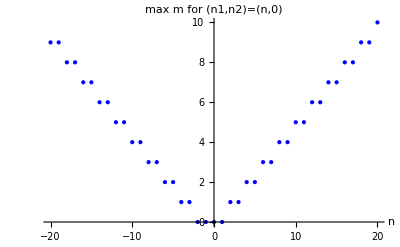

```mathematica
Mmax=50;ListPlot[Table[{n1,Max[FindTruncation[n1,0,Mmax][[1]]]},{n1,-20,20}],PlotStyle->{Blue,PointSize[Medium]},AxesLabel->{"n","max m for (n1,n2)=(n,0)"},PlotRange->All]
```

```mathematica
Do[
Print[FindTruncation[n1,0,20]]
,{n1,-10,10}];
```

#### h=1 -> JKRes

```mathematica
(* The integrand for h=1 *)
m=.;n1=.;n2=.;h=1;
ZSU2h1 = ZSU2
```

-1/2 ⅈ ((ⅈ Eta)/Theta1[1])^-n2 ((ⅈ Eta)/Theta1[1/f])^-n1 ((ⅈ Eta)/Theta1[f])^(1+n1+n2) ((ⅈ Eta)/Theta1[1/x^2])^(-2 m-n2) Theta1[1/x^2] ((ⅈ Eta)/Theta1[1/(f x^2)])^(-2 m-n1) ((ⅈ Eta)/Theta1[f/x^2])^(1-2 m+n1+n2) ((ⅈ Eta)/Theta1[x^2])^(2 m-n2) Theta1[x^2] ((ⅈ Eta)/Theta1[x^2/f])^(2 m-n1) ((ⅈ Eta)/Theta1[f x^2])^(1+2 m+n1+n2)

We see a divergence coming from the Theta1[1/h] term. Setting n2=0 we can avoid this temporarily.

```mathematica
n2=0;
ZSU2h1
```

-1/2 ⅈ ((ⅈ Eta)/Theta1[1/f])^-n1 ((ⅈ Eta)/Theta1[f])^(1+n1) ((ⅈ Eta)/Theta1[1/x^2])^(-2 m) Theta1[1/x^2] ((ⅈ Eta)/Theta1[1/(f x^2)])^(-2 m-n1) ((ⅈ Eta)/Theta1[f/x^2])^(1-2 m+n1) ((ⅈ Eta)/Theta1[x^2])^(2 m) Theta1[x^2] ((ⅈ Eta)/Theta1[x^2/f])^(2 m-n1) ((ⅈ Eta)/Theta1[f x^2])^(1+2 m+n1)

But now simplify the expression, and we get rid of the m dependence (this also works for n2!=0)

```mathematica
ZSU2h1Simple=Simplify[(ZSU2h1/.{Theta1[1/(f*(x_)^2)]->-Theta1[f*x^2],Theta1[1/f]->-Theta1[f],Theta1[1/(x_)^2]->-Theta1[x^2],Theta1[f/(x_)^2]->-Theta1[x^2/f]}),Assumptions->m∈Integers&&n1∈Integers&&n2∈Integers]
```

-((-1)^n1 Eta^3 Theta1[x^2]^2)/(2 Theta1[f] Theta1[x^2/f] Theta1[f x^2])

Which implies an infinite sum of a finite value. This is shady as all powers of x are now positive, think about the JKRes prescription which cares about the Q vectors: it seems like we can always shift all Q vectors to be positive and choose a negative eta, and we will always get 0. This doesn’t seem right. 
Let’s try taking the JKRes without the replacements above. For this to be possible let’s take n1=0 and thus need only m=0 NAIVELY.

```mathematica
n1=0;n2=0;
{Listm,singPts}=FindTruncation[n1,n2,Mmax];
singPts=singPts/.Subscript[v, 2]->0;
{Listm, singPts}
m=0;
ZSU2h1
```

{{0},{{v_1/2,1/2 (-τ+v_1),1/2 (-1+v_1),1/2 (-1-τ+v_1)}}}

-(Eta^3 Theta1[1/x^2] Theta1[x^2])/(2 Theta1[f] Theta1[f/x^2] Theta1[f x^2])

```mathematica
n1=0;
(* Choosing positive *)
Res=0;
Do[
Ztemp=Evaluate[((ZSU2h1/.{x->x*(-1)^a(√q)^b(√f)^-1})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res=Res+SimpleResidue[Ztemp,x];
,{a,{0,1}},{b,{0,1}}]
Res/.replacementRule
(* Choosing negative *)
Res=0;
Do[
Ztemp=Evaluate[((ZSU2h1/.{x->x*(-1)^a(√q)^b(√f)^1})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res=Res-SimpleResidue[Ztemp,x];
,{a,{0,1}},{b,{0,1}}]
Res/.replacementRule
```

-Theta1[1/f]/(2 π Theta1[f^2])

-Theta1[1/f]/(2 π Theta1[f^2])

We got an answer, but does the series actually truncate for other m? Let’s check, try taking the JKRes of:

```mathematica
n1=0;n2=0;m=1;
ZSU2h1
```

-(Eta^3 Theta1[1/x^2]^3 Theta1[1/(f x^2)]^2 Theta1[f/x^2])/(2 Theta1[f] Theta1[x^2] Theta1[x^2/f]^2 Theta1[f x^2]^3)

Contains higher order terms :( need to use ContourInt. m>0 -> smart choice is u<0. Lets check both u<0 choice and u>0 choice.

```mathematica
Nmax=1;
```

```mathematica
(* Choosing positive x *)

(*Theta1[f x^2]^3*)
Res=0;
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1 √q})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1 √q(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res1= Res+ContourInt[Ztemp//qForm//qExpand,x];

Res=0;
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)√q})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)√q(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res2= Res+ContourInt[Ztemp//qForm//qExpand,x];

Res=0;
Ztemp=Evaluate[((ZSU2h1/.{x->x})/.replacementRule)];
Ztemp=(1/2 ZSU2h1/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*√q})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*√q(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Res3 = Res;

Res1
Res2
Res3
Print["Final result is: ",Res1 + Res2 + Res3]
```

(ⅈ (f^2+q-f q-f^3 q+f^4 q))/(f^(3/2) (1+f))

-(ⅈ (f^2+q-f q-f^3 q+f^4 q))/(f^(3/2) (1+f))

0

Final result is: 0

```mathematica
(* Choosing negative x *)

Res=0;
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1 √q})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)^-1 √q(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res1= Res-ContourInt[Ztemp//qForm//qExpand,x];

Res=0;
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)√q})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(√f)√q(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res2= Res-ContourInt[Ztemp//qForm//qExpand,x];

Res=0;
Ztemp=Evaluate[((ZSU2h1/.{x->x})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*√q})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2h1/.{x->x*√q(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Res3 = Res;

Res1
Res2
Res3
Print["Final result is: ",Res1 + Res2 + Res3]
```

-(ⅈ (f^2+q-f q-f^3 q+f^4 q))/(f^(3/2) (1+f))

(ⅈ (f^2+q-f q-f^3 q+f^4 q))/(f^(3/2) (1+f))

0

Final result is: 0

We see that for m=1 we get 0 for both choices of charge. Might be good to check also for m=-1. 

Finally, let’s switch the order of operations.

#### JKRes -> h=1

```mathematica
n1=.;n2=.;m=.;h=.;f=.;
ZSU2
```

-1/2 ⅈ ((ⅈ Eta)/Theta1[1/f])^-n1 ((ⅈ Eta)/Theta1[1/h])^-n2 ((ⅈ Eta)/Theta1[f h])^(1+n1+n2) Theta1[1/x^2] ((ⅈ Eta)/Theta1[1/(f x^2)])^(-2 m-n1) ((ⅈ Eta)/Theta1[1/(h x^2)])^(-2 m-n2) ((ⅈ Eta)/Theta1[(f h)/x^2])^(1-2 m+n1+n2) Theta1[x^2] ((ⅈ Eta)/Theta1[x^2/f])^(2 m-n1) ((ⅈ Eta)/Theta1[x^2/h])^(2 m-n2) ((ⅈ Eta)/Theta1[f h x^2])^(1+2 m+n1+n2)

Let’s start immediately with n1=n2=0

```mathematica
n1=0;n2=0;
ZSU2
```

1/(2 Theta1[f h])Eta Theta1[1/x^2] ((ⅈ Eta)/Theta1[1/(f x^2)])^(-2 m) ((ⅈ Eta)/Theta1[1/(h x^2)])^(-2 m) ((ⅈ Eta)/Theta1[(f h)/x^2])^(1-2 m) Theta1[x^2] ((ⅈ Eta)/Theta1[x^2/f])^(2 m) ((ⅈ Eta)/Theta1[x^2/h])^(2 m) ((ⅈ Eta)/Theta1[f h x^2])^(1+2 m)

```mathematica
n1=0;n2=0;
{Listm,singPts}=FindTruncation[n1,n2,Mmax];
singPts=singPts;
{Listm, singPts}
```

{{0},{{1/2 (v_1+v_2),1/2 (-τ+v_1+v_2),1/2 (-1+v_1+v_2),1/2 (-1-τ+v_1+v_2)}}}

```mathematica
letterDict=<|Subscript[v, 1]->f,Subscript[v, 2]->h,u->x,τ->q|>;
singPtList=LetterExp[singPts[[1]]];
m=0;
Res=0;
ResQ=0;
Do[
Ztemp=Evaluate[((ZSU2/.x->x*singPtList[[i]])/.replacementRule)];
Res=Res-SimpleResidue[-1/2 Ztemp/.x->x^(-1/2),x];
,{i,1,Length[singPtList]}]
Res
```

-Theta1[1/(f h)]/(2 π Theta1[f^2 h^2])

We got the same result, good :) Let’s check m=1 is zero:

```mathematica
m=1;
ZSU2
```

-(Eta^3 Theta1[1/x^2] Theta1[1/(f x^2)]^2 Theta1[1/(h x^2)]^2 Theta1[(f h)/x^2] Theta1[x^2])/(2 Theta1[f h] Theta1[x^2/f]^2 Theta1[x^2/h]^2 Theta1[f h x^2]^3)

High order, need ContourInt. Note something weird - the positive u have the Theta1[f h x^2]^3 which is order 3, while negative u don’t have that.

```mathematica
(* choose positive *)
Nmax=0;

(*Theta1[x^2/f]^2*)
Res=0;
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)√q})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)√q(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res1= Res+ContourInt[Ztemp//qForm//qExpand,x];

(*Theta1[x^2/h]^2 *)
Res=0;
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)√q})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)√q(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res2= Res+ContourInt[Ztemp//qForm//qExpand,x];

(*Theta1[f h x^2]^3*)
Res=0;
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)^-1})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)^-1(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)^-1 √q})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res= Res+ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)^-1 √q(-1)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res3= Res+ContourInt[Ztemp//qForm//qExpand,x];
```

```mathematica
Res = (Res1 + Res2 + Res3)//Simplify
```

0

We see m=1 gives zero for u>0. This is actually the “wrong” choice, so awesome we got 0. For completeness let’s check the obvious case u<0.

```mathematica
(* choose negative *)
Nmax=0;

(*Theta1[1/x^2] Theta1[1/(f x^2)]^2 Theta1[1/(h x^2)]^2 Theta1[(f h)/x^2]*)
(* Theta1[1/(f x^2)]^2*)
Res=0;
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)^-1})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)^-1(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)^-1 √q})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f)^-1 √q(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res1= Res-ContourInt[Ztemp//qForm//qExpand,x];

(*Theta1[1/(h x^2)]^2 *)
Res=0;
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)^-1})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)^-1(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)^-1 √q})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√h)^-1 √q(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res2= Res-ContourInt[Ztemp//qForm//qExpand,x];

(*Theta1[(f h)/x^2]*)
Res=0;
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)√q})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(√f √h)√q(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res3= Res-ContourInt[Ztemp//qForm//qExpand,x];

(*Theta1[1/x^2]*)
Res=0;
Ztemp=(-1/2 ZSU2/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*√q})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res= Res-ContourInt[Ztemp//qForm//qExpand,x];
Ztemp=Evaluate[((ZSU2/.{x->x*√q(-1)})/.replacementRule)];
Ztemp=(-1/2 Ztemp/.x->x^(-1/2))/.replacementRule;
Res4= Res-ContourInt[Ztemp//qForm//qExpand,x];
```

```mathematica
Res=Res1+Res2+Res3+Res4
```

0

We saw that for both cases, m=1 gives 0.

#### Modular transformation

```mathematica
?Θ
```

```mathematica
Nmax=1;
Theta1[Exp[2*π*ⅈ*u/τ],Exp[-1/τ]]//Simplify
```

-ⅈ ⅇ^(-(7 (9+2 ⅈ π u))/τ) (ⅇ^(-1/τ))^(1/8) √(ⅇ^((2 ⅈ π u)/τ)) (-1+ⅇ^(1/τ))^6 (1+ⅇ^(1/τ))^3 (1+ⅇ^(2/τ)) (1-ⅇ^(1/τ)+ⅇ^(2/τ)) (1+ⅇ^(1/τ)+ⅇ^(2/τ))^2 (1+ⅇ^(1/τ)+ⅇ^(2/τ)+ⅇ^(3/τ)+ⅇ^(4/τ)) (ⅇ^(1/τ)-ⅇ^((2 ⅈ π u)/τ)) (ⅇ^(2/τ)-ⅇ^((2 ⅈ π u)/τ)) (ⅇ^(3/τ)-ⅇ^((2 ⅈ π u)/τ)) (ⅇ^(4/τ)-ⅇ^((2 ⅈ π u)/τ)) (ⅇ^(5/τ)-ⅇ^((2 ⅈ π u)/τ)) (ⅇ^(6/τ)-ⅇ^((2 ⅈ π u)/τ)) (-1+ⅇ^((2 ⅈ π u)/τ)) (-1+ⅇ^((1+2 ⅈ π u)/τ)) (-1+ⅇ^((2+2 ⅈ π u)/τ)) (-1+ⅇ^((3+2 ⅈ π u)/τ)) (-1+ⅇ^((4+2 ⅈ π u)/τ)) (-1+ⅇ^((5+2 ⅈ π u)/τ)) (-1+ⅇ^((6+2 ⅈ π u)/τ))

```mathematica
-ⅈ*√(-ⅈ*τ)*ⅇ^(π*ⅈ*u^2/τ)*Theta1[Exp[2*π*ⅈ*u],Exp[τ]]//Simplify
```

-ⅇ^((ⅈ π u (u-14 τ))/τ) √(ⅇ^(2 ⅈ π u)) (ⅇ^τ)^(1/8) (-1+ⅇ^(2 ⅈ π u)) (ⅇ^(2 ⅈ π u)-ⅇ^τ) (-1+ⅇ^τ)^6 (1+ⅇ^τ)^3 (ⅇ^(2 ⅈ π u)-ⅇ^(2 τ)) (1+ⅇ^(2 τ)) (1-ⅇ^τ+ⅇ^(2 τ)) (1+ⅇ^τ+ⅇ^(2 τ))^2 (ⅇ^(2 ⅈ π u)-ⅇ^(3 τ)) (ⅇ^(2 ⅈ π u)-ⅇ^(4 τ)) (1+ⅇ^τ+ⅇ^(2 τ)+ⅇ^(3 τ)+ⅇ^(4 τ)) (ⅇ^(2 ⅈ π u)-ⅇ^(5 τ)) (ⅇ^(2 ⅈ π u)-ⅇ^(6 τ)) (-1+ⅇ^(2 ⅈ π u+τ)) (-1+ⅇ^(2 ⅈ π u+2 τ)) (-1+ⅇ^(2 ⅈ π u+3 τ)) (-1+ⅇ^(2 ⅈ π u+4 τ)) (-1+ⅇ^(2 ⅈ π u+5 τ)) (-1+ⅇ^(2 ⅈ π u+6 τ)) √(-ⅈ τ)

#### Old code

```mathematica
(* Choosing positive *)
Nmax=0;
Res=0;
Do[
Ztemp=Evaluate[((ZSU2h1/.{x->x*(-1)^a(√q)^b(√f)^-1})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res=Res+ContourInt[Ztemp//qForm//qExpand,x];
,{a,0,1},{b,0,1}]
Res/.replacementRule
```

Series::fas: Warning: one or more assumptions evaluated to False.

$Assumptions::fas: Warning: one or more assumptions evaluated to False.

(ⅈ √f)/(2 (1+f))+(ⅈ √(1/f) √(f^2))/(2 (1+f))

```mathematica
n1=0;n2=0;m=0;Mmax=50;
{Listm,singPts}=FindTruncation[n1,n2,Mmax];
```

Setting h to 1:

```mathematica
ZSU2/.h->1
```

-(Eta^3 Theta1[1/x^2] Theta1[x^2])/(2 Theta1[f] Theta1[f/x^2] Theta1[f x^2])

```mathematica
ZSU2h=-1/(2 Theta1[f])Eta   ((ⅈ Eta)/Theta1[x^2/f])(Theta1[x^2])^2((ⅈ Eta)/Theta1[f x^2])
```

(Eta^3 Theta1[x^2]^2)/(2 Theta1[f] Theta1[x^2/f] Theta1[f x^2])

```mathematica
Res=0;
Do[
Ztemp=Evaluate[((ZSU2h/.{x->x*(-1)^a(√q)^b(√f)})/.replacementRule)];
Ztemp=(1/2 Ztemp/.x->x^(1/2))/.replacementRule;
Res=Res+SimpleResidue[Ztemp,x];
,{a,{0,1}},{b,{0,1}}]
Res/.replacementRule
```

Theta1[f]/(2 π Theta1[f^2])

```mathematica
letterDict=<|Subscript[v, 1]->f,Subscript[v, 2]->h,u->x,τ->q|>;
singPtList=LetterExp[singPts[[1]]]
Nmax=0;
Res=0;
ResQ=0;
Do[
Ztemp=Evaluate[((ZSU2/.x->x*singPtList[[i]])/.replacementRule)];
Res=Res+SimpleResidue[-1/2 Ztemp/.x->x^(-1/2),x];
ResQ=ResQ+1/(2π*ⅈ)ContourInt[Ztemp//qForm,x];
,{i,1,Length[singPtList]}]
```

{√f √h,(√f √h)/(√q),-√f √h,-(√f √h)/(√q)}

```mathematica
Res
```

(Theta1[1]^2 Theta1[1/(f h^2)]^2 Theta1[1/(f^2 h)]^2 Theta1[1/(f h)])/(2 π Theta1[f]^2 Theta1[h]^2 Theta1[f^2 h^2]^3)

```mathematica
Res/.h->1
```

(Theta1[1/f^2]^2 Theta1[1/f]^3)/(2 π Theta1[f]^2 Theta1[f^2]^3)

```mathematica
(ResQ//qExpand//Simplify//qExpand)/.h->1
```

((-1+f) √f (1-2 f^2+f^4))/(2 (-1+f^2)^3 π)

```mathematica
Res//qForm//qExpand//Simplify//qExpand
ResQ//qExpand//Simplify//qExpand
```

Consistency check: check the JK residue for m=1 and choosing positive poles:

```mathematica
ZSU2
```

-((Eta^3 Theta1[1/x^2] Theta1[1/(f x^2)]^2 Theta1[1/(h x^2)]^2 Theta1[(f h)/x^2] Theta1[x^2])/(2 Theta1[f h] Theta1[x^2/f]^2 Theta1[x^2/h]^2 Theta1[f h x^2]^3))

```mathematica
singPtList={√f ,-√f,√f(√q)^-1,-√f(√q)^-1,√h ,-√h,√h(√q)^-1,-√h(√q)^-1,(√(f*h))^-1 ,-(√(f*h))^-1,(√(f*h))^-1(√q)^-1,-(√(f*h))^-1(√q)^-1}
```

{√f,-√f,(√f)/(√q),-(√f)/(√q),√h,-√h,(√h)/(√q),-(√h)/(√q),1/(√(f h)),-1/(√(f h)),1/(√(f h) √q),-1/(√(f h) √q)}

```mathematica
ZSU2
```

-((Eta^3 Theta1[1/x^2] Theta1[1/(f x^2)]^2 Theta1[1/(h x^2)]^2 Theta1[(f h)/x^2] Theta1[x^2])/(2 Theta1[f h] Theta1[x^2/f]^2 Theta1[x^2/h]^2 Theta1[f h x^2]^3))

```mathematica
SimpleResidue[1/Theta1[z*μ]/.z->z*μ^-1,z]
```

1/(2 Eta^3 π)

```mathematica
m=1;
Ztest=(1/Theta1[z*μ])^m(1/Theta1[z^-1*μ])^-m
```

Theta1[μ/z]/Theta1[z μ]

```mathematica
SimpleResidue[Ztest/.z->z*μ^-1,z]
```

Theta1[μ^2]/(2 Eta^3 π)

```mathematica
Nmax=0;
Res={};
Do[
Print["i=",i];
Ztemp=Evaluate[((ZSU2/.x->x*singPtList[[i]])/.replacementRule)];
Ztemp=1/2 Ztemp/.x->x^(1/2);
Print[Ztemp//qForm];
ResTemp=1/(2π*ⅈ)ContourInt[Ztemp//qForm,x]//qExpand//Simplify//qExpand;
Print[ResTemp];
AppendTo[Res,ResTemp];
,{i,1,Length[singPtList]}]
```

i=1

(ⅈ (1-1/(f x)) √(1/(f x)) √(h/x) √(f x) (-1+f x) (-1+f^2 x)^2 (1-x/h) (-1+f h x)^2)/(4 f^4 (1-1/(f h)) √(f h) (1-1/(f^2 h x))^3 (1-h/(f x))^2 (-1+x)^2 x^2 (f^2 h x)^(3/2))

-1/(8 (f-h)^3 (-1+f^2 h)^4 π)(-1+f)^3 √f (1+f) h^(3/2) (h^2+f^6 h^2+f^2 (2-6 h+9 h^2-6 h^3)+f (2-5 h+h^3)+f^4 h (-6+9 h-6 h^2+2 h^3)+2 f^3 (1-4 h+8 h^2-4 h^3+h^4)+f^5 (h-5 h^3+2 h^4))

i=2

(ⅈ (1-1/(f x)) √(1/(f x)) √(h/x) √(f x) (-1+f x) (-1+f^2 x)^2 (1-x/h) (-1+f h x)^2)/(4 f^4 (1-1/(f h)) √(f h) (1-1/(f^2 h x))^3 (1-h/(f x))^2 (-1+x)^2 x^2 (f^2 h x)^(3/2))

-1/(8 (f-h)^3 (-1+f^2 h)^4 π)(-1+f)^3 √f (1+f) h^(3/2) (h^2+f^6 h^2+f^2 (2-6 h+9 h^2-6 h^3)+f (2-5 h+h^3)+f^4 h (-6+9 h-6 h^2+2 h^3)+2 f^3 (1-4 h+8 h^2-4 h^3+h^4)+f^5 (h-5 h^3+2 h^4))

i=3

(ⅈ (1-1/(f x)) √(1/(f x)) √(h/x) √(f x) (-1+f x) (-1+f^2 x)^2 (1-x/h) (-1+f h x)^2)/(4 f^4 (1-1/(f h)) √(f h) (1-1/(f^2 h x))^3 (1-h/(f x))^2 (-1+x)^2 x^2 (f^2 h x)^(3/2))

-1/(8 (f-h)^3 (-1+f^2 h)^4 π)(-1+f)^3 √f (1+f) h^(3/2) (h^2+f^6 h^2+f^2 (2-6 h+9 h^2-6 h^3)+f (2-5 h+h^3)+f^4 h (-6+9 h-6 h^2+2 h^3)+2 f^3 (1-4 h+8 h^2-4 h^3+h^4)+f^5 (h-5 h^3+2 h^4))

i=4

(ⅈ (1-1/(f x)) √(1/(f x)) √(h/x) √(f x) (-1+f x) (-1+f^2 x)^2 (1-x/h) (-1+f h x)^2)/(4 f^4 (1-1/(f h)) √(f h) (1-1/(f^2 h x))^3 (1-h/(f x))^2 (-1+x)^2 x^2 (f^2 h x)^(3/2))

-1/(8 (f-h)^3 (-1+f^2 h)^4 π)(-1+f)^3 √f (1+f) h^(3/2) (h^2+f^6 h^2+f^2 (2-6 h+9 h^2-6 h^3)+f (2-5 h+h^3)+f^4 h (-6+9 h-6 h^2+2 h^3)+2 f^3 (1-4 h+8 h^2-4 h^3+h^4)+f^5 (h-5 h^3+2 h^4))

i=5

(ⅈ (1-1/(h x)) √(f/x) √(1/(h x)) √(h x) (1-x/f) (-1+h x) (-1+f h x)^2 (-1+h^2 x)^2)/(4 (1-1/(f h)) h^4 √(f h) (1-1/(f h^2 x))^3 (1-f/(h x))^2 (-1+x)^2 x^2 (f h^2 x)^(3/2))

1/(8 (f-h)^3 (-1+f h^2)^4 π)f^(3/2) (-1+h)^3 √h (1+h) (2 h (1+h+h^2)+2 f^4 h^3 (1+h+h^2)+f h (-5-6 h-8 h^2-6 h^3+h^4)-f^3 h (-1+6 h+8 h^2+6 h^3+5 h^4)+f^2 (1+9 h^2+16 h^3+9 h^4+h^6))

i=6

(ⅈ (1-1/(h x)) √(f/x) √(1/(h x)) √(h x) (1-x/f) (-1+h x) (-1+f h x)^2 (-1+h^2 x)^2)/(4 (1-1/(f h)) h^4 √(f h) (1-1/(f h^2 x))^3 (1-f/(h x))^2 (-1+x)^2 x^2 (f h^2 x)^(3/2))

1/(8 (f-h)^3 (-1+f h^2)^4 π)f^(3/2) (-1+h)^3 √h (1+h) (2 h (1+h+h^2)+2 f^4 h^3 (1+h+h^2)+f h (-5-6 h-8 h^2-6 h^3+h^4)-f^3 h (-1+6 h+8 h^2+6 h^3+5 h^4)+f^2 (1+9 h^2+16 h^3+9 h^4+h^6))

i=7

(ⅈ (1-1/(h x)) √(f/x) √(1/(h x)) √(h x) (1-x/f) (-1+h x) (-1+f h x)^2 (-1+h^2 x)^2)/(4 (1-1/(f h)) h^4 √(f h) (1-1/(f h^2 x))^3 (1-f/(h x))^2 (-1+x)^2 x^2 (f h^2 x)^(3/2))

1/(8 (f-h)^3 (-1+f h^2)^4 π)f^(3/2) (-1+h)^3 √h (1+h) (2 h (1+h+h^2)+2 f^4 h^3 (1+h+h^2)+f h (-5-6 h-8 h^2-6 h^3+h^4)-f^3 h (-1+6 h+8 h^2+6 h^3+5 h^4)+f^2 (1+9 h^2+16 h^3+9 h^4+h^6))

i=8

(ⅈ (1-1/(h x)) √(f/x) √(1/(h x)) √(h x) (1-x/f) (-1+h x) (-1+f h x)^2 (-1+h^2 x)^2)/(4 (1-1/(f h)) h^4 √(f h) (1-1/(f h^2 x))^3 (1-f/(h x))^2 (-1+x)^2 x^2 (f h^2 x)^(3/2))

1/(8 (f-h)^3 (-1+f h^2)^4 π)f^(3/2) (-1+h)^3 √h (1+h) (2 h (1+h+h^2)+2 f^4 h^3 (1+h+h^2)+f h (-5-6 h-8 h^2-6 h^3+h^4)-f^3 h (-1+6 h+8 h^2+6 h^3+5 h^4)+f^2 (1+9 h^2+16 h^3+9 h^4+h^6))

i=9

-(ⅈ f^4 h^4 (1-(f h)/x) √((f h)/x) √((f^2 h^2)/x) √(x/(f h)) (1-x/f)^2 (1-x/(f^2 h^2)) (1-x/h)^2 (1-x/(f h)))/(4 (1-1/(f h)) √(f h) (1-(f^2 h)/x)^2 (1-(f h^2)/x)^2 (-1+x)^3 x^(5/2))

1/(8 (-1+f^2 h)^4 (-1+f h^2)^4 π)√(f h) (1+f^11 h^11+f^10 h^7 (2-2 h-6 h^2+h^3)+f h (1-6 h-2 h^2+2 h^3)+f^9 h^5 (1-8 h+10 h^2+14 h^3-4 h^4-6 h^5)+f^2 h (-6-4 h+14 h^2+10 h^3-8 h^4+h^5)+f^8 h^4 (1-6 h+10 h^2-28 h^3+16 h^4+14 h^5-2 h^6)+f^3 h (-2+14 h+16 h^2-28 h^3+10 h^4-6 h^5+h^6)+f^4 h (2+10 h-28 h^2+21 h^3-58 h^4+38 h^5-8 h^6+h^7)+f^5 h^2 (-8+10 h-58 h^2+105 h^3-68 h^4+38 h^5-6 h^6+h^7)+f^7 h^3 (1-8 h+38 h^2-58 h^3+21 h^4-28 h^5+10 h^6+2 h^7)+f^6 (h^2-6 h^3+38 h^4-68 h^5+105 h^6-58 h^7+10 h^8-8 h^9))

i=10

-(ⅈ f^4 h^4 (1-(f h)/x) √((f h)/x) √((f^2 h^2)/x) √(x/(f h)) (1-x/f)^2 (1-x/(f^2 h^2)) (1-x/h)^2 (1-x/(f h)))/(4 (1-1/(f h)) √(f h) (1-(f^2 h)/x)^2 (1-(f h^2)/x)^2 (-1+x)^3 x^(5/2))

1/(8 (-1+f^2 h)^4 (-1+f h^2)^4 π)√(f h) (1+f^11 h^11+f^10 h^7 (2-2 h-6 h^2+h^3)+f h (1-6 h-2 h^2+2 h^3)+f^9 h^5 (1-8 h+10 h^2+14 h^3-4 h^4-6 h^5)+f^2 h (-6-4 h+14 h^2+10 h^3-8 h^4+h^5)+f^8 h^4 (1-6 h+10 h^2-28 h^3+16 h^4+14 h^5-2 h^6)+f^3 h (-2+14 h+16 h^2-28 h^3+10 h^4-6 h^5+h^6)+f^4 h (2+10 h-28 h^2+21 h^3-58 h^4+38 h^5-8 h^6+h^7)+f^5 h^2 (-8+10 h-58 h^2+105 h^3-68 h^4+38 h^5-6 h^6+h^7)+f^7 h^3 (1-8 h+38 h^2-58 h^3+21 h^4-28 h^5+10 h^6+2 h^7)+f^6 (h^2-6 h^3+38 h^4-68 h^5+105 h^6-58 h^7+10 h^8-8 h^9))

i=11

-(ⅈ f^4 h^4 (1-(f h)/x) √((f h)/x) √((f^2 h^2)/x) √(x/(f h)) (1-x/f)^2 (1-x/(f^2 h^2)) (1-x/h)^2 (1-x/(f h)))/(4 (1-1/(f h)) √(f h) (1-(f^2 h)/x)^2 (1-(f h^2)/x)^2 (-1+x)^3 x^(5/2))

1/(8 (-1+f^2 h)^4 (-1+f h^2)^4 π)√(f h) (1+f^11 h^11+f^10 h^7 (2-2 h-6 h^2+h^3)+f h (1-6 h-2 h^2+2 h^3)+f^9 h^5 (1-8 h+10 h^2+14 h^3-4 h^4-6 h^5)+f^2 h (-6-4 h+14 h^2+10 h^3-8 h^4+h^5)+f^8 h^4 (1-6 h+10 h^2-28 h^3+16 h^4+14 h^5-2 h^6)+f^3 h (-2+14 h+16 h^2-28 h^3+10 h^4-6 h^5+h^6)+f^4 h (2+10 h-28 h^2+21 h^3-58 h^4+38 h^5-8 h^6+h^7)+f^5 h^2 (-8+10 h-58 h^2+105 h^3-68 h^4+38 h^5-6 h^6+h^7)+f^7 h^3 (1-8 h+38 h^2-58 h^3+21 h^4-28 h^5+10 h^6+2 h^7)+f^6 (h^2-6 h^3+38 h^4-68 h^5+105 h^6-58 h^7+10 h^8-8 h^9))

i=12

-(ⅈ f^4 h^4 (1-(f h)/x) √((f h)/x) √((f^2 h^2)/x) √(x/(f h)) (1-x/f)^2 (1-x/(f^2 h^2)) (1-x/h)^2 (1-x/(f h)))/(4 (1-1/(f h)) √(f h) (1-(f^2 h)/x)^2 (1-(f h^2)/x)^2 (-1+x)^3 x^(5/2))

1/(8 (-1+f^2 h)^4 (-1+f h^2)^4 π)√(f h) (1+f^11 h^11+f^10 h^7 (2-2 h-6 h^2+h^3)+f h (1-6 h-2 h^2+2 h^3)+f^9 h^5 (1-8 h+10 h^2+14 h^3-4 h^4-6 h^5)+f^2 h (-6-4 h+14 h^2+10 h^3-8 h^4+h^5)+f^8 h^4 (1-6 h+10 h^2-28 h^3+16 h^4+14 h^5-2 h^6)+f^3 h (-2+14 h+16 h^2-28 h^3+10 h^4-6 h^5+h^6)+f^4 h (2+10 h-28 h^2+21 h^3-58 h^4+38 h^5-8 h^6+h^7)+f^5 h^2 (-8+10 h-58 h^2+105 h^3-68 h^4+38 h^5-6 h^6+h^7)+f^7 h^3 (1-8 h+38 h^2-58 h^3+21 h^4-28 h^5+10 h^6+2 h^7)+f^6 (h^2-6 h^3+38 h^4-68 h^5+105 h^6-58 h^7+10 h^8-8 h^9))

```mathematica
ResultList=4*Res[[{1,5,9}]]
```

{-(((-1+f)^3 √f (1+f) h^(3/2) (h^2+f^6 h^2+f^2 (2-6 h+9 h^2-6 h^3)+f (2-5 h+h^3)+f^4 h (-6+9 h-6 h^2+2 h^3)+2 f^3 (1-4 h+8 h^2-4 h^3+h^4)+f^5 (h-5 h^3+2 h^4)))/(2 (f-h)^3 (-1+f^2 h)^4 π)),(f^(3/2) (-1+h)^3 √h (1+h) (2 h (1+h+h^2)+2 f^4 h^3 (1+h+h^2)+f h (-5-6 h-8 h^2-6 h^3+h^4)-f^3 h (-1+6 h+8 h^2+6 h^3+5 h^4)+f^2 (1+9 h^2+16 h^3+9 h^4+h^6)))/(2 (f-h)^3 (-1+f h^2)^4 π),1/(2 (-1+f^2 h)^4 (-1+f h^2)^4 π)√(f h) (1+f^11 h^11+f^10 h^7 (2-2 h-6 h^2+h^3)+f h (1-6 h-2 h^2+2 h^3)+f^9 h^5 (1-8 h+10 h^2+14 h^3-4 h^4-6 h^5)+f^2 h (-6-4 h+14 h^2+10 h^3-8 h^4+h^5)+f^8 h^4 (1-6 h+10 h^2-28 h^3+16 h^4+14 h^5-2 h^6)+f^3 h (-2+14 h+16 h^2-28 h^3+10 h^4-6 h^5+h^6)+f^4 h (2+10 h-28 h^2+21 h^3-58 h^4+38 h^5-8 h^6+h^7)+f^5 h^2 (-8+10 h-58 h^2+105 h^3-68 h^4+38 h^5-6 h^6+h^7)+f^7 h^3 (1-8 h+38 h^2-58 h^3+21 h^4-28 h^5+10 h^6+2 h^7)+f^6 (h^2-6 h^3+38 h^4-68 h^5+105 h^6-58 h^7+10 h^8-8 h^9))}

```mathematica
ResultList[[1]]//Simplify
```

-(((-1+f)^3 √f (1+f) h^(3/2) (h^2+f^6 h^2+f^2 (2-6 h+9 h^2-6 h^3)+f (2-5 h+h^3)+f^4 h (-6+9 h-6 h^2+2 h^3)+2 f^3 (1-4 h+8 h^2-4 h^3+h^4)+f^5 (h-5 h^3+2 h^4)))/(2 (f-h)^3 (-1+f^2 h)^4 π))

```mathematica
ResultList[[1]]+ResultList[[2]]-ResultList[[3]]//Simplify
```

-1/((-1+f^2 h)^4 (-1+f h^2)^4 π)√(f h) (1+f^11 h^11+f^10 h^7 (2-2 h-6 h^2+h^3)+f h (1-6 h-2 h^2+2 h^3)+f^9 h^5 (1-8 h+10 h^2+14 h^3-4 h^4-6 h^5)+f^2 h (-6-4 h+14 h^2+10 h^3-8 h^4+h^5)+f^8 h^4 (1-6 h+10 h^2-28 h^3+16 h^4+14 h^5-2 h^6)+f^3 h (-2+14 h+16 h^2-28 h^3+10 h^4-6 h^5+h^6)+f^4 h (2+10 h-28 h^2+21 h^3-58 h^4+38 h^5-8 h^6+h^7)+f^5 h^2 (-8+10 h-58 h^2+105 h^3-68 h^4+38 h^5-6 h^6+h^7)+f^7 h^3 (1-8 h+38 h^2-58 h^3+21 h^4-28 h^5+10 h^6+2 h^7)+f^6 (h^2-6 h^3+38 h^4-68 h^5+105 h^6-58 h^7+10 h^8-8 h^9))

### General case

#### n1 = 0; n2 = 0;

```mathematica
n1=0;n2=0;m=0;
ZSU2=ZSU2PartitionFunction[n1,n2,m]
```

-(Eta^3 Theta1[1/x^2] Theta1[x^2])/(2 Theta1[f h] Theta1[(f h)/x^2] Theta1[f h x^2])

```mathematica
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
```

```mathematica
Res=0;
Ztointegrate=0;
Do[
m=mList[[i]];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
Res=Res-sign*SimpleResidue[Ztemp,x];
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Res=Res/.Theta1[1/(f*h)]->-Theta1[f*h]
```

Theta1[f h]/(2 π Theta1[f^2 h^2])

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[(f h)/x] Theta1[x/(f h)])/(Theta1[f h] Theta1[(f^2 h^2)/x] Theta1[x])

```mathematica
letterDict
```

<|v_1→f,v_2→h,u→x,τ→q|>

```mathematica
LetterLog[x]
```

u

```mathematica
Nmax=5;
Zint=Residue[Ztointegrate/.{Theta1[arg_]:>Theta1Modular[LetterLog[arg],τ]},u];
ZintQ=Zint//qExpand;
```

```mathematica
ⅇ^(-3π*ⅈ/τ*(u+v)^2)Theta1Modular[u+v,τ]/Theta1Modular[2u+2v,τ]
Theta1Modular[u/τ+v/τ,-1/τ]/Theta1Modular[(2u)/τ+(2v)/τ,-1/τ]
```

0.00811063+0.306851 ⅈ

0.00811063+0.306851 ⅈ

```mathematica
τ=RandomComplex[];
Subscript[v, 1]=RandomComplex[];
Subscript[v, 2]=RandomComplex[];
ⅇ^(-3π*ⅈ/τ*(Subscript[v, 1]+Subscript[v, 2])^2)*ZintQ
ZintQ/.{f->ⅇ^(2*π*ⅈ*u/τ),h->ⅇ^(2*π*ⅈ*v/τ),q->ⅇ^(2*π*ⅈ*(-1/τ))}
```

6.74954×10^16+7.22754×10^16 ⅈ

-0.0168214-0.000607382 ⅈ

```mathematica
τ=.;
u=.;
v=.;
```

#### n1 = 0; n2 = 1;

```mathematica
n1=0;n2=1;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{0}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[1/h] Theta1[f/x] Theta1[(f h)/x] Theta1[x/(f h^2)] Theta1[x/(f h)])/(Theta1[f h]^2 Theta1[(f^2 h^2)/x]^2 Theta1[x]^2)

Final result:

```mathematica
Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

(Eta^3 Theta1[1/h] Theta1[f/x] Theta1[x/(f h^2)] Theta1[x/(f h)]^2)/(Theta1[f h]^2 Theta1[(f^2 h^2)/x]^2 Theta1[x]^2)

#### n1 = 0; n2 = 2;

```mathematica
n1=0;n2=2;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{-1,0,1}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[1/h]^2 Theta1[f/x]^2 Theta1[(f h)/x] Theta1[x/(f h^2)]^2 Theta1[x/(f h)])/(Theta1[f h]^3 Theta1[(f^2 h^2)/x]^3 Theta1[x]^3)-(2 Eta^3 Theta1[1/h]^2 Theta1[(f h)/x] Theta1[x/(f h^2)]^4 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)])/(Theta1[f h]^3 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^5 Theta1[x])

Final result:

```mathematica
Ztointegrate=Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

(Eta^3 Theta1[1/h]^2 Theta1[f/x]^2 Theta1[x/(f h^2)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^3 Theta1[(f^2 h^2)/x]^3 Theta1[x]^3)+(2 Eta^3 Theta1[1/h]^2 Theta1[x/(f h^2)]^4 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^3 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^5 Theta1[x])

```mathematica
func=Ztointegrate[[2]]
```

(2 Eta^3 Theta1[1/h]^2 Theta1[x/(f h^2)]^4 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^3 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^5 Theta1[x])

```mathematica
Z4=(Eta^3 Theta1[1/h]^4 Theta1[f/x]^4 Theta1[x/(f h^2)]^4 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[(f^2 h^2)/x]^5 Theta1[x]^5)+(2 Eta^3 Theta1[1/h]^4 Theta1[f/x]^2 Theta1[x/(f h^2)]^6 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^7 Theta1[x]^3)+(2 Eta^3 Theta1[1/h]^4 Theta1[x/(f h^2)]^8 Theta1[x/(f^2 h)]^4 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[h/x]^4 Theta1[(f^2 h^2)/x]^9 Theta1[x]);
```

```mathematica
temp//Simplify
```

-3 (3 v_1^2+6 v_1 v_2+v_2^2)

```mathematica
ModularTransformationFactor
```

#### n1 = 0; n2 = 3;

```mathematica
n1=0;n2=3;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{-1,0,1}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[1/h]^3 Theta1[f/x]^3 Theta1[(f h)/x] Theta1[x/(f h^2)]^3 Theta1[x/(f h)])/(Theta1[f h]^4 Theta1[(f^2 h^2)/x]^4 Theta1[x]^4)-(2 Eta^3 Theta1[1/h]^3 Theta1[f/x] Theta1[(f h)/x] Theta1[x/(f h^2)]^5 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)])/(Theta1[f h]^4 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^6 Theta1[x]^2)

Final result:

```mathematica
Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

(Eta^3 Theta1[1/h]^3 Theta1[f/x]^3 Theta1[x/(f h^2)]^3 Theta1[x/(f h)]^2)/(Theta1[f h]^4 Theta1[(f^2 h^2)/x]^4 Theta1[x]^4)+(2 Eta^3 Theta1[1/h]^3 Theta1[f/x] Theta1[x/(f h^2)]^5 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^4 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^6 Theta1[x]^2)

#### n1 = 0; n2 = 4;

```mathematica
n1=0;n2=4;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{-2,-1,0,1,2}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[1/h]^4 Theta1[f/x]^4 Theta1[(f h)/x] Theta1[x/(f h^2)]^4 Theta1[x/(f h)])/(Theta1[f h]^5 Theta1[(f^2 h^2)/x]^5 Theta1[x]^5)-(2 Eta^3 Theta1[1/h]^4 Theta1[f/x]^2 Theta1[(f h)/x] Theta1[x/(f h^2)]^6 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)])/(Theta1[f h]^5 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^7 Theta1[x]^3)-(2 Eta^3 Theta1[1/h]^4 Theta1[(f h)/x] Theta1[x/(f h^2)]^8 Theta1[x/(f^2 h)]^4 Theta1[x/(f h)])/(Theta1[f h]^5 Theta1[h/x]^4 Theta1[(f^2 h^2)/x]^9 Theta1[x])

Final result:

```mathematica
Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

(Eta^3 Theta1[1/h]^4 Theta1[f/x]^4 Theta1[x/(f h^2)]^4 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[(f^2 h^2)/x]^5 Theta1[x]^5)+(2 Eta^3 Theta1[1/h]^4 Theta1[f/x]^2 Theta1[x/(f h^2)]^6 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^7 Theta1[x]^3)+(2 Eta^3 Theta1[1/h]^4 Theta1[x/(f h^2)]^8 Theta1[x/(f^2 h)]^4 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[h/x]^4 Theta1[(f^2 h^2)/x]^9 Theta1[x])

#### n1 = 0; n2 = 5;

```mathematica
n1=0;n2=5;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{-2,-1,0,1,2}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[1/h]^5 Theta1[f/x]^5 Theta1[(f h)/x] Theta1[x/(f h^2)]^5 Theta1[x/(f h)])/(Theta1[f h]^6 Theta1[(f^2 h^2)/x]^6 Theta1[x]^6)-(2 Eta^3 Theta1[1/h]^5 Theta1[f/x]^3 Theta1[(f h)/x] Theta1[x/(f h^2)]^7 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)])/(Theta1[f h]^6 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^8 Theta1[x]^4)-(2 Eta^3 Theta1[1/h]^5 Theta1[f/x] Theta1[(f h)/x] Theta1[x/(f h^2)]^9 Theta1[x/(f^2 h)]^4 Theta1[x/(f h)])/(Theta1[f h]^6 Theta1[h/x]^4 Theta1[(f^2 h^2)/x]^10 Theta1[x]^2)

Final result:

```mathematica
Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

(Eta^3 Theta1[1/h]^5 Theta1[f/x]^5 Theta1[x/(f h^2)]^5 Theta1[x/(f h)]^2)/(Theta1[f h]^6 Theta1[(f^2 h^2)/x]^6 Theta1[x]^6)+(2 Eta^3 Theta1[1/h]^5 Theta1[f/x]^3 Theta1[x/(f h^2)]^7 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^6 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^8 Theta1[x]^4)+(2 Eta^3 Theta1[1/h]^5 Theta1[f/x] Theta1[x/(f h^2)]^9 Theta1[x/(f^2 h)]^4 Theta1[x/(f h)]^2)/(Theta1[f h]^6 Theta1[h/x]^4 Theta1[(f^2 h^2)/x]^10 Theta1[x]^2)

#### n1 = 0; n2 = -1;

```mathematica
n1=0;n2=-1;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{0}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[1/(h x)] Theta1[h x])/(Theta1[1/h] Theta1[1/(h^2 x)] Theta1[x])

Final result:

```mathematica
Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

-(Eta^3 Theta1[1/(h x)] Theta1[h x])/(Theta1[1/h] Theta1[1/(h^2 x)] Theta1[x])

#### n1 = n2 = -1;

```mathematica
n=-1;n1=n;n2=n;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{0}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-((Eta^3 Theta1[f h] Theta1[1/(f x)] Theta1[h/x] Theta1[f x] Theta1[f^2 h x])/(Theta1[1/f] Theta1[1/h] Theta1[1/(f^2 x)] Theta1[1/(f h x)] Theta1[x] Theta1[(f x)/h]))-(Eta^3 Theta1[f h] Theta1[f/x] Theta1[1/(h x)] Theta1[h x] Theta1[f h^2 x])/(Theta1[1/f] Theta1[1/h] Theta1[1/(h^2 x)] Theta1[1/(f h x)] Theta1[x] Theta1[(h x)/f])

Final result:

```mathematica
Ztointegrate=Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

-((Eta^3 Theta1[f h] Theta1[1/(f x)] Theta1[h/x] Theta1[f x] Theta1[f^2 h x])/(Theta1[1/f] Theta1[1/h] Theta1[1/(f^2 x)] Theta1[1/(f h x)] Theta1[x] Theta1[(f x)/h]))-(Eta^3 Theta1[f h] Theta1[f/x] Theta1[1/(h x)] Theta1[h x] Theta1[f h^2 x])/(Theta1[1/f] Theta1[1/h] Theta1[1/(h^2 x)] Theta1[1/(f h x)] Theta1[x] Theta1[(h x)/f])

```mathematica
ModularTransformation[Ztointegrate]
```

{{1,0},{1,0}}

```mathematica
Zresult=SimpleResidue[Ztointegrate,x]//Simplify
```

(Theta1[f] Theta1[h] Theta1[f h] (-Theta1[f^2 h]/(Theta1[1/f^2] Theta1[1/h] Theta1[f/h])-Theta1[f h^2]/(Theta1[1/f] Theta1[1/h^2] Theta1[h/f])))/(2 π Theta1[1/(f h)])

```mathematica
Zresult/.{ Theta1[1/(f h)]-> -Theta1[f h],Theta1[h/f]->-Theta1[f/h]}//Simplify
```

-(Theta1[f] Theta1[h] (-Theta1[f^2 h]/(Theta1[1/f^2] Theta1[1/h])+Theta1[f h^2]/(Theta1[1/f] Theta1[1/h^2])))/(2 π Theta1[f/h])

#### n1 = n2 = -2;

```mathematica
n=2;n1=n;n2=n;
{mList,singPoints}=FindTruncation[n1,n2,Mmax];
mList
```

{-2,-1,0,1,2}

```mathematica
Ztointegrate=0;
Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}]
```

```mathematica
Ztointegrate
```

-(Eta^3 Theta1[1/f]^2 Theta1[1/h]^2 Theta1[f/x]^2 Theta1[h/x]^2 Theta1[(f h)/x] Theta1[x/(f h^2)]^2 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)])/(Theta1[f h]^5 Theta1[(f^2 h^2)/x]^5 Theta1[x]^5)-(2 Eta^3 Theta1[1/f]^2 Theta1[1/h]^2 Theta1[(f h)/x] Theta1[x/(f h^2)]^4 Theta1[x/(f^2 h)]^4 Theta1[x/(f h)])/(Theta1[f h]^5 Theta1[(f^2 h^2)/x]^7 Theta1[x]^3)-(2 Eta^3 Theta1[1/f]^2 Theta1[1/h]^2 Theta1[(f h)/x] Theta1[x/(f h^2)]^6 Theta1[x/(f^2 h)]^6 Theta1[x/(f h)])/(Theta1[f h]^5 Theta1[f/x]^2 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^9 Theta1[x])

Final result:

```mathematica
Ztointegrate=Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
```

(Eta^3 Theta1[1/f]^2 Theta1[1/h]^2 Theta1[f/x]^2 Theta1[h/x]^2 Theta1[x/(f h^2)]^2 Theta1[x/(f^2 h)]^2 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[(f^2 h^2)/x]^5 Theta1[x]^5)+(2 Eta^3 Theta1[1/f]^2 Theta1[1/h]^2 Theta1[x/(f h^2)]^4 Theta1[x/(f^2 h)]^4 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[(f^2 h^2)/x]^7 Theta1[x]^3)+(2 Eta^3 Theta1[1/f]^2 Theta1[1/h]^2 Theta1[x/(f h^2)]^6 Theta1[x/(f^2 h)]^6 Theta1[x/(f h)]^2)/(Theta1[f h]^5 Theta1[f/x]^2 Theta1[h/x]^2 Theta1[(f^2 h^2)/x]^9 Theta1[x])

```mathematica
Ztointegrate/.{h->f}
```

(Eta^3 Theta1[1/f]^4 Theta1[f/x]^4 Theta1[x/f^3]^4 Theta1[x/f^2]^2)/(Theta1[f^2]^5 Theta1[f^4/x]^5 Theta1[x]^5)+(2 Eta^3 Theta1[1/f]^4 Theta1[x/f^3]^8 Theta1[x/f^2]^2)/(Theta1[f^2]^5 Theta1[f^4/x]^7 Theta1[x]^3)+(2 Eta^3 Theta1[1/f]^4 Theta1[x/f^3]^12 Theta1[x/f^2]^2)/(Theta1[f^2]^5 Theta1[f/x]^4 Theta1[f^4/x]^9 Theta1[x])

```mathematica
Zresult=SimpleResidue[Ztointegrate,x]//Simplify
```

1/(2 π Theta1[1/(f h)])Theta1[f] Theta1[h] Theta1[f h] (-Theta1[f^2 h]/(Theta1[1/f^2] Theta1[1/h] Theta1[f/h])-Theta1[f h^2]/(Theta1[1/f] Theta1[1/h^2] Theta1[h/f]))

```mathematica
Zresult/.{ Theta1[1/(f h)]-> -Theta1[f h],Theta1[h/f]->-Theta1[f/h]}//Simplify
```

-(Theta1[f] Theta1[h] (-Theta1[f^2 h]/(Theta1[1/f^2] Theta1[1/h])+Theta1[f h^2]/(Theta1[1/f] Theta1[1/h^2])))/(2 π Theta1[f/h])

#### Modular properties

```mathematica
letterDict=<|Subscript[v, 1]->f,Subscript[v, 2]->h,u->x,τ->q|>;
letterDictReverse=Association[Reverse/@Normal[letterDict]];

ModularTransformationT[func_]:=Module[{phase=0,amplitude=1,coeff,expr},
(*phase*)
Do[
If[MatchQ[func[[i]],HoldPattern[Theta1[_]^_]],
coeff=(func[[i]]/. HoldPattern[Theta1[_]^p_]:>p);
expr=func[[i]]/. HoldPattern[Theta1[arg_]^__]:>LetterLog[arg];
phase=phase+(π*ⅈ)/4*coeff;
];
If[MatchQ[func[[i]],HoldPattern[Theta1[_]]],
coeff=1;
expr=func[[i]]/. HoldPattern[Theta1[arg_]]:>LetterLog[arg];
phase=phase+(π*ⅈ)/4*coeff;
];
If[MatchQ[func[[i]],HoldPattern[Eta^_]],
coeff=(func[[i]]/. HoldPattern[Eta^p_]:>p);
phase=phase+(π*ⅈ)/12*coeff;
];
If[MatchQ[func[[i]],HoldPattern[Eta]],
coeff=1;
phase=phase+(π*ⅈ)/12*coeff;
]
,{i,1,Length[func]}];


(*amplitude*)
amplitude=1;

{amplitude,phase}//Simplify
]
ModularTransformationS[func_]:=Module[{phase=0,amplitude=1,coeff,expr},
(*phase*)
Do[
If[MatchQ[func[[i]],HoldPattern[Theta1[_]^_]],
coeff=(func[[i]]/. HoldPattern[Theta1[_]^p_]:>p);
expr=func[[i]]/. HoldPattern[Theta1[arg_]^__]:>LetterLog[arg];
phase=phase+(π*ⅈ)/τ*coeff*expr^2;
];
If[MatchQ[func[[i]],HoldPattern[Theta1[_]]],
coeff=1;
expr=func[[i]]/. HoldPattern[Theta1[arg_]]:>LetterLog[arg];
phase=phase+(π*ⅈ)/τ*coeff*expr^2;
]
,{i,1,Length[func]}];


(*amplitude*)
Do[
If[MatchQ[func[[i]],HoldPattern[Theta1[_]^_]],
coeff=(func[[i]]/. HoldPattern[Theta1[_]^p_]:>p);
amplitude=amplitude*(-ⅈ*√(-ⅈ*τ))^coeff;
];
If[MatchQ[func[[i]],HoldPattern[Theta1[_]]],
coeff=1;
amplitude=amplitude*(-ⅈ*√(-ⅈ*τ))^coeff;
];
If[MatchQ[func[[i]],HoldPattern[Eta^_]],
coeff=(func[[i]]/. HoldPattern[Eta^p_]:>p);
amplitude=amplitude*(√(-ⅈ*τ))^coeff;
];
If[MatchQ[func[[i]],HoldPattern[Eta]],
coeff=1;
amplitude=amplitude*(√(-ⅈ*τ))^coeff;
]
,{i,1,Length[func]}];

{amplitude,phase}//Simplify
]
ModularTransformation[func_]:={ModularTransformationT[func],ModularTransformationS[func]};
```

#### General case

```mathematica
ZN4[n1_,n2_]:=Module[{Ztointegrate=0,mList,singPoints,Mmax=50,Ztemp,ZSU2,sign,singPtList,m},
{mList,singPoints}=FindTruncation[n1,n2,Mmax];

Do[
m=mList[[i]];
ZSU2=ZSU2PartitionFunction[n1,n2,m];
sign=SignSp[m];
singPtList=LetterExp[singPoints[[i]]];
Do[
Ztemp=ZSU2/.{x->x*pt};
Ztemp=-sign/2*Ztemp/.x->x^(-1/2*sign);
Ztemp=Ztemp/.replacementRule;
Ztointegrate=Ztointegrate-sign*Ztemp;
,{pt,singPtList}];
,{i,1,Length[mList]}];
Ztointegrate/.Theta1[(f h)/x]->-Theta1[x/(f*h)]
]
```

```mathematica
Zeven[n_,k_]:=(Eta^3 Theta1[(f h)/x]^2 Theta1[1/h]^n)/Theta1[f h]^(n+1)*(Theta1[x/(f^2 h)]^(n-2k)*Theta1[x/(f h^2)]^(2n-2k) *Theta1[f/x]^(2k))/(Theta1[x]^(2k+1) Theta1[h/x]^(n-2k) Theta1[(f^2 h^2)/x]^(2n-2k+1));
Zodd[n_,k_]:=(Eta^3 Theta1[(f h)/x]^2 Theta1[1/h]^n)/Theta1[f h]^(n+1)*(Theta1[x/(f^2 h)]^(n+1-2k)*Theta1[x/(f h^2)]^(2n-2k+1) *Theta1[f/x]^(2k-1))/(Theta1[x]^(2k) Theta1[h/x]^(n-2k+1) Theta1[(f^2 h^2)/x]^(2n-2k+2));
```

```mathematica
Formula[n_]:=(-3π*ⅈ)/τ*((1+n)Subscript[v, 1]^2+2(1+n)Subscript[v, 1]*Subscript[v, 2]+Subscript[v, 2]^2)
```

```mathematica
ModularTransformation[ZN4[0,0]]
```

{{1,0},{τ,-(3 ⅈ π (v_1+v_2)^2)/τ}}

```mathematica
ModularTransformation[ZN4[0,1]]
```

{{1,0},{τ,-(3 ⅈ π (2 v_1^2+4 v_1 v_2+v_2^2))/τ}}

```mathematica
ModularTransformation[ZN4[1,1][[1]]]
```

{{1,0},{τ,-(6 ⅈ π (v_1^2+3 v_1 v_2+v_2^2))/τ}}

```mathematica
ModularTransformation[ZN4[2,1][[1]]]
```

{{1,0},{τ,-(3 ⅈ π (2 v_1^2+8 v_1 v_2+3 v_2^2))/τ}}

```mathematica
ModularTransformation[ZN4[3,2][[1]]]
```

{{1,0},{τ,-(3 ⅈ π (3 v_1^2+12 v_1 v_2+4 v_2^2))/τ}}

```mathematica
ModularTransformation[ZN4[-53,68][[1]]]
```

{{1,0},{τ,-(3 ⅈ π (69 v_1^2+32 v_1 v_2-52 v_2^2))/τ}}

```mathematica
Attempt[-53,68]//Simplify
```

69 v_1^2+32 v_1 v_2-52 v_2^2

```mathematica
Attempt[n1_,n2_]:=(1+n2) Subscript[v, 1]^2+2 (1+n1+n2) Subscript[v, 1] Subscript[v, 2]+(1+n1) Subscript[v, 2]^2
```

### Rank 1 modular transformation

```mathematica
Zrank1[n_]:=Theta1[f]/Eta*(Theta1[f^2]/Eta)^(2n);
```

```mathematica
nn=-51;
ModularTransformation[Zrank1[nn]]
Tphase=(ⅈ π)/6(2nn+1)
(-ⅈ)^(2nn+1)
Sphase=(ⅈ π)/τ(8nn+1)u^2
```

{{1,-(101 ⅈ π)/6},{ⅈ,-(407 ⅈ π v_1^2)/τ}}

-(101 ⅈ π)/6

ⅈ

-(407 ⅈ π u^2)/τ

## Modular function reconstruction

### Eta function

```mathematica
Nmax=5;
(Eta[q])^24//qExpand
(Subscript[C, 1]*(E6[q])^2+Subscript[C, 2](E4[q])^3)//qExpand
```

q-24 q^2+252 q^3-1472 q^4+4830 q^5

C_1+C_2+q (-1008 C_1+720 C_2)+q^2 (220752 C_1+179280 C_2)+q^3 (16519104 C_1+16954560 C_2)+q^4 (399517776 C_1+396974160 C_2)+q^5 (4624512480 C_1+4632858720 C_2)

```mathematica
Solve[{-1008 Subscript[C, 1]+720 Subscript[C, 2]==1,Subscript[C, 1]+Subscript[C, 2]==0}]
```

{{C_1→-1/1728,C_2→1/1728}}

### Theta

```mathematica
powerlist={};
Do[
β=4-α;
solution=Solve[4a+6b-2α-4==0,Assumptions->{a∈Integers,a>=0,b∈Integers,b>=0}];
Do[
{c,d}={a,b}/.solution[[i]];
AppendTo[powerlist,{α,β,c,d}]
,{i,1,Length[solution]}];
,{α,0,4}];
```

ReplaceAll::reps: {List} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {c,d} and {a,b}/.List are not the same shape.

ReplaceAll::reps: {List} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Set::shape: Lists {c,d} and {a,b}/.List are not the same shape.

ReplaceAll::reps: {List} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

Set::shape: Lists {c,d} and {a,b}/.List are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
Clear[a,b];
solution=Solve[4a+6b-8-4==0,Assumptions->{a∈Integers,a>=0,b∈Integers,b>=0}]
```

{{a→0,b→2},{a→3,b→0}}

```mathematica
{c,d}={a,b}/.solution[[1]]
```

{0,2}

### Rank 1, n=1

```mathematica
powerlist={};
Do[
β=50-α;
solution=Solve[4a+6b-2α==0&&a>=0&&b>=0,{a,b},Integers];
Do[
{c,d}={a,b}/.solution[[i]];
AppendTo[powerlist,{α,β,c,d}]
,{i,1,Length[solution]}];
,{α,0,50}];
powerlist
```

{{2,48,1,0},{4,46,2,0},{5,45,1,1},{6,44,3,0},{7,43,2,1},{8,42,1,2},{8,42,4,0},{9,41,3,1},{10,40,2,2},{10,40,5,0},{11,39,1,3},{11,39,4,1},{12,38,3,2},{12,38,6,0},{13,37,2,3},{13,37,5,1},{14,36,1,4},{14,36,4,2},{14,36,7,0},{15,35,3,3},{15,35,6,1},{16,34,2,4},{16,34,5,2},{16,34,8,0},{17,33,1,5},{17,33,4,3},{17,33,7,1},{18,32,3,4},{18,32,6,2},{18,32,9,0},{19,31,2,5},{19,31,5,3},{19,31,8,1},{20,30,1,6},{20,30,4,4},{20,30,7,2},{20,30,10,0},{21,29,3,5},{21,29,6,3},{21,29,9,1},{22,28,2,6},{22,28,5,4},{22,28,8,2},{22,28,11,0},{23,27,1,7},{23,27,4,5},{23,27,7,3},{23,27,10,1},{24,26,3,6},{24,26,6,4},{24,26,9,2},{24,26,12,0},{25,25,2,7},{25,25,5,5},{25,25,8,3},{25,25,11,1},{26,24,1,8},{26,24,4,6},{26,24,7,4},{26,24,10,2},{26,24,13,0},{27,23,3,7},{27,23,6,5},{27,23,9,3},{27,23,12,1},{28,22,2,8},{28,22,5,6},{28,22,8,4},{28,22,11,2},{28,22,14,0},{29,21,1,9},{29,21,4,7},{29,21,7,5},{29,21,10,3},{29,21,13,1},{30,20,3,8},{30,20,6,6},{30,20,9,4},{30,20,12,2},{30,20,15,0},{31,19,2,9},{31,19,5,7},{31,19,8,5},{31,19,11,3},{31,19,14,1},{32,18,1,10},{32,18,4,8},{32,18,7,6},{32,18,10,4},{32,18,13,2},{32,18,16,0},{33,17,3,9},{33,17,6,7},{33,17,9,5},{33,17,12,3},{33,17,15,1},{34,16,2,10},{34,16,5,8},{34,16,8,6},{34,16,11,4},{34,16,14,2},{34,16,17,0},{35,15,1,11},{35,15,4,9},{35,15,7,7},{35,15,10,5},{35,15,13,3},{35,15,16,1},{36,14,3,10},{36,14,6,8},{36,14,9,6},{36,14,12,4},{36,14,15,2},{36,14,18,0},{37,13,2,11},{37,13,5,9},{37,13,8,7},{37,13,11,5},{37,13,14,3},{37,13,17,1},{38,12,1,12},{38,12,4,10},{38,12,7,8},{38,12,10,6},{38,12,13,4},{38,12,16,2},{38,12,19,0},{39,11,3,11},{39,11,6,9},{39,11,9,7},{39,11,12,5},{39,11,15,3},{39,11,18,1},{40,10,2,12},{40,10,5,10},{40,10,8,8},{40,10,11,6},{40,10,14,4},{40,10,17,2},{40,10,20,0},{41,9,1,13},{41,9,4,11},{41,9,7,9},{41,9,10,7},{41,9,13,5},{41,9,16,3},{41,9,19,1},{42,8,3,12},{42,8,6,10},{42,8,9,8},{42,8,12,6},{42,8,15,4},{42,8,18,2},{42,8,21,0},{43,7,2,13},{43,7,5,11},{43,7,8,9},{43,7,11,7},{43,7,14,5},{43,7,17,3},{43,7,20,1},{44,6,1,14},{44,6,4,12},{44,6,7,10},{44,6,10,8},{44,6,13,6},{44,6,16,4},{44,6,19,2},{44,6,22,0},{45,5,3,13},{45,5,6,11},{45,5,9,9},{45,5,12,7},{45,5,15,5},{45,5,18,3},{45,5,21,1},{46,4,2,14},{46,4,5,12},{46,4,8,10},{46,4,11,8},{46,4,14,6},{46,4,17,4},{46,4,20,2},{46,4,23,0},{47,3,1,15},{47,3,4,13},{47,3,7,11},{47,3,10,9},{47,3,13,7},{47,3,16,5},{47,3,19,3},{47,3,22,1},{48,2,3,14},{48,2,6,12},{48,2,9,10},{48,2,12,8},{48,2,15,6},{48,2,18,4},{48,2,21,2},{48,2,24,0},{49,1,2,15},{49,1,5,13},{49,1,8,11},{49,1,11,9},{49,1,14,7},{49,1,17,5},{49,1,20,3},{49,1,23,1},{50,0,1,16},{50,0,4,14},{50,0,7,12},{50,0,10,10},{50,0,13,8},{50,0,16,6},{50,0,19,4},{50,0,22,2},{50,0,25,0}}

```mathematica
ResultTable=Table[Subscript[C, i]*E4^powerlist[[i,3]]*E6^powerlist[[i,4]]*ϕ2^powerlist[[i,1]]*ϕ0^powerlist[[i,2]],{i,1,Length[powerlist]}];
```

```mathematica
ResultTable;
```

```mathematica
dΘ[u_,τ_]:=D[Theta1[ⅇ^(2π*ⅈ*arg),q],arg]/.arg->u;
```

```mathematica
dTheta1[z_,q_]:=D[Theta1[ⅇ^(2π*ⅈ*arg),q],arg]/.arg->1/(2π*ⅈ)*Log[z];
```

```mathematica
ϕ2[z_,q_]:=Theta1[z,q]^2/Eta[q]^6;
ϕ0[z_,q_]:=12/(π*ⅈ)*dTheta1[z,q]/Theta1[z,q]
```

```mathematica
Nmax
```

1

```mathematica
Nmax=0;
ResultTableQ={};
Monitor[
Do[
temp=ResultTable[[i]]/.{E4:>E4[q],E6:>E6[q],ϕ0:>ϕ0[z,q],ϕ2:>ϕ2[z,q]};
temp=temp//Simplify//qExpand;
AppendTo[ResultTableQ,temp]
,{i,1,Length[ResultTable]}],
Row[{"Progress: ",ProgressIndicator[i,{1,Length[ResultTable]}],"  ",i,"/",Length[ResultTable]}]]
```

```mathematica
TotalResult=Series[Total[ResultTableQ],{z,1,50}]
```

## Left to do:

Solve iteratively for the coefficients C_i

Modular property for general rank theories

Rank 2

Rank 3

Extrapolation by exhaustion on rank r